# WE GENERATE A METRIC THAT TRANSITION BETWEEN ANTI DE-SITTER AND LIFSHITZ SPACE. WE COMPUTE THE ENTANGLEMENT ENTROPY FOR THIS GEOMETRY TO EXPLORE THE EFFECTS OF THE SYMMETRY BREAKING ON THE DEGREES OF FREEDOM.

## HERE WE DEFINE THE NEAR-HORIZON LIFSHITZ GEOMETRY AND SHOOT TO R->INFINITY (PURE AdS). OUR CODE CONTAINS - slnhold2 THAT SOLVES THE EQUATIONS OF MOTIONS NUMERICALLY FOR OUR FIELDS - slngen2 THAT EXTRACTS THE ASYMPTOTICS VALUES OF THE METRIC FIELDS AND COMPUTE SOME QUANTITIES LIKE μ (CHEMICAL POTENTIAL) AND T (BRANE’S TEMPERATURE) THAT DEPENDS ON THESE ASYMPTOTIC VALUES.

```mathematica
Clear[slnhold2]
slnhold2[c0h_, rh_, d_,α_, Qh_,facD0h_, RmaxFact_]:= Module[{E1,E2,E3,E4,E41,eAseed,eCseed,eGseed,IePhseed,ePhiseed,c0,D0h, a0, a1, c1,g0, g1,rIni,eOm,bc,eq,rmax,a,sol,e2aPhi, Qhlocal},
(* EoM *)
E1= D[eA1[r],r]-eC1[r]*N[(D0h+2*d*eG1[r]*α*Qhlocal)/(d*r^2(r^d)*α),50];
E2= D[eC1[r],r]+N[eC1[r]^2*(2*Qhlocal*eG1[r]*eA1[r]*r^d*r*α*d-2*eC1[r]*Qhlocal^2*eG1[r]^2*α^3+D0h*eA1[r]*r^d*r)/(r^3*(r^d)^2*eA1[r]^2*d*α),50];

E3=D[eG1[r],r]-N[1/(2)*1/(r^2*eC1[r]*eA1[r]*Qhlocal*α*r^d)*(d*(r^(2*d))*r^2*α*(eC1[r]^2-1)*(d+1)*eA1[r]^2-2*eC1[r]*r^(d+1)*(D0h+2*d*eG1[r]*α*Qhlocal)*eA1[r]+2*eC1[r]^2*eG1[r]^2*α^3*Qhlocal^2),50];
(*
E3 = D[eG1[r],r]-N[d*r^(2*d+2)/(Qhlocal*2*r^(d+2))*((d+1)*(eA1[r]*eC1[r]-eA1[r]/eC1[r])-2*r^(d+1)*(D0h+2*d*α*Qhlocal*eG1[r])+2*α*eC1[r]/eA1[r]*α^2*Qhlocal^2*eG1[r]^2), 50];
*)
E4 = D[ePhi[r],r]-N[Simplify[D[1/(2*r^2*Qhlocal^2*α*eA2[r]*eC2[r])*(d*r^(2*d+2)*α*(d+1)*(eA2[r]*eC2[r]-eA2[r]/eC2[r])-2*r^(d+1)*D0h-4*d*r^(d+1)*eG2[r]*α*Qhlocal+2*α*eC2[r]/eA2[r]*α^2*Qhlocal^2*eG2[r]^2)/.eA2->eA1/.eC2->eC1/.eG2->eG1 ,r]/.eA1'[r]->eC1[r]*(D0h+2*d*eG1[r]*α*Qhlocal)/(d*r^2(r^d)*α)/.eC1'[r]->-eC1[r]^2*(2*Qhlocal*eG1[r]*eA1[r]*r^d*r*α*d-2*eC1[r]*Qhlocal^2*eG1[r]^2*α^3+D0h*eA1[r]*r^d*r)/(r^3*(r^d)^2*eA1[r]^2*d*α)/.eG1'[r]->1/(2)*1/(r^2*eC1[r]*eA1[r]*Qhlocal*α*r^d)*(d*(r^(2*d))*r^2*α*(eC1[r]^2-1)*(d+1)*eA1[r]^2-2*eC1[r]*r^(d+1)*(D0h+2*d*eG1[r]*α*Qhlocal)*eA1[r]+2*eC1[r]^2*eG1[r]^2*α^3*Qhlocal^2)],50];

E41= D[IePh[r],r]-N[2*r^2/(α*d*r^(2*d+2)*eA1[r]*eA1[r]*(eC1[r]-1)*(eC1[r]+1)*(d+1)-2*r^(d+1)*eC1[r]*eA1[r]*(D0h+2*d*eG1[r]*α*Qhlocal)+2*eC1[r]^2*eG1[r]^2*α^3*Qhlocal^2)*eA1[r]^2*eC1[r]^2*Qhlocal^2*α,50];

(* e^(2*α*ϕ[r]) as defined by 76 *)
(* WE WILL SEE LATER WHY WE DEFINED eA2 instead of eA1 and so on *)

(* e2aPhi[r_]:= 2*r^2/(α*d*r^(2*d+2)*eA2[r]^2*(eC2[r]-1)*(eC2[r]+1)*(d+1)-2*r^(d+1)*eC2[r]*eA2[r]*(D0h+2*d*eG2[r]*α*Qhlocal)+2*eC2[r]^2*eG2[r]^2*α^3*Qhlocal^2)*eA2[r]^2*eC2[r]^2*Qhlocal^2*α;
*)
(* Seed Functions (near-horizon boundary conditions) *)
eAseed[r_]:= N[a0*(Sqrt[r-rh]+a1*(r-rh)^(3/2)),50];
eCseed[r_]:=N[c0/(Sqrt[r-rh])+c1*Sqrt[r-rh],50];
eGseed[r_]:= N[a0*(g0*(r-rh)+g1*(r-rh)^2),50];
(* E^(-2*α*ϕ[r])=ePh[r]; *)
IePhseed[r_]:= N[1,50];
ePhiseed[r_]:= 1/(2*r^2*Qh^2*α*eAseed[r]*eCseed[r])*(d*r^(2*d+2)*α*(d+1)*(eAseed[r]*eCseed[r]-eAseed[r]/eCseed[r])-2*r^(d+1)*D0h-4*d*r^(d+1)*eGseed[r]*α*Qh+2*α*eCseed[r]/eAseed[r]*α^2*Qh^2*eGseed[r]^2); 
(* Coefficient of the seed functions *)
a0 = 2*rh^(-2-d)*c0*D0h/(d*α); a1 = (α^2*d*(d+1)^2*c0^4-2*d*rh*(α^2-2)*(d+1)*c0^2+rh^2*α^2*d-4*rh^2-6*d*rh^2)/(8*rh^3);
c1 =c0*(3*α^2*d*(d+1)^2*c0^4-2*d*rh*(3*α^2+2)*(d+1)*c0^2+3*rh^2*α^2*d+4*rh^2+6*d*rh^2)/(8*rh^3);
g0 = d*(c0^2*d+c0^2-rh)/(2*rh^(-d)*c0*Qhlocal); g1 = d^2*(rh^(-2+d)*α^2*(d+1)^3*c0^6-rh^(d-1)*α^2*(d+1)^2*c0^4-rh^(d)*(α^2+2)*(d+1)*c0^2+rh^(d+1)*α^2+2*rh^(d+1))/(8*Qhlocal*rh*c0);
(*  Some gauge fixing conditions for c0, D0h and Qhlocal. Also, specified the  rIni, which is the initial radius that is slighthly away from rh, because the metric is divergent at this point *)
c0 = N[(c0h*((Sqrt[α^2+2]-α)/(α))*Sqrt[rh]+Sqrt[rh])/(Sqrt[d+1]),50];
D0h=N[1/2*rh^(d+1)*(d+1)*d*α*facD0h,50];
Qhlocal = N[Qh, 50];
 rIni =N[rh+rh*1*^-10,50];
(* Numerical Solutions of the ODE *)
eOm = {E1==0,E2==0, E3==0,(*E41==0,*) E4==0} (* EoM *);
bc = N[{eA1[rIni]==eAseed[rIni], eC1[rIni]==eCseed[rIni], eG1[rIni]==eGseed[rIni],(*IePh[rIni]== IePhseed[rIni],*)ePhi[rIni]== ePhiseed[rIni] },50] (* BC conditions *); 
eq = Flatten[{eOm, bc}];
a = (12/(d+1));
rmax =10^a*rh*RmaxFact; (* MAX RANGE OF THE ODE *)
sol =NDSolve[eq, {eA1[r],eC1[r], eG1[r],ePhi[r]},{r,rh+rh*1*^-10,rmax}, MaxSteps->900000,WorkingPrecision->MachinePrecision ];
(* Give back eA1, eC1, eG1 and e^(2*α*ϕ[r]) *)
List[sol[[1,1,2,0]],sol[[1,2,2,0]],sol[[1,3,2,0]],sol[[1,4,2,0]]]
]
(* EXTRACT the asymptotic values of our functions and quantities that can be calculated from these asymptotic values, like the chemical potential (mu) and the brane's temperature (T).*)
slngen2[c0h_, rh_, d_,α_, Qh_,facD0h_, RmaxFac_]:= Module[{sln, rmax, eA1val, eC1val, eG1val,ePval, mu, T, c0, D0h, Qhlocal,e2aPhi,a, scaleRinit},
 scaleRinit = 10;
sln = slnhold2[c0h, rh, d,α,Qh,facD0h,RmaxFac];
rmax =   sln[[1]]["Domain"][[1,2]];
(*
(* Make the rInit larger until you get rmax = 10^(12/(d+1)) --> *)
While[ rmax<10^(12/(d+1))&& scaleRinit<1000,{scaleRinit,sln =slnhold2[c0h, rh, d,α,Qh,facD0h, scaleRinit], rmax =  sln[[1]]["Domain"][[1,2]]}; scaleRinit =  scaleRinit*10];
rmax =   sln[[1]]["Domain"][[1,2]];(* 10^(12/(d+1)); *)
*)
eA1val = sln[[1]][rmax];
eC1val = sln[[2]][rmax];
eG1val = sln[[3]][rmax/2];
ePval = sln[[4]][rmax];
(* Value of the dilaton. Note we need to eA2 to express as a function of eA1 *)
mu = eG1val/(eA1val*Sqrt[ePval]);

(* Some conditions on Qh and c0, D0h *)
c0 = (c0h*((Sqrt[α^2+2]-α)/(α))*Sqrt[rh]+Sqrt[rh])/(Sqrt[d+1]);
D0h=1/2*rh^(d+1)*(d+1)*d*α*facD0h;
Qhlocal = N[Qh, 50];
T = 1/2*D0h/(α*d*(rh^d)*Pi*eA1val);
List[N[eA1val,10], N[eC1val,10], N[eG1val,10], N[ePval,10], N[mu,10], N[T,10], N[mu,10]/ N[T,10] , rmax]
];
```

0.419273

## THE WAY THAT WE EVALUATE OUR FUNCTION: 1) SET THE FREE PARAMETERS (d, α, rh, c0) OF OUR SOLUTIONS >>> d = 3; α = 2; rh = 1; c0 = 0.25; 2) CALCULATE THE ASYMPTOTIC VALUES OF THE FIELD FROM THOSE FREE PARAMETERS >>> BCval1 = slngen2[c0,rh,d,α,1,1,1] {eA1, eC1, eG1, ePval, mu, T, mu/T , rmax} = {1.13126,1.,0.470227,0.981598,0.419547,0.281377,1.49105,1000.} 3) RE-SCALE THE FIELDS APPROPRIATELY TO GET THE CORRECT ADS ASYMPTOTICS GIVEN BY: eA1(r-> rmax) -> 1, eC1(r -> rmax) -> 1, e^(2α ϕ) -> 1 >>> BCval2 = slngen2[c0,rh,d,α,Sqrt[BCval1[[4]]],1/BCval1[[1]], 1] {eA1, eC1, eG1, ePval, mu, T, mu/T , rmax} = {1.,1.,0.41841,0.999947,0.418421,0.281377,1.48705,1000.}

```mathematica
Clear[BCval, sln]
d = 3; α = 2; rh = 1; c0 = 0.25; (* Set some parameters *)
BCval1 = slngen2[c0,rh,d,α,1,1,1] (* We  *)
BCval2 = slngen2[c0,rh,d,α,Sqrt[BCval1[[4]]],1/BCval1[[1]],1]
sln = slnhold2[c0,rh,d,α,Sqrt[BCval1[[4]]],1/BCval1[[1]],100000]
L= 1;
Legended[LogLogPlot[{sln[[1]][r],sln[[2]][r],sln[[3]][r],sln[[4]][r]},{r, rh, BCval2[[-1]]*10000}, PlotRange-> {{rh,BCval2[[-1]]},{0.02,3}},PlotStyle->{Red,Orange,Green, Blue}, Frame->True ,FrameTicks->Automatic,FrameLabel->{Style["r",Black, 25],None(*Style[ "Field",Black, 25]*)},FrameTicksStyle->Directive[Black,20],RotateLabel->{False,True},Axes->False, Mesh->False,ImageSize->700,Epilog->{Black, Dashed, Line[{{0,Log[1]},{1000,Log[1]}}]}(* ,GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]*)],Placed[SwatchLegend[{Red, Orange,Green, Blue}, {"e^A_1","e^C_1","e^G_1" ,"e^(2  αϕ (r))"}, LegendLayout->"Column", LegendMarkerSize->25,LabelStyle->{Black, FontSize->25, Font-> "Arial"}, LegendFunction->Framed],{0.87, 0.25}]]
```

{1.13126,1.,0.470365,0.981599,0.419669,0.281377,1.49148,1000.}

{1.,1.,0.41841,0.999947,0.418421,0.281377,1.48705,1000.}

NDSolve::mxst: Maximum number of 900000 steps reached at the point r == 1.18871×10^7.

{                                      7
InterpolatingFunction[{{1., 1.18871 10 }}, <>],                                      7
InterpolatingFunction[{{1., 1.18871 10 }}, <>],                                      7
InterpolatingFunction[{{1., 1.18871 10 }}, <>],                                      7
InterpolatingFunction[{{1., 1.18871 10 }}, <>]}

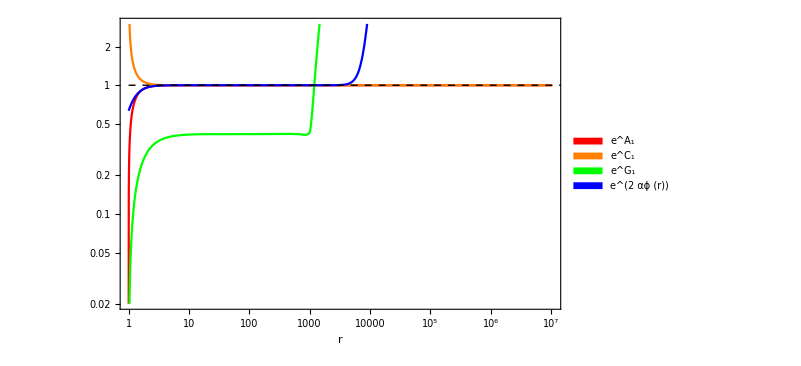

## RESULTS: WE SEE THAT THE INTERPOLATION BREAKS DOWN BEYOND A CERTAIN VALUES OF R. THIS GIVES US A NATURAL DEFINITION OF WHERE THE UV CUTOFF SHOULD BE. -------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

## THE STRENGHT OF THE INTERPOLATION IS CONTROLED MOSTLY BY c0 WHICH IS A FREE PARAMETER. WHEN c0 = 0, WE HAVE A PURE ADS BRANE AND WHEN c0 = 1, WE HAVE A PURE LIFSHITZ BRANE. HERE WE PICK c0 = 0.05

```mathematica
(*Parameters*)rh=1;c0=0.05;d=3;α=2;

(*Calculate initial values*)
BCval1=slngen2[c0,rh,d,α,1,1,1]
BCval2=slngen2[c0,rh,d,α,Sqrt[BCval1[[4]]],1/BCval1[[1]],1]
sln=slnhold2[c0,rh,d,α,Sqrt[BCval1[[4]]],1/BCval1[[1]],1]
L=1;

(*Clear variables*)
Clear[Lslab,ΔSIBB,ΔSIBBr,xIBB,xIBBr,Lslabr]

(* Calculation of the entanglement entropy, the size of the slab of the interpolating black brane (IBB) as a function of u and r. The reason why we integrate over u and r is to pick the least unstable solutions under numerical integration *)
ΔSIBB[us_,d_]:=Re[NIntegrate[1/u^3*(sln[[2]][1/u]-1)/(Sqrt[1-(u/us)^(2*d)]),{u,1/BCval2[[-1]],us}]]

ΔSIBBr[rs_,d_]:=Re[NIntegrate[-r*(sln[[2]][r]-1)/(Sqrt[1-(rs/r)^(2*d)]),{r,BCval2[[-1]],rs}]]

xIBB[U_,us_,d_]:=Re[L^2*NIntegrate[-(sln[[2]][1/u])/(Sqrt[(us/u)^(2*d)-1]),{u,us,U}]]

xIBBr[U_,rs_,d_]:=Re[L^2*NIntegrate[1/r^2*sln[[2]][r]/Sqrt[(r/rs)^(2*d)-1],{r,rs,U}]]

Lslab[us_,d_]:=Re[-L^2*NIntegrate[-(sln[[2]][1/u])/(Sqrt[(us/u)^(2*d)-1]),{u,1/BCval2[[-1]],us}]]

Lslabr[rs_,d_]:=Re[L^2*NIntegrate[1/r^2*1/Sqrt[(r/rs)^(2*d)-1],{r,rs,BCval2[[-1]]}]]



(* Calculation of the pure AdS brane *)
RSmax=100;

If[BCval1[[5]]<rh,transPoint=BCval1[[6]],transPoint=BCval1[[5]]]; (* Statement that there is an interpolation is the value of mu < rh. Otherwise, the interpolation occurs at the value of the temperature *)

Aads[r_,rh_,d_]:=(L*r*Sqrt[1-(rh/r)^(d+1)])^2

Cads[r_,rh_,d_]:=(L/(r*Sqrt[1-(rh/r)^(d+1)]))^2

BCval1=slngen[c0,1,d,α,1,1];

ThAds[rh_,d_]:=Sqrt[(D[Aads[r,rh1,d],r]/. r->rh1)*(D[1/Cads[r,rh1,d],r]/. r->rh1)]/(4*Pi)

rHAds=N[Solve[ThAds[rh,3]==BCval1[[6]],rh1][[2,1,2]]]

C1AdS[r_,d_,rh1_]:=1/Sqrt[1-(rh1/r)^(d+1)]

ΔSAdS[us_,d_]:=Re[NIntegrate[1/u^3*(C1AdS[1/u,d,rHAds]-1)/(Sqrt[1-(u/us)^(2*d)]),{u,1/BCval2[[-1]],us}]]

ΔSAdS1[us_,d_]:=Re[NIntegrate[1/u^3*(C1AdS[1/u,d,rh]-1)/(Sqrt[1-(u/us)^(2*d)]),{u,1/BCval2[[-1]],us}]]

If[rHAds<rh,rIntAdS=rh,rIntAdS=rHAds];

(*Plot*)
Legended[Show[ParametricPlot[{Lslab[us,d],ΔSAdS[us,d]},{us,1/RSmax,1/rIntAdS},ScalingFunctions->{"Log","Log"},Epilog->{{Green,Thick,Dashed,Line[{{Log[BCval1[[5]]],-100},{Log[BCval1[[5]]],100}}]},{Orange,Thick,Dashed,Line[{{Log[BCval1[[6]]],-100},{Log[BCval1[[6]]],100}}]}},PlotStyle->{Dashed,Black},Frame->True,FrameTicks->All,FrameLabel->{Style["Log[Subscript[L, slab]]",Black,25],Style["Log[4Subscript[G, N] Subscript[ΔS, IBB]]",Black,25]},FrameTicksStyle->Directive[Black,20],Axes->False,Mesh->False,AspectRatio->1/GoldenRatio],ParametricPlot[{Lslab[us,d],ΔSAdS1[us,d]},{us,1/RSmax,1/rh},ScalingFunctions->{"Log","Log"},Epilog->{{Green,Thick,Dashed,Line[{{Log[BCval1[[5]]],-100},{Log[BCval1[[5]]],100}}]},{Orange,Thick,Dashed,Line[{{Log[BCval1[[6]]],-100},{Log[BCval1[[6]]],100}}]}},PlotStyle->{Dashed,Red},Frame->True,FrameTicks->All,FrameLabel->{Style["Subscript[L, slab]",Black,25],Style["4Subscript[G, N] Subscript[ΔS, IBB]",Black,25]},FrameTicksStyle->Directive[Black,20],RotateLabel->{False,True},Axes->False,Mesh->False,AspectRatio->1/GoldenRatio],PlotRange->All,ImageSize->1000],Placed[LineLegend[{Blue,{Dashed,Black},{Dashed,Red}},{"IBB","AdS (same T)","AdS (same \!\(\*SubscriptBox[\(r\), \(h\)]\))"},LegendLayout->"Column",LegendMarkerSize->25,LabelStyle->{Black,FontSize->25,Font->"Arial"},LegendFunction->Framed],{0.17,0.82}]]
```

{1.02311,1.,0.0725783,0.144251,0.186779,0.311121,0.60034,1000.}

{1.,1.,0.185603,1.00001,0.185602,0.311121,0.596558,1000.}

{InterpolatingFunction[{{1., 1000.}}, <>],InterpolatingFunction[{{1., 1000.}}, <>],InterpolatingFunction[{{1., 1000.}}, <>],InterpolatingFunction[{{1., 1000.}}, <>]}

0.977416

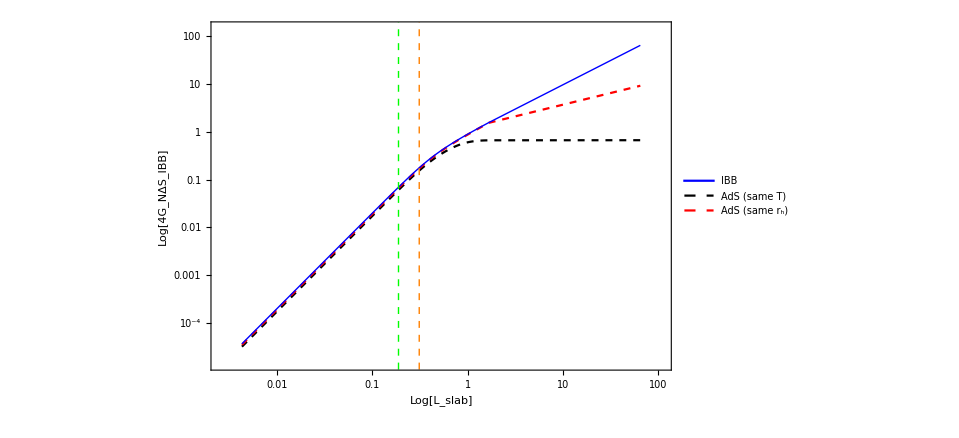

## RESULTS: WE SEE THAT THE ENTANGLEMENT ENTROPY MOVES FROM AN AREA LAW (LOG) TO A POWER LAW (VOLUME) AROUND THE PHASE TRANSITION (GREEN LINE), WHICH IS WHAT WE EXPECT TO HAPPEN. ALSO, SINCE c0 = 0.05, WE SEE THAT OUR BRANE (BLUE LINE) MIMICTS THE BEHAVIOUR OF AN ADS BRANE (RED LINE) EVEN BEYOND THE PHASE TRANSITION OCCURS (GREEN LINE). # -------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

## WE TAKE c0 = 0.25

```mathematica
Clear[BCval, sln]
d = 3; α = 2; rh = 1; c0 = 0.25; (* Set free parameters, we choose a larger value of c0 = a stronger interpolation *)
BCval1 = slngen2[c0,rh,d,α,1,1,1]
BCval2 = slngen2[c0,rh,d,α,Sqrt[BCval1[[4]]],1/BCval1[[1]],1]
sln = slnhold2[c0,rh,d,α,Sqrt[BCval1[[4]]],1/BCval1[[1]],1]
L= 1;
(* PLOT THE VALUE OF THE FIELDS VS R *)
Legended[LogLogPlot[{sln[[1]][r],sln[[2]][r],sln[[3]][r],sln[[4]][r]},{r, rh, BCval2[[-1]]}, PlotRange-> {{rh,BCval2[[-1]]},{0.02,3}},PlotStyle->{Red,Orange,Green, Blue}, Frame->True ,FrameTicks->Automatic,FrameLabel->{Style["r",Black, 25],None(*Style[ "Field",Black, 25]*)},FrameTicksStyle->Directive[Black,20],RotateLabel->{False,True},Axes->False, Mesh->False,ImageSize->700,Epilog->{Black, Dashed, Line[{{0,Log[1]},{1000,Log[1]}}]}(* ,GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]*)],Placed[SwatchLegend[{Red, Orange,Green, Blue}, {"e^A_1","e^C_1","e^G_1" ,"e^(2  αϕ (r))"}, LegendLayout->"Column", LegendMarkerSize->25,LabelStyle->{Black, FontSize->25, Font-> "Arial"}, LegendFunction->Framed],{0.87, 0.25}]]


(* CALCULATE THE ENTANGLEMENT ENTROPY AND THE SIZE OF THE SLAB OF THE INTERPOLATING BLACK BRANES AS A FUNCTION OF u = 1/r. THE GOAL OF THIS IS TO PICK THE LEAST UNSTABLE SOLUTIONS UNDER NUMERICAL INTERPOLATION.  *)
Clear[Lslab, ΔSIBB,ΔSIBBr,xIBB,xIBBr,Lslab,Lslabr]

ΔSIBB[us_, d_ ]:= Re[NIntegrate[1/u^3*( sln[[2]][1/u]-1)/(Sqrt[1-(u/us)^(2*d)]), {u, 1/BCval2[[-1]], us}]]
Lslab[us_, d_ ]:= Re[-L^2*NIntegrate[-( sln[[2]][1/u])/(Sqrt[(us/u)^(2*d)-1]), {u, 1/BCval2[[-1]], us}]]

(* CALCULATION OF THE ADS BLACK BRANE AT THE SAME r_h and the same temperature *)

RSmax =BCval1[[-1]];

(* CALCULATION OF THE ENTROPY OF THE ADS BLACK BRANE AT THE SAME RADIUS OF HORIZON AS OUR INTERPOLATING BLACK BRANE *) 
Cads[r_, rh_, d_]:= (L/(r*Sqrt[1-(rh/r)^(d+1)]))^2 (* PURE ADS FIELD VALUES *)
ΔSAdS1[us_, d_ ]:= Re[NIntegrate[1/u^3*(C1AdS[1/u,d, rh]-1)/(Sqrt[1-(u/us)^(2*d)]), {u, 1/BCval2[[-1]], us}]] 


(* EXTRACTING THE RADIUS OF HORIZON FOR THE ADS BLACK BRANE AT THE SAME TEMPERATURE AS OUR INTERPOLATING BLACK BRANE *)
ThAds[rh_,d_]:= Sqrt[(D[Aads[r,rh1,d],r]/.r->rh1)*(D[1/Cads[r,rh1,d],r]/.r->rh1)]/(4*Pi)
rHAds = N[Solve[ThAds[rh, 3]==BCval1[[6]],rh1][[2,1,2]]]

C1AdS[r_, d_,rh1_]:= 1/Sqrt[1-(rh1/r)^(d+1)] (* VALUES OF THE FIELD VALUES FOR ADS BLACK BRANE AT THE SAME TEMPERATURE *)
(* CALCULATION OF THE ENTROPY OF THE ADS BLACK BRANE AT THE TEMPERATURE AS OUR INTERPOLATING BLACK BRANE *) 
ΔSAdS[us_, d_ ]:= Re[NIntegrate[1/u^3*(C1AdS[1/u,d, rHAds]-1)/(Sqrt[1-(u/us)^(2*d)]), {u, 1/BCval2[[-1]], us}]]

(* PLOT *)
If[rHAds<rh, rIntAdS = rh, rIntAdS =rHAds]; (* Set the range of the AdS brane, so that we do not plot the divergence point where r = rh. *)
Legended[Show[ (* PLOT THE ENTANGLEMENT ENTROPY VS L_slab FOR THE AdS black branes(ABB) at the same temperature and same radius of horizon *)ParametricPlot[{Lslab[us,d],ΔSAdS[us, d]},{us, 1/RSmax, 1/rIntAdS },ScalingFunctions->{"Log","Log"},Epilog->{{Green,Thick, Dashed, Line[{{Log[BCval1[[5]]],-100},{Log[BCval1[[5]]],100}}]},{Orange, Thick,Dashed, Line[{{Log[ BCval1[[6]]],-100},{ Log[BCval1[[6]]],100}}]}},PlotStyle->{Dashed, Black},  Frame->True ,FrameTicks->All,FrameLabel->{Style["Log[L_slab]",Black, 25],Style[ "Log[4G_NΔS_IBB]",Black, 25]},FrameTicksStyle->Directive[Black,20],Axes->False, Mesh->False,AspectRatio->1/GoldenRatio],ParametricPlot[{Lslab[us,d],ΔSAdS1[us, d]},{us, 1/RSmax, 1/rh },ScalingFunctions->{"Log","Log"},Epilog->{{Green,Thick, Dashed, Line[{{Log[BCval1[[5]]],-100},{Log[BCval1[[5]]],100}}]},{Orange, Thick,Dashed, Line[{{Log[ BCval1[[6]]],-100},{ Log[BCval1[[6]]],100}}]}},PlotStyle->{Dashed, Red},  Frame->True ,FrameTicks->All,FrameLabel->{Style["L_slab",Black, 25],Style[ "4G_N ΔS",Black, 25]},FrameTicksStyle->Directive[Black,20],RotateLabel->{False,True},Axes->False, Mesh->False,AspectRatio->1/GoldenRatio], (* PLOT THE ENTANGLEMENT ENTROPY VS L_SLAB FOR THE INTERPOLATING BLACK BRANE (IBB) *)ParametricPlot[{Lslab[us,d],ΔSIBB[us, d]},{us, 1/RSmax, 1/rh},ScalingFunctions->{"Log","Log"},Epilog->{{Red,Thick, Dashed, Line[{{Log[BCval1[[5]]],-100},{Log[BCval1[[5]]],100}}]},{Orange, Thick,Dashed, Line[{{Log[ BCval1[[6]]],-100},{ Log[BCval1[[6]]],100}}]}},PlotStyle->{Thick, Blue}, Frame->True ,FrameTicks->All,FrameLabel->{Style["Log[L_slab]",Black, 25],Style[ "Log[4G_NΔS_IBB]",Black, 25]},FrameTicksStyle->Directive[Black,20],Axes->False, Mesh->False,AspectRatio->1/GoldenRatio], PlotRange->All, ImageSize->1000],Placed[LineLegend[{Blue,{Dashed, Black},{Dashed,Red}}, {"IBB","AdS (same T)","AdS (same r_h)"}, LegendLayout->"Column", LegendMarkerSize->25,LabelStyle->{Black, FontSize->25, Font-> "Arial"}, LegendFunction->Framed],{0.17, 0.82}]]
(* ---------------- *)
```

{1.13126,1.,0.470227,0.981598,0.419547,0.281377,1.49105,1000.}

{1.,1.,0.418181,0.999952,0.418191,0.281377,1.48623,1000.}

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

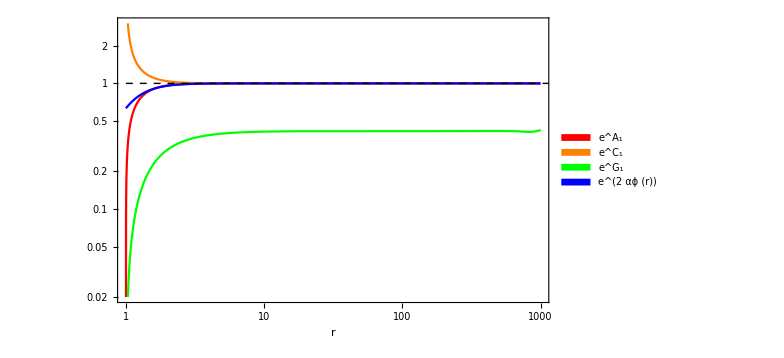

0.883973

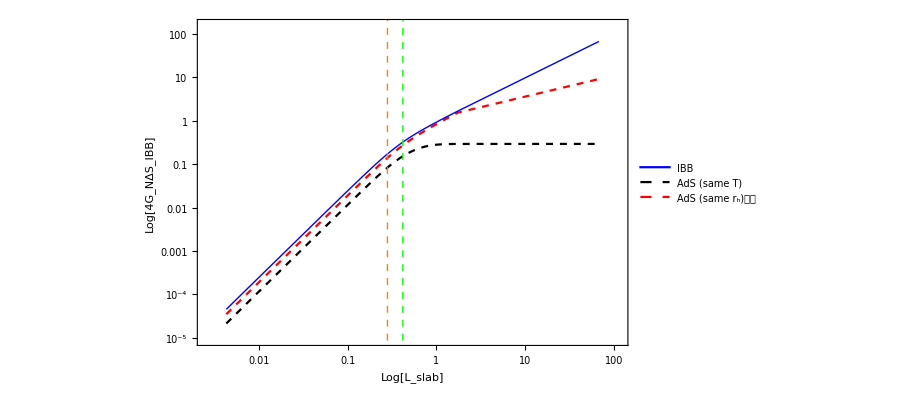

## RESULTS: THE POINT WHERE OUR BRANE (BLUE LINE) DIVERGES FROM THE PURE ADS BRANE (RED LINE) OCCURS CLOSER TO THE POINT WHERE THE PHASE TRANSITION (GREEN LINE) OCCURS, WHICH IS AS EXPECTED FROM A LARGER VALUE OF c0. BUT OVERALL, WE DO NOT SEE ANYTHING NOVEL ASSOCIATED WITH THE PHASE TRANSITION # -------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

## HERE WE LOOK AT THE CASE WHERE μ = T. IT TRANSLATES INTO CHOOSING c_0 = 0.5

```mathematica
rh = 1;c0=0.50;d=3;α=2;
BCval1 = slngen2[c0,rh,d,α,1,1,1]
BCval2 = slngen2[c0,rh,d,α,Sqrt[BCval1[[4]]],1/BCval1[[1]],1]
sln = slnhold2[c0,rh,d,α,Sqrt[BCval1[[4]]],1/BCval1[[1]],1]
L= 1;

(* CALCULATE THE ENTANGLEMENT ENTROPY AND THE SIZE OF THE SLAB OF THE INTERPOLATING BLACK BRANES AS A FUNCTION OF u = 1/r. THE GOAL OF THIS IS TO PICK THE LEAST UNSTABLE SOLUTIONS UNDER NUMERICAL INTERPOLATION.  *)
Clear[Lslab, ΔSIBB,ΔSIBBr,xIBB,xIBBr,Lslab,Lslabr]

ΔSIBB[us_, d_ ]:= Re[NIntegrate[1/u^3*( sln[[2]][1/u]-1)/(Sqrt[1-(u/us)^(2*d)]), {u, 1/BCval2[[-1]], us}]]
Lslab[us_, d_ ]:= Re[-L^2*NIntegrate[-( sln[[2]][1/u])/(Sqrt[(us/u)^(2*d)-1]), {u, 1/BCval2[[-1]], us}]]

(* CALCULATION OF THE ADS BLACK BRANE AT THE SAME r_h and the same temperature *)

RSmax =BCval1[[-1]];

(* CALCULATION OF THE ENTROPY OF THE ADS BLACK BRANE AT THE SAME RADIUS OF HORIZON AS OUR INTERPOLATING BLACK BRANE *) 
Cads[r_, rh_, d_]:= (L/(r*Sqrt[1-(rh/r)^(d+1)]))^2 (* PURE ADS FIELD VALUES *)
ΔSAdS1[us_, d_ ]:= Re[NIntegrate[1/u^3*(C1AdS[1/u,d, rh]-1)/(Sqrt[1-(u/us)^(2*d)]), {u, 1/BCval2[[-1]], us}]] 


(* EXTRACTING THE RADIUS OF HORIZON FOR THE ADS BLACK BRANE AT THE SAME TEMPERATURE AS OUR INTERPOLATING BLACK BRANE *)
ThAds[rh_,d_]:= Sqrt[(D[Aads[r,rh1,d],r]/.r->rh1)*(D[1/Cads[r,rh1,d],r]/.r->rh1)]/(4*Pi)
rHAds = N[Solve[ThAds[rh, 3]==BCval1[[6]],rh1][[2,1,2]]]

C1AdS[r_, d_,rh1_]:= 1/Sqrt[1-(rh1/r)^(d+1)] (* VALUES OF THE FIELD VALUES FOR ADS BLACK BRANE AT THE SAME TEMPERATURE *)
(* CALCULATION OF THE ENTROPY OF THE ADS BLACK BRANE AT THE TEMPERATURE AS OUR INTERPOLATING BLACK BRANE *) 
ΔSAdS[us_, d_ ]:= Re[NIntegrate[1/u^3*(C1AdS[1/u,d, rHAds]-1)/(Sqrt[1-(u/us)^(2*d)]), {u, 1/BCval2[[-1]], us}]]

(* PLOT *)
If[rHAds<rh, rIntAdS = rh, rIntAdS =rHAds]; (* Set the range of the AdS brane, so that we do not plot the divergence point where r = rh. *)
Legended[Show[ (* PLOT THE ENTANGLEMENT ENTROPY VS L_slab FOR THE AdS black branes(ABB) at the same temperature and same radius of horizon *)ParametricPlot[{Lslab[us,d],ΔSAdS[us, d]},{us, 1/RSmax, 1/rIntAdS },ScalingFunctions->{"Log","Log"},Epilog->{{Green,Thick, Dashed, Line[{{Log[BCval1[[5]]],-100},{Log[BCval1[[5]]],100}}]},{Orange, Thick,Dashed, Line[{{Log[ BCval1[[6]]],-100},{ Log[BCval1[[6]]],100}}]}},PlotStyle->{Dashed, Black},  Frame->True ,FrameTicks->All,FrameLabel->{Style["Log[L_slab]",Black, 25],Style[ "Log[4G_NΔS_IBB]",Black, 25]},FrameTicksStyle->Directive[Black,20],Axes->False, Mesh->False,AspectRatio->1/GoldenRatio],ParametricPlot[{Lslab[us,d],ΔSAdS1[us, d]},{us, 1/RSmax, 1/rh },ScalingFunctions->{"Log","Log"},Epilog->{{Green,Thick, Dashed, Line[{{Log[BCval1[[5]]],-100},{Log[BCval1[[5]]],100}}]},{Orange, Thick,Dashed, Line[{{Log[ BCval1[[6]]],-100},{ Log[BCval1[[6]]],100}}]}},PlotStyle->{Dashed, Red},  Frame->True ,FrameTicks->All,FrameLabel->{Style["L_slab",Black, 25],Style[ "4G_N ΔS",Black, 25]},FrameTicksStyle->Directive[Black,20],RotateLabel->{False,True},Axes->False, Mesh->False,AspectRatio->1/GoldenRatio], (* PLOT THE ENTANGLEMENT ENTROPY VS L_SLAB FOR THE INTERPOLATING BLACK BRANE (IBB) *)ParametricPlot[{Lslab[us,d],ΔSIBB[us, d]},{us, 1/RSmax, 1/rh},ScalingFunctions->{"Log","Log"},Epilog->{{Red,Thick, Dashed, Line[{{Log[BCval1[[5]]],-100},{Log[BCval1[[5]]],100}}]},{Orange, Thick,Dashed, Line[{{Log[ BCval1[[6]]],-100},{ Log[BCval1[[6]]],100}}]}},PlotStyle->{Thick, Blue}, Frame->True ,FrameTicks->All,FrameLabel->{Style["Log[L_slab]",Black, 25],Style[ "Log[4G_NΔS_IBB]",Black, 25]},FrameTicksStyle->Directive[Black,20],Axes->False, Mesh->False,AspectRatio->1/GoldenRatio], PlotRange->All, ImageSize->1000],Placed[LineLegend[{Blue,{Dashed, Black},{Dashed,Red}}, {"IBB","AdS (same T)","AdS (same r_h)"}, LegendLayout->"Column", LegendMarkerSize->25,LabelStyle->{Black, FontSize->25, Font-> "Arial"}, LegendFunction->Framed],{0.17, 0.82}]]
```

{1.32594,1.,1.49548,3.30495,0.620402,0.240063,2.58432,1000.}

{1.,1.,0.619345,0.999953,0.61936,0.240063,2.57998,1000.}

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

0.754181

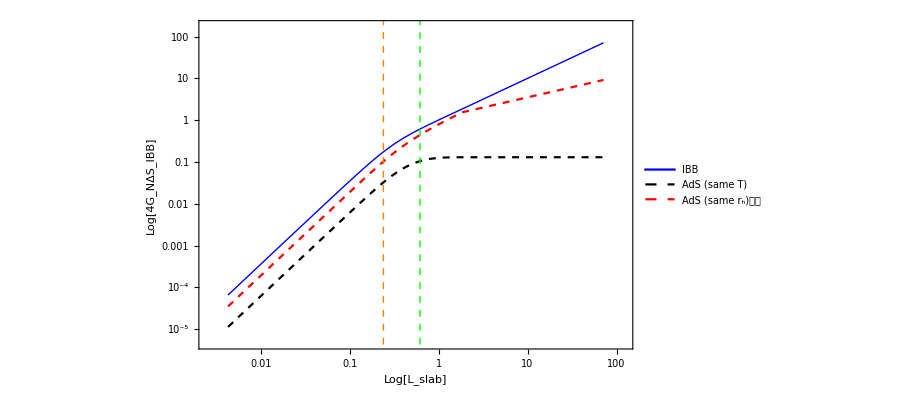

## RESULTS: OUR BRANE (BLUE LINE) DEVIATES FROM THE PURE ADS BRANE (RED LINE) EVERYWHERE, WHICH IS AS EXPECTED FROM CHOOSING c0 = 0.5, WHICH MEANS THAT OUR BRANE HAS “AS MUCH” LIFSHITZ BEHAVIOURS AS IT HAS ADS BEHAVIOUR. WHAT IS INTERESTING NOW IS THAT IT LOOKS LIKE OUR BRANE (BLUE LINE) STARTS TO GET A CHANGE OF CURVATURE AFTER THE PHASE TRANSITION (GREEN LINE). THIS IS SOMETHING NOVEL THAT IS NOT EXPECTED TO HAPPEN. # -------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

## HERE WE MAKE c0 = 0.85

```mathematica
rh = 1;c0=0.85;d=3;α=2;
BCval1 = slngen2[c0,rh,d,α,1,1,1]
BCval2 = slngen2[c0,rh,d,α,Sqrt[BCval1[[4]]],1/BCval1[[1]],1]
sln = slnhold2[c0,rh,d,α,Sqrt[BCval1[[4]]],1/BCval1[[1]],1]
L= 1;

(* CALCULATE THE ENTANGLEMENT ENTROPY AND THE SIZE OF THE SLAB OF THE INTERPOLATING BLACK BRANES AS A FUNCTION OF u = 1/r. THE GOAL OF THIS IS TO PICK THE LEAST UNSTABLE SOLUTIONS UNDER NUMERICAL INTERPOLATION.  *)
Clear[Lslab, ΔSIBB,ΔSIBBr,xIBB,xIBBr,Lslab,Lslabr]

ΔSIBB[us_, d_ ]:= Re[NIntegrate[1/u^3*( sln[[2]][1/u]-1)/(Sqrt[1-(u/us)^(2*d)]), {u, 1/BCval2[[-1]], us}]]
Lslab[us_, d_ ]:= Re[-L^2*NIntegrate[-( sln[[2]][1/u])/(Sqrt[(us/u)^(2*d)-1]), {u, 1/BCval2[[-1]], us}]]

(* CALCULATION OF THE ADS BLACK BRANE AT THE SAME r_h and the same temperature *)

RSmax =BCval1[[-1]];

(* CALCULATION OF THE ENTROPY OF THE ADS BLACK BRANE AT THE SAME RADIUS OF HORIZON AS OUR INTERPOLATING BLACK BRANE *) 
Cads[r_, rh_, d_]:= (L/(r*Sqrt[1-(rh/r)^(d+1)]))^2 (* PURE ADS FIELD VALUES *)
ΔSAdS1[us_, d_ ]:= Re[NIntegrate[1/u^3*(C1AdS[1/u,d, rh]-1)/(Sqrt[1-(u/us)^(2*d)]), {u, 1/BCval2[[-1]], us}]] 


(* EXTRACTING THE RADIUS OF HORIZON FOR THE ADS BLACK BRANE AT THE SAME TEMPERATURE AS OUR INTERPOLATING BLACK BRANE *)
ThAds[rh_,d_]:= Sqrt[(D[Aads[r,rh1,d],r]/.r->rh1)*(D[1/Cads[r,rh1,d],r]/.r->rh1)]/(4*Pi)
rHAds = N[Solve[ThAds[rh, 3]==BCval1[[6]],rh1][[2,1,2]]]

C1AdS[r_, d_,rh1_]:= 1/Sqrt[1-(rh1/r)^(d+1)] (* VALUES OF THE FIELD VALUES FOR ADS BLACK BRANE AT THE SAME TEMPERATURE *)
(* CALCULATION OF THE ENTROPY OF THE ADS BLACK BRANE AT THE TEMPERATURE AS OUR INTERPOLATING BLACK BRANE *) 
ΔSAdS[us_, d_ ]:= Re[NIntegrate[1/u^3*(C1AdS[1/u,d, rHAds]-1)/(Sqrt[1-(u/us)^(2*d)]), {u, 1/BCval2[[-1]], us}]]

(* PLOT *)
If[rHAds<rh, rIntAdS = rh, rIntAdS =rHAds]; (* Set the range of the AdS brane, so that we do not plot the divergence point where r = rh. *)
Legended[Show[ (* PLOT THE ENTANGLEMENT ENTROPY VS L_slab FOR THE AdS black branes(ABB) at the same temperature and same radius of horizon *)ParametricPlot[{Lslab[us,d],ΔSAdS[us, d]},{us, 1/RSmax, 1/rIntAdS },ScalingFunctions->{"Log","Log"},Epilog->{{Green,Thick, Dashed, Line[{{Log[BCval1[[5]]],-100},{Log[BCval1[[5]]],100}}]},{Orange, Thick,Dashed, Line[{{Log[ BCval1[[6]]],-100},{ Log[BCval1[[6]]],100}}]}},PlotStyle->{Dashed, Black},  Frame->True ,FrameTicks->All,FrameLabel->{Style["Log[L_slab]",Black, 25],Style[ "Log[4G_NΔS_IBB]",Black, 25]},FrameTicksStyle->Directive[Black,20],Axes->False, Mesh->False,AspectRatio->1/GoldenRatio],ParametricPlot[{Lslab[us,d],ΔSAdS1[us, d]},{us, 1/RSmax, 1/rh },ScalingFunctions->{"Log","Log"},Epilog->{{Green,Thick, Dashed, Line[{{Log[BCval1[[5]]],-100},{Log[BCval1[[5]]],100}}]},{Orange, Thick,Dashed, Line[{{Log[ BCval1[[6]]],-100},{ Log[BCval1[[6]]],100}}]}},PlotStyle->{Dashed, Red},  Frame->True ,FrameTicks->All,FrameLabel->{Style["L_slab",Black, 25],Style[ "4G_N ΔS",Black, 25]},FrameTicksStyle->Directive[Black,20],RotateLabel->{False,True},Axes->False, Mesh->False,AspectRatio->1/GoldenRatio], (* PLOT THE ENTANGLEMENT ENTROPY VS L_SLAB FOR THE INTERPOLATING BLACK BRANE (IBB) *)ParametricPlot[{Lslab[us,d],ΔSIBB[us, d]},{us, 1/RSmax, 1/rh},ScalingFunctions->{"Log","Log"},Epilog->{{Red,Thick, Dashed, Line[{{Log[BCval1[[5]]],-100},{Log[BCval1[[5]]],100}}]},{Orange, Thick,Dashed, Line[{{Log[ BCval1[[6]]],-100},{ Log[BCval1[[6]]],100}}]}},PlotStyle->{Thick, Blue}, Frame->True ,FrameTicks->All,FrameLabel->{Style["Log[L_slab]",Black, 25],Style[ "Log[4G_NΔS_IBB]",Black, 25]},FrameTicksStyle->Directive[Black,20],Axes->False, Mesh->False,AspectRatio->1/GoldenRatio], PlotRange->All, ImageSize->1000],Placed[LineLegend[{Blue,{Dashed, Black},{Dashed,Red}}, {"IBB","AdS (same T)","AdS (same r_h)"}, LegendLayout->"Column", LegendMarkerSize->25,LabelStyle->{Black, FontSize->25, Font-> "Arial"}, LegendFunction->Framed],{0.17, 0.82}]]
```

{2.01841,1.,10.0432,25.6717,0.98206,0.157704,6.22725,1000.}

{1.,1.,0.982705,0.999994,0.982708,0.157704,6.23136,1000.}

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

0.495438

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.001043706876600945584608777505497556603586417622864246368408203125}. NIntegrate obtained 2.10555×10^-6 and 3.75508×10^-12 for the integral and error estimates.

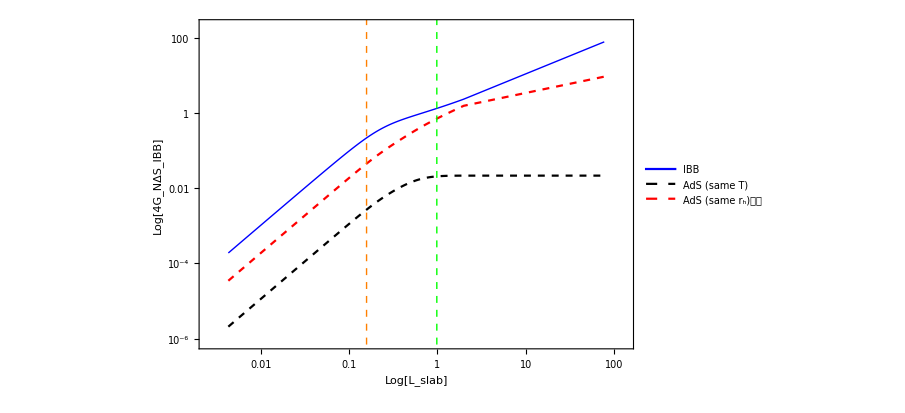

## RESULTS: THE CHANGE IN CURVATURE BECOMES MORE PRONOUNCED NOW AND OCCURS EXCTLY WHERE THE PHASE TRANSITION OCCURS. IF THE CHANGE OF CURVATURE BECOMES TOO SHARP, IT MIGHT INDICATE A VIOLATION OF THE C-THEOREM. # -------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

## WE TAKE c0 = 0.95 (VERY CLOSE TO A PURE LIFSHITZ BRANE)

```mathematica
rh = 1;c0=0.95;d=3;α=2;
BCval1 = slngen2[c0,rh,d,α,1,1,1]
BCval2 = slngen2[c0,rh,d,α,Sqrt[BCval1[[4]]],1/BCval1[[1]],1]
sln = slnhold2[c0,rh,d,α,Sqrt[BCval1[[4]]],1/BCval1[[1]],1]
L= 1;

(* CALCULATE THE ENTANGLEMENT ENTROPY AND THE SIZE OF THE SLAB OF THE INTERPOLATING BLACK BRANES AS A FUNCTION OF u = 1/r. THE GOAL OF THIS IS TO PICK THE LEAST UNSTABLE SOLUTIONS UNDER NUMERICAL INTERPOLATION.  *)
Clear[Lslab, ΔSIBB,ΔSIBBr,xIBB,xIBBr,Lslab,Lslabr]

ΔSIBB[us_, d_ ]:= Re[NIntegrate[1/u^3*( sln[[2]][1/u]-1)/(Sqrt[1-(u/us)^(2*d)]), {u, 1/BCval2[[-1]], us}]]
Lslab[us_, d_ ]:= Re[-L^2*NIntegrate[-( sln[[2]][1/u])/(Sqrt[(us/u)^(2*d)-1]), {u, 1/BCval2[[-1]], us}]]

(* CALCULATION OF THE ADS BLACK BRANE AT THE SAME r_h and the same temperature *)

RSmax =BCval1[[-1]];

(* CALCULATION OF THE ENTROPY OF THE ADS BLACK BRANE AT THE SAME RADIUS OF HORIZON AS OUR INTERPOLATING BLACK BRANE *) 
Cads[r_, rh_, d_]:= (L/(r*Sqrt[1-(rh/r)^(d+1)]))^2 (* PURE ADS FIELD VALUES *)
ΔSAdS1[us_, d_ ]:= Re[NIntegrate[1/u^3*(C1AdS[1/u,d, rh]-1)/(Sqrt[1-(u/us)^(2*d)]), {u, 1/BCval2[[-1]], us}]] 


(* EXTRACTING THE RADIUS OF HORIZON FOR THE ADS BLACK BRANE AT THE SAME TEMPERATURE AS OUR INTERPOLATING BLACK BRANE *)
ThAds[rh_,d_]:= Sqrt[(D[Aads[r,rh1,d],r]/.r->rh1)*(D[1/Cads[r,rh1,d],r]/.r->rh1)]/(4*Pi)
rHAds = N[Solve[ThAds[rh, 3]==BCval1[[6]],rh1][[2,1,2]]]

C1AdS[r_, d_,rh1_]:= 1/Sqrt[1-(rh1/r)^(d+1)] (* VALUES OF THE FIELD VALUES FOR ADS BLACK BRANE AT THE SAME TEMPERATURE *)
(* CALCULATION OF THE ENTROPY OF THE ADS BLACK BRANE AT THE TEMPERATURE AS OUR INTERPOLATING BLACK BRANE *) 
ΔSAdS[us_, d_ ]:= Re[NIntegrate[1/u^3*(C1AdS[1/u,d, rHAds]-1)/(Sqrt[1-(u/us)^(2*d)]), {u, 1/BCval2[[-1]], us}]]

(* PLOT *)
If[rHAds<rh, rIntAdS = rh, rIntAdS =rHAds]; (* Set the range of the AdS brane, so that we do not plot the divergence point where r = rh. *)
Legended[Show[ (* PLOT THE ENTANGLEMENT ENTROPY VS L_slab FOR THE AdS black branes(ABB) at the same temperature and same radius of horizon *)ParametricPlot[{Lslab[us,d],ΔSAdS[us, d]},{us, 1/RSmax, 1/rIntAdS },ScalingFunctions->{"Log","Log"},Epilog->{{Green,Thick, Dashed, Line[{{Log[BCval1[[5]]],-100},{Log[BCval1[[5]]],100}}]},{Orange, Thick,Dashed, Line[{{Log[ BCval1[[6]]],-100},{ Log[BCval1[[6]]],100}}]}},PlotStyle->{Dashed, Black},  Frame->True ,FrameTicks->All,FrameLabel->{Style["Log[L_slab]",Black, 25],Style[ "Log[4G_NΔS_IBB]",Black, 25]},FrameTicksStyle->Directive[Black,20],Axes->False, Mesh->False,AspectRatio->1/GoldenRatio],ParametricPlot[{Lslab[us,d],ΔSAdS1[us, d]},{us, 1/RSmax, 1/rh },ScalingFunctions->{"Log","Log"},Epilog->{{Green,Thick, Dashed, Line[{{Log[BCval1[[5]]],-100},{Log[BCval1[[5]]],100}}]},{Orange, Thick,Dashed, Line[{{Log[ BCval1[[6]]],-100},{ Log[BCval1[[6]]],100}}]}},PlotStyle->{Dashed, Red},  Frame->True ,FrameTicks->All,FrameLabel->{Style["L_slab",Black, 25],Style[ "4G_N ΔS",Black, 25]},FrameTicksStyle->Directive[Black,20],RotateLabel->{False,True},Axes->False, Mesh->False,AspectRatio->1/GoldenRatio], (* PLOT THE ENTANGLEMENT ENTROPY VS L_SLAB FOR THE INTERPOLATING BLACK BRANE (IBB) *)ParametricPlot[{Lslab[us,d],ΔSIBB[us, d]},{us, 1/RSmax, 1/rh},ScalingFunctions->{"Log","Log"},Epilog->{{Red,Thick, Dashed, Line[{{Log[BCval1[[5]]],-100},{Log[BCval1[[5]]],100}}]},{Orange, Thick,Dashed, Line[{{Log[ BCval1[[6]]],-100},{ Log[BCval1[[6]]],100}}]}},PlotStyle->{Thick, Blue}, Frame->True ,FrameTicks->All,FrameLabel->{Style["Log[L_slab]",Black, 25],Style[ "Log[4G_NΔS_IBB]",Black, 25]},FrameTicksStyle->Directive[Black,20],Axes->False, Mesh->False,AspectRatio->1/GoldenRatio], PlotRange->All, ImageSize->1000],Placed[LineLegend[{Blue,{Dashed, Black},{Dashed,Red}}, {"IBB","AdS (same T)","AdS (same r_h)"}, LegendLayout->"Column", LegendMarkerSize->25,LabelStyle->{Black, FontSize->25, Font-> "Arial"}, LegendFunction->Framed],{0.17, 0.82}]]
```

{2.88215,1.,39.373,113.439,1.28263,0.110442,11.6136,1000.}

{1.,1.,1.28301,1.00001,1.283,0.110442,11.6169,1000.}

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

0.346963

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.00191597}. NIntegrate obtained 5.06494×10^-7 and 1.50537×10^-12 for the integral and error estimates.

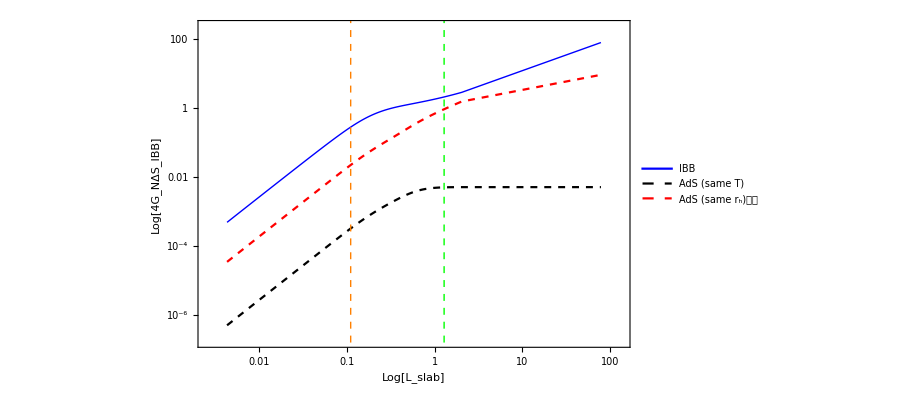

## RESULTS: CHANGE OF CURVATURE IS EVEN MORE PRONOUNCED. # -------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

## WE LOOK AT THE EFFECTS OF CHANGING OUR OTHER FREE PARAMETERS ON THE CURVATURE: rh: 1 ---> 2

```mathematica
rh = 2;c0=0.95;d=3;α=2;
BCval1 = slngen2[c0,rh,d,α,1,1,1]
BCval2 = slngen2[c0,rh,d,α,Sqrt[BCval1[[4]]],1/BCval1[[1]],1]
sln = slnhold2[c0,rh,d,α,Sqrt[BCval1[[4]]],1/BCval1[[1]],1]
L= 1;
(* CALCULATE THE ENTANGLEMENT ENTROPY AND THE SIZE OF THE SLAB OF THE INTERPOLATING BLACK BRANES AS A FUNCTION OF u = 1/r. THE GOAL OF THIS IS TO PICK THE LEAST UNSTABLE SOLUTIONS UNDER NUMERICAL INTERPOLATION.  *)
Clear[Lslab, ΔSIBB,ΔSIBBr,xIBB,xIBBr,Lslab,Lslabr]

ΔSIBB[us_, d_ ]:= Re[NIntegrate[1/u^3*( sln[[2]][1/u]-1)/(Sqrt[1-(u/us)^(2*d)]), {u, 1/BCval2[[-1]], us}]]
Lslab[us_, d_ ]:= Re[-L^2*NIntegrate[-( sln[[2]][1/u])/(Sqrt[(us/u)^(2*d)-1]), {u, 1/BCval2[[-1]], us}]]

(* CALCULATION OF THE ADS BLACK BRANE AT THE SAME r_h and the same temperature *)

RSmax =BCval1[[-1]];

(* CALCULATION OF THE ENTROPY OF THE ADS BLACK BRANE AT THE SAME RADIUS OF HORIZON AS OUR INTERPOLATING BLACK BRANE *) 
Cads[r_, rh_, d_]:= (L/(r*Sqrt[1-(rh/r)^(d+1)]))^2 (* PURE ADS FIELD VALUES *)
ΔSAdS1[us_, d_ ]:= Re[NIntegrate[1/u^3*(C1AdS[1/u,d, rh]-1)/(Sqrt[1-(u/us)^(2*d)]), {u, 1/BCval2[[-1]], us}]] 


(* EXTRACTING THE RADIUS OF HORIZON FOR THE ADS BLACK BRANE AT THE SAME TEMPERATURE AS OUR INTERPOLATING BLACK BRANE *)
ThAds[rh_,d_]:= Sqrt[(D[Aads[r,rh1,d],r]/.r->rh1)*(D[1/Cads[r,rh1,d],r]/.r->rh1)]/(4*Pi)
rHAds = N[Solve[ThAds[rh, 3]==BCval1[[6]],rh1][[2,1,2]]]

C1AdS[r_, d_,rh1_]:= 1/Sqrt[1-(rh1/r)^(d+1)] (* VALUES OF THE FIELD VALUES FOR ADS BLACK BRANE AT THE SAME TEMPERATURE *)
(* CALCULATION OF THE ENTROPY OF THE ADS BLACK BRANE AT THE TEMPERATURE AS OUR INTERPOLATING BLACK BRANE *) 
ΔSAdS[us_, d_ ]:= Re[NIntegrate[1/u^3*(C1AdS[1/u,d, rHAds]-1)/(Sqrt[1-(u/us)^(2*d)]), {u, 1/BCval2[[-1]], us}]]

(* PLOT *)
If[rHAds<rh, rIntAdS = rh, rIntAdS =rHAds]; (* Set the range of the AdS brane, so that we do not plot the divergence point where r = rh. *)
Legended[Show[ (* PLOT THE ENTANGLEMENT ENTROPY VS L_slab FOR THE AdS black branes(ABB) at the same temperature and same radius of horizon *)ParametricPlot[{Lslab[us,d],ΔSAdS[us, d]},{us, 1/RSmax, 1/rIntAdS },ScalingFunctions->{"Log","Log"},Epilog->{{Green,Thick, Dashed, Line[{{Log[BCval1[[5]]],-100},{Log[BCval1[[5]]],100}}]},{Orange, Thick,Dashed, Line[{{Log[ BCval1[[6]]],-100},{ Log[BCval1[[6]]],100}}]}},PlotStyle->{Dashed, Black},  Frame->True ,FrameTicks->All,FrameLabel->{Style["Log[L_slab]",Black, 25],Style[ "Log[4G_NΔS_IBB]",Black, 25]},FrameTicksStyle->Directive[Black,20],Axes->False, Mesh->False,AspectRatio->1/GoldenRatio],ParametricPlot[{Lslab[us,d],ΔSAdS1[us, d]},{us, 1/RSmax, 1/rh },ScalingFunctions->{"Log","Log"},Epilog->{{Green,Thick, Dashed, Line[{{Log[BCval1[[5]]],-100},{Log[BCval1[[5]]],100}}]},{Orange, Thick,Dashed, Line[{{Log[ BCval1[[6]]],-100},{ Log[BCval1[[6]]],100}}]}},PlotStyle->{Dashed, Red},  Frame->True ,FrameTicks->All,FrameLabel->{Style["L_slab",Black, 25],Style[ "4G_N ΔS",Black, 25]},FrameTicksStyle->Directive[Black,20],RotateLabel->{False,True},Axes->False, Mesh->False,AspectRatio->1/GoldenRatio], (* PLOT THE ENTANGLEMENT ENTROPY VS L_SLAB FOR THE INTERPOLATING BLACK BRANE (IBB) *)ParametricPlot[{Lslab[us,d],ΔSIBB[us, d]},{us, 1/RSmax, 1/rh},ScalingFunctions->{"Log","Log"},Epilog->{{Red,Thick, Dashed, Line[{{Log[BCval1[[5]]],-100},{Log[BCval1[[5]]],100}}]},{Orange, Thick,Dashed, Line[{{Log[ BCval1[[6]]],-100},{ Log[BCval1[[6]]],100}}]}},PlotStyle->{Thick, Blue}, Frame->True ,FrameTicks->All,FrameLabel->{Style["Log[L_slab]",Black, 25],Style[ "Log[4G_NΔS_IBB]",Black, 25]},FrameTicksStyle->Directive[Black,20],Axes->False, Mesh->False,AspectRatio->1/GoldenRatio], PlotRange->All, ImageSize->1000],Placed[LineLegend[{Blue,{Dashed, Black},{Dashed,Red}}, {"IBB","AdS (same T)","AdS (same r_h)"}, LegendLayout->"Column", LegendMarkerSize->25,LabelStyle->{Black, FontSize->25, Font-> "Arial"}, LegendFunction->Framed],{0.17, 0.82}]]
```

{2.88215,1.,629.98,7260.09,2.5653,0.220884,11.6138,2000.}

{0.999999,1.,2.56308,0.999982,2.5631,0.220884,11.6039,2000.}

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

0.346963

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.000599876927610635019981651094855834571717423386871814727783203125}. NIntegrate obtained 5.08286×10^-7 and 7.17129×10^-12 for the integral and error estimates.

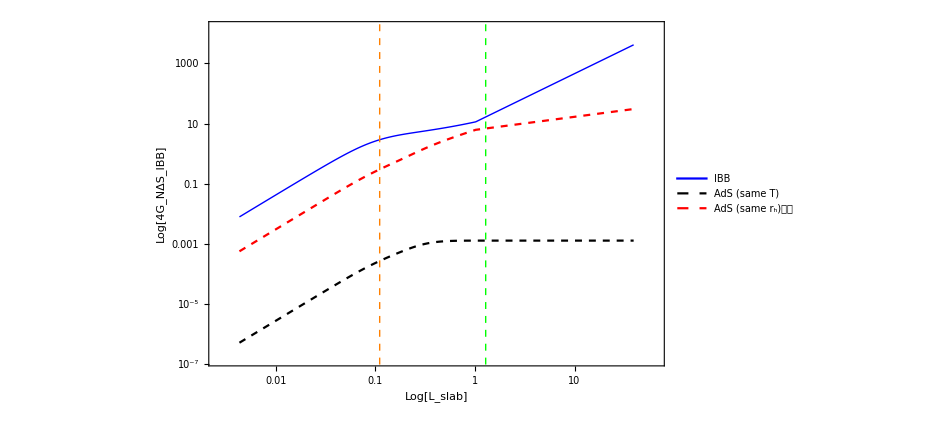

## CHANGING d : 3 -- -> 6

```mathematica
rh = 1;c0=0.95;d=6;α=2;
BCval1 = slngen2[c0,rh,d,α,1,1,1]
BCval2 = slngen2[c0,rh,d,α,Sqrt[BCval1[[4]]],1/BCval1[[1]],1]
sln = slnhold2[c0,rh,d,α,Sqrt[BCval1[[4]]],1/BCval1[[1]],1]
L= 1;

(* CALCULATE THE ENTANGLEMENT ENTROPY AND THE SIZE OF THE SLAB OF THE INTERPOLATING BLACK BRANES AS A FUNCTION OF u = 1/r. THE GOAL OF THIS IS TO PICK THE LEAST UNSTABLE SOLUTIONS UNDER NUMERICAL INTERPOLATION.  *)
Clear[Lslab, ΔSIBB,ΔSIBBr,xIBB,xIBBr,Lslab,Lslabr]

ΔSIBB[us_, d_ ]:= Re[NIntegrate[1/u^3*( sln[[2]][1/u]-1)/(Sqrt[1-(u/us)^(2*d)]), {u, 1/BCval2[[-1]], us}]]
Lslab[us_, d_ ]:= Re[-L^2*NIntegrate[-( sln[[2]][1/u])/(Sqrt[(us/u)^(2*d)-1]), {u, 1/BCval2[[-1]], us}]]

(* CALCULATION OF THE ADS BLACK BRANE AT THE SAME r_h and the same temperature *)

RSmax =BCval1[[-1]];

(* CALCULATION OF THE ENTROPY OF THE ADS BLACK BRANE AT THE SAME RADIUS OF HORIZON AS OUR INTERPOLATING BLACK BRANE *) 
Cads[r_, rh_, d_]:= (L/(r*Sqrt[1-(rh/r)^(d+1)]))^2 (* PURE ADS FIELD VALUES *)
ΔSAdS1[us_, d_ ]:= Re[NIntegrate[1/u^3*(C1AdS[1/u,d, rh]-1)/(Sqrt[1-(u/us)^(2*d)]), {u, 1/BCval2[[-1]], us}]] 


(* EXTRACTING THE RADIUS OF HORIZON FOR THE ADS BLACK BRANE AT THE SAME TEMPERATURE AS OUR INTERPOLATING BLACK BRANE *)
ThAds[rh_,d_]:= Sqrt[(D[Aads[r,rh1,d],r]/.r->rh1)*(D[1/Cads[r,rh1,d],r]/.r->rh1)]/(4*Pi)
rHAds = N[Solve[ThAds[rh, 3]==BCval1[[6]],rh1][[2,1,2]]]

C1AdS[r_, d_,rh1_]:= 1/Sqrt[1-(rh1/r)^(d+1)] (* VALUES OF THE FIELD VALUES FOR ADS BLACK BRANE AT THE SAME TEMPERATURE *)
(* CALCULATION OF THE ENTROPY OF THE ADS BLACK BRANE AT THE TEMPERATURE AS OUR INTERPOLATING BLACK BRANE *) 
ΔSAdS[us_, d_ ]:= Re[NIntegrate[1/u^3*(C1AdS[1/u,d, rHAds]-1)/(Sqrt[1-(u/us)^(2*d)]), {u, 1/BCval2[[-1]], us}]]

(* PLOT *)
If[rHAds<rh, rIntAdS = rh, rIntAdS =rHAds]; (* Set the range of the AdS brane, so that we do not plot the divergence point where r = rh. *)
Legended[Show[ (* PLOT THE ENTANGLEMENT ENTROPY VS L_slab FOR THE AdS black branes(ABB) at the same temperature and same radius of horizon *)ParametricPlot[{Lslab[us,d],ΔSAdS[us, d]},{us, 1/RSmax, 1/rIntAdS },ScalingFunctions->{"Log","Log"},Epilog->{{Green,Thick, Dashed, Line[{{Log[BCval1[[5]]],-100},{Log[BCval1[[5]]],100}}]},{Orange, Thick,Dashed, Line[{{Log[ BCval1[[6]]],-100},{ Log[BCval1[[6]]],100}}]}},PlotStyle->{Dashed, Black},  Frame->True ,FrameTicks->All,FrameLabel->{Style["Log[L_slab]",Black, 25],Style[ "Log[4G_NΔS_IBB]",Black, 25]},FrameTicksStyle->Directive[Black,20],Axes->False, Mesh->False,AspectRatio->1/GoldenRatio],ParametricPlot[{Lslab[us,d],ΔSAdS1[us, d]},{us, 1/RSmax, 1/rh },ScalingFunctions->{"Log","Log"},Epilog->{{Green,Thick, Dashed, Line[{{Log[BCval1[[5]]],-100},{Log[BCval1[[5]]],100}}]},{Orange, Thick,Dashed, Line[{{Log[ BCval1[[6]]],-100},{ Log[BCval1[[6]]],100}}]}},PlotStyle->{Dashed, Red},  Frame->True ,FrameTicks->All,FrameLabel->{Style["L_slab",Black, 25],Style[ "4G_N ΔS",Black, 25]},FrameTicksStyle->Directive[Black,20],RotateLabel->{False,True},Axes->False, Mesh->False,AspectRatio->1/GoldenRatio], (* PLOT THE ENTANGLEMENT ENTROPY VS L_SLAB FOR THE INTERPOLATING BLACK BRANE (IBB) *)ParametricPlot[{Lslab[us,d],ΔSIBB[us, d]},{us, 1/RSmax, 1/rh},ScalingFunctions->{"Log","Log"},Epilog->{{Red,Thick, Dashed, Line[{{Log[BCval1[[5]]],-100},{Log[BCval1[[5]]],100}}]},{Orange, Thick,Dashed, Line[{{Log[ BCval1[[6]]],-100},{ Log[BCval1[[6]]],100}}]}},PlotStyle->{Thick, Blue}, Frame->True ,FrameTicks->All,FrameLabel->{Style["Log[L_slab]",Black, 25],Style[ "Log[4G_NΔS_IBB]",Black, 25]},FrameTicksStyle->Directive[Black,20],Axes->False, Mesh->False,AspectRatio->1/GoldenRatio], PlotRange->All, ImageSize->1000],Placed[LineLegend[{Blue,{Dashed, Black},{Dashed,Red}}, {"IBB","AdS (same T)","AdS (same r_h)"}, LegendLayout->"Column", LegendMarkerSize->25,LabelStyle->{Black, FontSize->25, Font-> "Arial"}, LegendFunction->Framed],{0.17, 0.82}]]
```

{2.9343,1.,44.4851,457.49,0.708795,0.189839,3.73367,51.7947}

{1.,1.,0.708695,0.999963,0.708709,0.189839,3.73322,51.7947}

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

0.596395

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0253085}. NIntegrate obtained 3.3671×10^-10-2.00617×10^-19 ⅈ and 6.39018×10^-15 for the integral and error estimates.

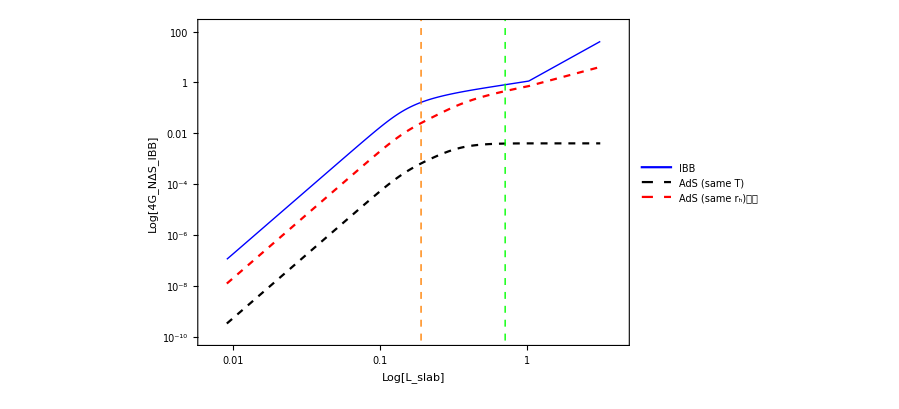
```mathematica
-Graphics-_□
```

## CHANGING α : 2 -- -> 4

```mathematica
rh = 1;c0=0.95;d=2;α=4;
BCval1 = slngen2[c0,rh,d,α,1,1,1]
BCval2 = slngen2[c0,rh,d,α,Sqrt[BCval1[[4]]],1/BCval1[[1]],1]
sln = slnhold2[c0,rh,d,α,Sqrt[BCval1[[4]]],1/BCval1[[1]],1]
L= 1;

(* CALCULATE THE ENTANGLEMENT ENTROPY AND THE SIZE OF THE SLAB OF THE INTERPOLATING BLACK BRANES AS A FUNCTION OF u = 1/r. THE GOAL OF THIS IS TO PICK THE LEAST UNSTABLE SOLUTIONS UNDER NUMERICAL INTERPOLATION.  *)
Clear[Lslab, ΔSIBB,ΔSIBBr,xIBB,xIBBr,Lslab,Lslabr]

ΔSIBB[us_, d_ ]:= Re[NIntegrate[1/u^3*( sln[[2]][1/u]-1)/(Sqrt[1-(u/us)^(2*d)]), {u, 1/BCval2[[-1]], us}]]
Lslab[us_, d_ ]:= Re[-L^2*NIntegrate[-( sln[[2]][1/u])/(Sqrt[(us/u)^(2*d)-1]), {u, 1/BCval2[[-1]], us}]]

(* CALCULATION OF THE ADS BLACK BRANE AT THE SAME r_h and the same temperature *)

RSmax =BCval1[[-1]];

(* CALCULATION OF THE ENTROPY OF THE ADS BLACK BRANE AT THE SAME RADIUS OF HORIZON AS OUR INTERPOLATING BLACK BRANE *) 
Cads[r_, rh_, d_]:= (L/(r*Sqrt[1-(rh/r)^(d+1)]))^2 (* PURE ADS FIELD VALUES *)
ΔSAdS1[us_, d_ ]:= Re[NIntegrate[1/u^3*(C1AdS[1/u,d, rh]-1)/(Sqrt[1-(u/us)^(2*d)]), {u, 1/BCval2[[-1]], us}]] 


(* EXTRACTING THE RADIUS OF HORIZON FOR THE ADS BLACK BRANE AT THE SAME TEMPERATURE AS OUR INTERPOLATING BLACK BRANE *)
ThAds[rh_,d_]:= Sqrt[(D[Aads[r,rh1,d],r]/.r->rh1)*(D[1/Cads[r,rh1,d],r]/.r->rh1)]/(4*Pi)
rHAds = N[Solve[ThAds[rh, 3]==BCval1[[6]],rh1][[2,1,2]]]

C1AdS[r_, d_,rh1_]:= 1/Sqrt[1-(rh1/r)^(d+1)] (* VALUES OF THE FIELD VALUES FOR ADS BLACK BRANE AT THE SAME TEMPERATURE *)
(* CALCULATION OF THE ENTROPY OF THE ADS BLACK BRANE AT THE TEMPERATURE AS OUR INTERPOLATING BLACK BRANE *) 
ΔSAdS[us_, d_ ]:= Re[NIntegrate[1/u^3*(C1AdS[1/u,d, rHAds]-1)/(Sqrt[1-(u/us)^(2*d)]), {u, 1/BCval2[[-1]], us}]]

(* PLOT *)
If[rHAds<rh, rIntAdS = rh, rIntAdS =rHAds]; (* Set the range of the AdS brane, so that we do not plot the divergence point where r = rh. *)
Legended[Show[ (* PLOT THE ENTANGLEMENT ENTROPY VS L_slab FOR THE AdS black branes(ABB) at the same temperature and same radius of horizon *)ParametricPlot[{Lslab[us,d],ΔSAdS[us, d]},{us, 1/RSmax, 1/rIntAdS },ScalingFunctions->{"Log","Log"},Epilog->{{Green,Thick, Dashed, Line[{{Log[BCval1[[5]]],-100},{Log[BCval1[[5]]],100}}]},{Orange, Thick,Dashed, Line[{{Log[ BCval1[[6]]],-100},{ Log[BCval1[[6]]],100}}]}},PlotStyle->{Dashed, Black},  Frame->True ,FrameTicks->All,FrameLabel->{Style["Log[L_slab]",Black, 25],Style[ "Log[4G_NΔS_IBB]",Black, 25]},FrameTicksStyle->Directive[Black,20],Axes->False, Mesh->False,AspectRatio->1/GoldenRatio],ParametricPlot[{Lslab[us,d],ΔSAdS1[us, d]},{us, 1/RSmax, 1/rh },ScalingFunctions->{"Log","Log"},Epilog->{{Green,Thick, Dashed, Line[{{Log[BCval1[[5]]],-100},{Log[BCval1[[5]]],100}}]},{Orange, Thick,Dashed, Line[{{Log[ BCval1[[6]]],-100},{ Log[BCval1[[6]]],100}}]}},PlotStyle->{Dashed, Red},  Frame->True ,FrameTicks->All,FrameLabel->{Style["L_slab",Black, 25],Style[ "4G_N ΔS",Black, 25]},FrameTicksStyle->Directive[Black,20],RotateLabel->{False,True},Axes->False, Mesh->False,AspectRatio->1/GoldenRatio], (* PLOT THE ENTANGLEMENT ENTROPY VS L_SLAB FOR THE INTERPOLATING BLACK BRANE (IBB) *)ParametricPlot[{Lslab[us,d],ΔSIBB[us, d]},{us, 1/RSmax, 1/rh},ScalingFunctions->{"Log","Log"},Epilog->{{Red,Thick, Dashed, Line[{{Log[BCval1[[5]]],-100},{Log[BCval1[[5]]],100}}]},{Orange, Thick,Dashed, Line[{{Log[ BCval1[[6]]],-100},{ Log[BCval1[[6]]],100}}]}},PlotStyle->{Thick, Blue}, Frame->True ,FrameTicks->All,FrameLabel->{Style["Log[L_slab]",Black, 25],Style[ "Log[4G_NΔS_IBB]",Black, 25]},FrameTicksStyle->Directive[Black,20],Axes->False, Mesh->False,AspectRatio->1/GoldenRatio], PlotRange->All, ImageSize->1000],Placed[LineLegend[{Blue,{Dashed, Black},{Dashed,Red}}, {"IBB","AdS (same T)","AdS (same r_h)"}, LegendLayout->"Column", LegendMarkerSize->25,LabelStyle->{Black, FontSize->25, Font-> "Arial"}, LegendFunction->Framed],{0.17, 0.82}]]
```

{1.37888,1.,15.3783,41.3404,1.73457,0.173135,10.0186,10000.}

{0.999998,1.,1.73324,0.999955,1.73328,0.173135,10.0111,10000.}

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

0.543918

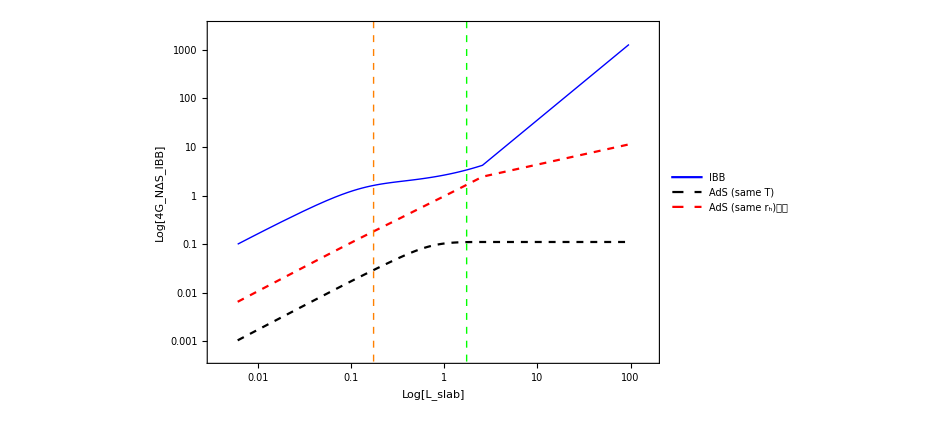

# SCRAP FILES

8.49562

```mathematica
d = 3; α = 3; rh = 1; c0 = 0.25; L=1;
BCval1 = slngen[c0,rh,d,α,1,1];
BCval2 = slngen[c0,rh,d,α,Sqrt[BCval1[[4]]],1/BCval1[[1]]]
sln = slnhold[c0,rh,d,α,Sqrt[BCval1[[4]]],1/BCval1[[1]]]
ΔSIBB[us_, d_ ]:= Re[NIntegrate[1/u^3*( sln[[2]][1/u]-1)/(Sqrt[1-(u/us)^(2*d)]), {u, 1/BCval2[[-1]], us}]]
Lslab[us_, d_ ]:= Re[-L^2*NIntegrate[-( sln[[2]][1/u])/(Sqrt[(us/u)^(2*d)-1]), {u, 1/BCval2[[-1]], us}]]
dSdl[μ_, d_]:=Module[{usStart, usEnd, maxstep, delus, ListData,i,res, S2,L2,L1,S1,stepPrint},
usStart =μ-0.2;
usEnd = μ+0.5;
maxstep = 2000;
delus = (usEnd -usStart)/maxstep ;
ListData = {};
stepPrint = 100;
S2 = ΔSIBB[usStart, d];
L2 = Lslab[usStart, d];
For[i=1,i<=maxstep,i++,If[i==stepPrint,Print[i]; stepPrint=stepPrint +300;, Continue];S1=S2; L1=L2; S2 = ΔSIBB[usStart+i*delus, d];L2 = Lslab[usStart+i*delus, d];res = AppendTo[ListData,{(L2-L1)/2+L1,(S2-S1)/(L2-L1)}]];
res]
dSList = dSdl[BCval1[[5]], 3];
```

{1.,1.,0.295571,1.00001,0.295569,0.300027,0.985141,1000.}

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

100

400

700

1000

1300

1600

1900

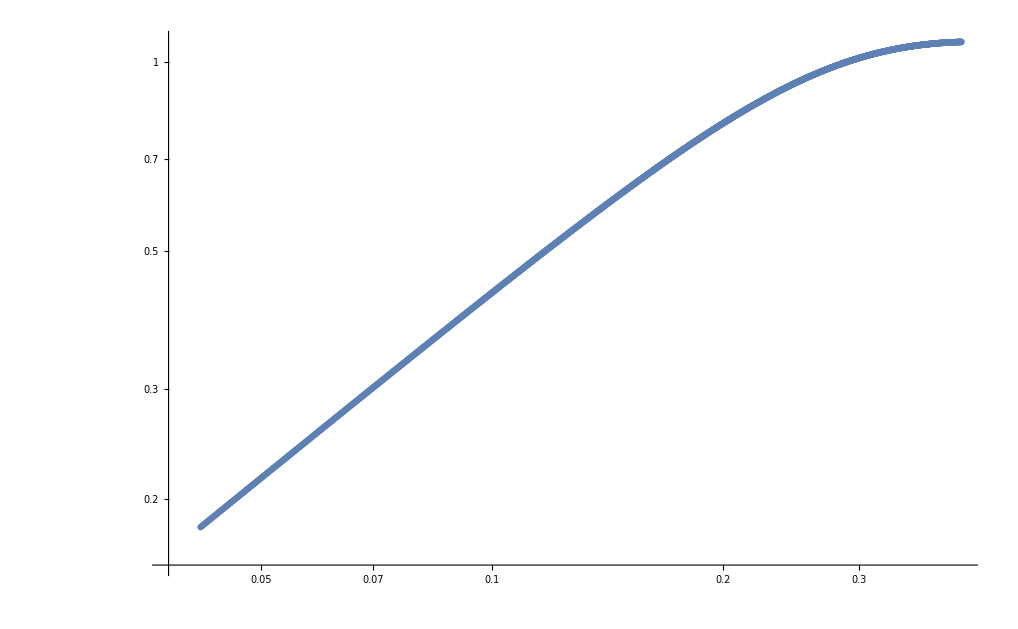

```mathematica
ListLogLogPlot[dSList]
```

```mathematica
Length[dSList]
```

2000

```mathematica
dSList[[1,2]]
```

0.18096

```mathematica
d2Sdl2[list_]:=Module[{usStart, usEnd, maxstep, delus, ListData,i,res, S2,L2,L1,S1},
maxstep = Length[list];
ListData = {};
For[i=1, i<=maxstep-1,i++,L2 =dSList[[i+1,1]] ;L1 =list[[i,1]];S2 = list[[i+1,2]];S1 =list[[i,2]];res = AppendTo[ListData,{(L2-L1)/2+L1,(S2-S1)/(L2-L1)}]];
res]
newList = d2Sdl2[dSList];
```

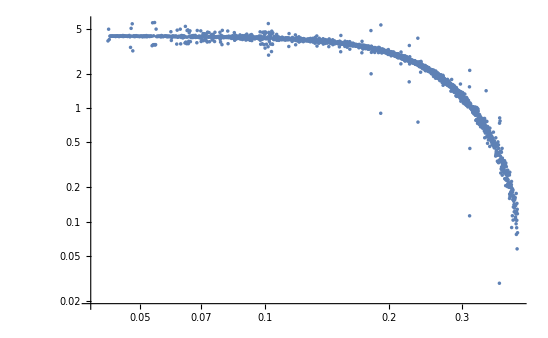

```mathematica
ListLogLogPlot[newList]
```

```mathematica
(0.5+0.2)/2000
```

0.00035

```mathematica
ScientificForm[0.00035]
```

3.5×10^-4

# Scrap!

```mathematica
(* 
CreateData[rh_, d_]:= Module[{i, imax, dataList, rsStart,rsEnd,stepsize},
dataList = {};
imax = 500;
rsEnd= 2*rh;
rsStart=(rh+0.0001);
stepsize=(rsStart-rsEnd)/imax;

For[i = 1, i < imax, i++, AppendTo[dataList,{rsStart*i*stepsize,(Abs[Sa[rsStart*i*stepsize, d]]-Abs[SaAds[rsStart*i*stepsize,rh,d]])/Abs[SaAds[rsStart*i*stepsize,rh,d]]}]];
dataList
]
*)
```

```mathematica
CreateData[1,3]
```

```mathematica
Clear[dataset]
dataset[rh_, d_, α_, Qh_, facD0h_]:= Module[{c0hscan,c0hindex, i, muout, Tout,c0out, sln, emptyList, imax},
c0hscan = 0.01;
imax = 20;
emptyList = {};
For[i=1,i<imax, i++, AppendTo[emptyList, Flatten[{{c0hscan*(1/0.01)^(i/(imax-1))}, slngen[c0hscan*(1/0.01)^(i/(imax-1)), rh, d,α, Qh,facD0h]}]]]
emptyList/Null (* Because Mathematica is fucking shit!!! *)
];
```

```mathematica
(* Add a scaling parameter to the initial BC condition to get a convergent to rmax... *)
slnhold4[c0h_, rh_, d_,α_, Qh_,facD0h_, scaleRinit_]:= Module[{E1,E2,E3,E4,E41,eAseed,eCseed,eGseed,IePhseed,ePhiseed,c0,D0h, a0, a1, c1,g0, g1,rIni,eOm,bc,eq,rmax,a,sol,e2aPhi, Qhlocal},
(* EoM *)
E1= D[eA1[r],r]-eC1[r]*N[(D0h+2*d*eG1[r]*α*Qhlocal)/(d*r^2(r^d)*α),50];
E2= D[eC1[r],r]+N[eC1[r]^2*(2*Qhlocal*eG1[r]*eA1[r]*r^d*r*α*d-2*eC1[r]*Qhlocal^2*eG1[r]^2*α^3+D0h*eA1[r]*r^d*r)/(r^3*(r^d)^2*eA1[r]^2*d*α),50];
E3=D[eG1[r],r]-N[1/(2)*1/(r^2*eC1[r]*eA1[r]*Qhlocal*α*r^d)*(d*(r^(2*d))*r^2*α*(eC1[r]^2-1)*(d+1)*eA1[r]^2-2*eC1[r]*r^(d+1)*(D0h+2*d*eG1[r]*α*Qhlocal)*eA1[r]+2*eC1[r]^2*eG1[r]^2*α^3*Qhlocal^2),50];
E4 = D[ePhi[r],r]-N[Simplify[D[1/(2*r^2*Qhlocal^2*α*eA2[r]*eC2[r])*(d*r^(2*d+2)*α*(d+1)*(eA2[r]*eC2[r]-eA2[r]/eC2[r])-2*r^(d+1)*D0h-4*d*r^(d+1)*eG2[r]*α*Qhlocal+2*α*eC2[r]/eA2[r]*α^2*Qhlocal^2*eG2[r]^2)/.eA2->eA1/.eC2->eC1/.eG2->eG1 ,r]/.eA1'[r]->eC1[r]*(D0h+2*d*eG1[r]*α*Qhlocal)/(d*r^2(r^d)*α)/.eC1'[r]->-eC1[r]^2*(2*Qhlocal*eG1[r]*eA1[r]*r^d*r*α*d-2*eC1[r]*Qhlocal^2*eG1[r]^2*α^3+D0h*eA1[r]*r^d*r)/(r^3*(r^d)^2*eA1[r]^2*d*α)/.eG1'[r]->1/(2)*1/(r^2*eC1[r]*eA1[r]*Qhlocal*α*r^d)*(d*(r^(2*d))*r^2*α*(eC1[r]^2-1)*(d+1)*eA1[r]^2-2*eC1[r]*r^(d+1)*(D0h+2*d*eG1[r]*α*Qhlocal)*eA1[r]+2*eC1[r]^2*eG1[r]^2*α^3*Qhlocal^2)],50];

E41= D[IePh[r],r]-N[2*r^2/(α*d*r^(2*d+2)*eA1[r]*eA1[r]*(eC1[r]-1)*(eC1[r]+1)*(d+1)-2*r^(d+1)*eC1[r]*eA1[r]*(D0h+2*d*eG1[r]*α*Qhlocal)+2*eC1[r]^2*eG1[r]^2*α^3*Qhlocal^2)*eA1[r]^2*eC1[r]^2*Qhlocal^2*α,50];

(* e^(2*α*ϕ[r]) as defined by 76 *)
(* WE WILL SEE LATER WHY WE DEFINED eA2 instead of eA1 and so on *)

(* e2aPhi[r_]:= 2*r^2/(α*d*r^(2*d+2)*eA2[r]^2*(eC2[r]-1)*(eC2[r]+1)*(d+1)-2*r^(d+1)*eC2[r]*eA2[r]*(D0h+2*d*eG2[r]*α*Qhlocal)+2*eC2[r]^2*eG2[r]^2*α^3*Qhlocal^2)*eA2[r]^2*eC2[r]^2*Qhlocal^2*α;
*)
(* Seed Functions *)
eAseed[r_]:= N[a0*(Sqrt[r-rh]+a1*(r-rh)^(3/2)),50];
eCseed[r_]:=N[c0/(Sqrt[r-rh])+c1*Sqrt[r-rh],50];
eGseed[r_]:= N[a0*(g0*(r-rh)+g1*(r-rh)^2),50];
(* E^(2*α*ϕ[r])=ePh[r]; *)
IePhseed[r_]:= N[1,50];
ePhiseed[r_]:= 1/(2*r^2*Qh^2*α*eAseed[r]*eCseed[r])*(d*r^(2*d+2)*α*(d+1)*(eAseed[r]*eCseed[r]-eAseed[r]/eCseed[r])-2*r^(d+1)*D0h-4*d*r^(d+1)*eGseed[r]*α*Qh+2*α*eCseed[r]/eAseed[r]*α^2*Qh^2*eGseed[r]^2); 
(* Coefficient of the seed functions *)
a0 = 2*rh^(-2-d)*c0*D0h/(d*α); a1 = (α^2*d*(d+1)^2*c0^4-2*d*rh*(α^2-2)*(d+1)*c0^2+rh^2*α^2*d-4*rh^2-6*d*rh^2)/(8*rh^3);
c1 =c0*(3*α^2*d*(d+1)^2*c0^4-2*d*rh*(3*α^2+2)*(d+1)*c0^2+3*rh^2*α^2*d+4*rh^2+6*d*rh^2)/(8*rh^3);
g0 = d*(c0^2*d+c0^2-rh)/(2*rh^(-d)*c0*Qhlocal); g1 = d^2*(rh^(-2+d)*α^2*(d+1)^3*c0^6-rh^(d-1)*α^2*(d+1)^2*c0^4-rh^(d)*(α^2+2)*(d+1)*c0^2+rh^(d+1)*α^2+2*rh^(d+1))/(8*Qhlocal*rh*c0);
(* Some conditions on Qh and c0, D0h *)
c0 = N[(c0h*((Sqrt[α^2+2]-α)/(α))*Sqrt[rh]+Sqrt[rh])/(Sqrt[d+1]),50];
D0h=N[1/2*rh^(d+1)*(d+1)*d*α*facD0h,50];
Qhlocal = N[Qh, 50];
 rIni =N[rh+rh*1*^-10,50];
(* NSolve *)
eOm = {E1==0,E2==0, E3==0, E4==0,E41==0};
bc = N[{eA1[rIni]==eAseed[rIni], eC1[rIni]==eCseed[rIni], eG1[rIni]==eGseed[rIni],IePh[rIni]== IePhseed[rIni], ePhi[rIni]==ePhiseed[rIni]},50];
eq = Flatten[{eOm, bc}];
a = (12/(d+1))*rh;
rmax =2* 10^(12/(d+1))*rh;
sol =NDSolve[eq, {eA1[r],eC1[r], eG1[r],ePhi[r]},{r,rh+rh*1*^-8*scaleRinit,rmax}, MaxSteps->1000000,WorkingPrecision->MachinePrecision];
(* Give back eA1, eC1, eG1 and e^(2*α*ϕ[r]) *)
List[sol[[1,1,2,0]],sol[[1,2,2,0]],sol[[1,3,2,0]],sol[[1,4,2,0]]]
]
```

## I THOUGHT THAT THE VALUE OF MU WAS THE VALUE GIVEN WITH THE CORRECT ASYMPTOPIC PARAMETERS. THIS IS WRONG HOWEVER.

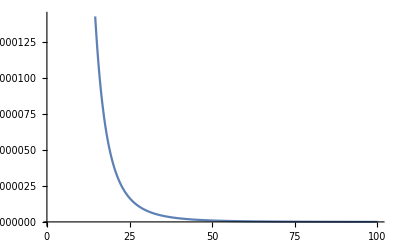
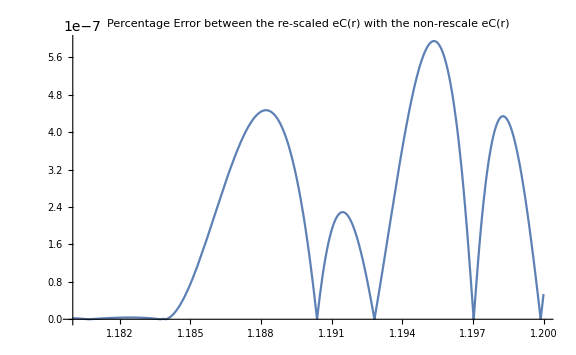
```mathematica
slngenAsypm[c0h_, rh_, d_,α_]:= Module[{sln,sln2, rmax, eA1val,eA1val1, eC1val, eG1val,ePval1,ePval, mu, T, c0, D0h, Qhlocal,e2aPhi,facD0h}, 
sln = slngen[c0h, rh, d,α, 1,1];
eA1val1 = sln[[1]];
ePval1 = sln[[4]];

Qhlocal = Sqrt[ePval1];
facD0h = 1/eA1val1;
sln2 = slngen[c0h, rh, d,α, Sqrt[ePval1],facD0h ];

rmax =   sln2[[-1]];(* 10^(12/(d+1)); *)
eA1val = sln2[[1]];
eC1val = sln2[[2]];
eG1val = sln2[[3]];
ePval = sln2[[4]];
(* Value of the dilaton. Note we need to eA2 to express as a function of eA1 *)
mu = eG1val/eA1val*Sqrt[ePval];

(* Some conditions on Qh and c0, D0h *)
c0 = (c0h*((Sqrt[α^2+2]-α)/(α))*Sqrt[rh]+Sqrt[rh])/(Sqrt[d+1]);
D0h=1/2*rh^(d+1)*(d+1)*d*α*facD0h;
T = 1/2*D0h/(α*d*(rh^d)*Pi*eA1val);
List[N[eA1val,10], N[eC1val,10], N[eG1val,10], N[ePval,10], N[mu,10], N[T,10], N[mu,10]/ N[T,10],Qhlocal,facD0h , rmax]
];


getc0hAsymp[μ_,rh_,d_,α_]:= Module[{stepsize, c0hmin,c0hmax,delc0h,c0hholder, muholder,muholder2,muholder3,difmu,c0hindex,i,slnout,a,difmu3,Qhlocal,facD0h},
a=1;
c0hmin  =0;(* AdS *)
c0hmax =1; (* Lifshitz *)
delc0h = N[c0hmax - c0hmin];
c0hindex = c0hmin;
muholder2 =12*μ;
difmu = μ-muholder2;
muholder3=-1;
difmu3=μ-muholder3;
i=1;
While[Abs[difmu]>μ*10^(-4),
If[i<=100,
muholder = slngenAsypm[N[c0hindex+a*(0.500000)^(i)*delc0h,50], rh, d, α][[5]];Qhlocal = slngenAsypm[N[c0hindex+a*(0.500000)^(i)*delc0h,50], rh, d, α][[8]];
facD0h = slngenAsypm[N[c0hindex+a*(0.500000)^(i)*delc0h,50], rh, d, α][[9]];
If[Sign[muholder-μ]==-1 && If[muholder3<μ, muholder>=muholder3, True] (* make sure that the new diffmu is always smaller than the previous one *), Print[{"A",i=i,rh,c0hindex = N[c0hindex+a*(0.500000)^(i)*delc0h,10],muholder2=muholder, difmu = Abs[μ-muholder2]}]; difmu3=μ-muholder;muholder3=N[muholder2,50] (* Change the value of μ *),Print[{"B",i=i,rh,c0hindex=c0hindex, muholder,difmu=difmu}];difmu3=μ-muholder]  (* Does not change the value of μ, but leads to a smaller c0h *), (* If i > 100 ie no convergence *)If[c0hindex != 0  (* sometimes your operation always produce the B print. If this is the case, quit the while loop *),If[Sign[difmu3]==-1  (* if diffmu3 < 0, so muholder that you have is LARGER than μ you need, then you need a SMALLER muholder, so you've got to go more towards AdS c0hindex = 0 *),delc0h=Abs[c0hindex-c0hindex/2]; c0hindex=0;a=1; i=1 ,(* if diffmu3 > 0, so muholder that you have is SMALLER than μ you need, then you need a LARGER muholder, so you've got to go more towards Lifshitz c0hindex = 1 *)delc0h=Abs[5*c0hindex-c0hindex];c0hindex=c0hindex;a=1;i=1],Abs[difmu] =1/100* μ*10^(-4)]];i=i+1];
slnout = slngenAsypm[c0hindex,rh,d,α];
Flatten[{c0hindex, rh,slnout}]
]


datasetmuAsymp[μ_,d_,α_]:= Module[{rhscan, rhindex, i, muout, Tout, sln, c0hout,emptyList, c0start},
rhscan = 0.1;
emptyList = {};
For[i=0, i<=10, i++,sln=getc0hAsymp[μ,rhscan*(10)^(i/10),d,α]; AppendTo[emptyList,{rhscan*(10)^(i/10),μ, sln[[7]], sln[[8]],sln[[9]], c0hout=sln[[1]],sln}]];
emptyList
]
Here I compare the solution for eC(r) with re-scaled parameters versus the one without re-scaling the parameters to see if there would be a big change in the calculation of the entanglement entropy.ANS:No
sln = slnhold[0.2511886431509580111085032067799327394149,1,3,2,1/Sqrt[1.011798090932956341869486153552574498287], 1/1.1319946936580036]
sln2 = slnhold[0.2511886431509580111085032067799327394149,1,3,2,1, 1]
Plot[sln2[[2]][r],{r,1.1,100}]
Plot[{100*Abs[sln[[2]][r]-sln2[[2]][r]]/sln2[[2]][r]},{r, 1.18, 1.2}, PlotLabel->"Percentage Error between the re-scaled eC(r) with the non-rescale eC(r)", ImageSize->Large]
{InterpolatingFunction[{{1., 1000.}}, <>],InterpolatingFunction[{{1., 1000.}}, <>],InterpolatingFunction[{{1., 1000.}}, <>],1/(u^2 eA2[u] eC2[u])0.2529495227332390854673715383881436245717500000000000000001`39.00509385564374 (-21.201512811376162 u^4+24 u^8 (-eA2[u]/eC2[u]+eA2[u] eC2[u])-23.8596634724057353346487742033648304598338384718264663310918`39.306123851307724 u^4 eG2[u]+(15.8134316949014586630834091328050567337929814649853406152792`39.00509385564374 eC2[u] eG2[u]^2)/eA2[u])}
NDSolve::mxst: "Maximum number of \!\(\*RowBox[{\"500000\"}]\) steps reached at the point \!\(\*RowBox[{\"r\"}]\) == \!\(\*RowBox[{\"166.82166508907383`\"}]\)."
{InterpolatingFunction[{{1., 166.822}}, <>],InterpolatingFunction[{{1., 166.822}}, <>],InterpolatingFunction[{{1., 166.822}}, <>],1/(u^2 eA2[u] eC2[u])0.25`49.69897000433602 (-24.`50. u^4+24 u^8 (-eA2[u]/eC2[u]+eA2[u] eC2[u])-24.`50. u^4 eG2[u]+(16.`49.69897000433602 eC2[u] eG2[u]^2)/eA2[u])}
-Graphics-
-Graphics-
```

# Circular Photon Orbits:

## Geodesic Calculations to get Veff(r)

```mathematica
Clear[ChristoffelSymbol,RiemannTensor,RicciTensor,RicciScalar,einstein,metricF, Lap, geodesic]
ChristoffelSymbol[g_,coord_,d_]:=Block[{n,ig,res},n=d;ig=Simplify[Inverse[g]];
res=Table[(1/2)*Sum[ig[[λ,σ]]*(-D[g[[μ,ν]],coord[[σ]]]+D[g[[μ,σ]],coord[[ν]]]+D[g[[σ,ν]],coord[[μ]]]),{σ,1,n} (* Sum over the dummy indice σ *)],{λ,1,n},{μ,1,n},{ν,1,n} (* Calculate all values of the christoffel symbol and place them in a 3x3x3 matrix*)];
Simplify[res]]
RiemannTensor[g_,coord_,d_]:=Block[{n,Chr,res},n=d;Chr=ChristoffelSymbol[g,coord,d];
res=Table[D[Chr[[λ,μ,σ]],coord[[ν]]]-D[Chr[[λ,μ,ν]],coord[[σ]]]+Sum[Chr[[λ,κ,ν]]*Chr[[κ,μ,σ]],{κ,1,n}]-Sum[Chr[[λ,κ,σ]]*Chr[[κ,μ,ν]],{κ,1,n}],{λ,1,n},{μ,1,n},{ν,1,n},{σ,1,n}];
Simplify[res]]
RicciTensor[g_,coord_,d_]:=Block[{Rie,res,n},n=d;Rie=RiemannTensor[g,coord,d];
res=Table[Sum[Rie[[λ,μ,λ,ν]],{λ,1,n} (* Sum over the dummy indice λ*)],{μ,1,n},{ν,1,n}];
Simplify[res]]
RicciScalar[g_,coord_,d_]:=Block[{Ricc,ig,res,n},n=d;Ricc=RicciTensor[g,coord,d];ig=Simplify[Inverse[g]];
res=Sum[ig[[s,i]] Ricc[[s,i]],{s,1,n},{i,1,n}];
Simplify[res]]
einstein:=einstein = Simplify[RicciTensor[metric,coord,Length[coord]]-1/2* RicciScalar[metric,coord,Length[coord]]*metric]


metricF[coord_]:=Module[{metric},metric = Table[g[coord[[i]],coord[[j]]],{i,1,Length[coord]},{j,1, Length[coord]}];Do[Subscript[a,coord[[i]],coord[[j]]]=0,{i,1,Length[coord]},{j,1, Length[coord]}]; metric];

Lap[g_, coord_, Ψ_]:=1/Sqrt[Det[g]]*Sum[D[Sqrt[Det[g]]*Simplify[Inverse[g]][[a,b]]*D[Ψ,coord[[b]]],coord[[a]]],{a,1,Length[coord]},{b,1,Length[coord]}]

(* TIMELIKE IS ϵ = -1 *)
geodesic[g_,coord_,d_]:= Block[{n,Chr, newCoord,newMetric,res1,res2,res,ϵ, τ, f},n=d;
(* DEFINE NEW COORDINATE as a function of the affine param. r-> r[τ] and express the metric in terms of r[τ] instead of r *)
newCoord = {};
For[i=1, i < Length[coord]+1, i++,AppendTo[newCoord, coord[[i]][τ]]];
f[x_,y_]:=x->y;
newMetric = g/. MapThread[f, {coord,newCoord}];
(* Compute the geodesics equations *)
Chr=ChristoffelSymbol[newMetric,newCoord,d];
res1 = {Sum[newMetric[[μ,ν]]*D[newCoord[[μ]],τ]*D[newCoord[[ν]],τ], {μ,1,n},{ν,1,n}]==ϵ}; (* ds^2 = ϵ *)
res2 = Table[D[D[newCoord[[μ]], τ],τ]+Sum[Chr[[μ,α,β]]*D[newCoord[[α]],τ]*D[newCoord[[β]],τ],{α, 1, n},{β,1,n}]==0,{μ, 1,n}];(* x'' + Γ x'x' == 0  *)
res = Join[res1,res2];
res
]
```

```mathematica
Clear[listriemann,listricci,listChristoffel,listeinstein,listgeodesic, n, coord, g,metric, inversemetric, r,t, θ1,θ2,θ3]
coord={t,r, θ1,θ2,θ3};
d =3; L=1;
g[μ_,ν_]:=Subscript[a,μ,ν]
ConFact = 1; (* Conformal Factor *)
g[t,t]=-(L*r)^2*(1-(rh/r)^(d+1));
g[r,r]= (L/r)^2*(1-(rh/r)^(d+1))^(-1);
g[θ1,θ1]=(L*r)^2;
g[θ2,θ2]=(L*r)^2*Sin[θ1]^2;
g[θ3,θ3]=(L*r)^2*Sin[θ1]^2*Sin[θ2]^2;
metric = metricF[coord];
metric//MatrixForm
inversemetric=Simplify[Inverse[metric]] ;
inversemetric //MatrixForm;
```

(-r^2 (1-rh^4/r^4) | 0 | 0 | 0 | 0
0 | 1/(r^2 (1-rh^4/r^4)) | 0 | 0 | 0
0 | 0 | r^2 | 0 | 0
0 | 0 | 0 | r^2 Sin[θ1]^2 | 0
0 | 0 | 0 | 0 | r^2 Sin[θ1]^2 Sin[θ2]^2)

```mathematica
geodesic[metric,coord,Length[coord]];
listgeodesic:= Table[{StringJoin[ToString[Join[{ϵ}, coord][[μ]]],":"], geodesic[metric, coord, Length[coord]][[μ]]},{μ,1,Length[coord]+1}]
TableForm[Partition[DeleteCases[Flatten[listgeodesic (* Flatten just removes the inner list of the table*)],Null (* Do not print the element that are zero*)],2],TableSpacing->{3,3}]
```

ϵ: | r'[τ]^2/((1-rh^4/r[τ]^4) r[τ]^2)-(1-rh^4/r[τ]^4) r[τ]^2 t'[τ]^2+r[τ]^2 θ1'[τ]^2+r[τ]^2 Sin[θ1[τ]]^2 θ2'[τ]^2+r[τ]^2 Sin[θ1[τ]]^2 Sin[θ2[τ]]^2 θ3'[τ]^2==ϵ
t: | (2 (rh^4+r[τ]^4) r'[τ] t'[τ])/(-rh^4 r[τ]+r[τ]^5)+t''[τ]==0
r: | ((rh^4+r[τ]^4) r'[τ]^2)/(rh^4 r[τ]-r[τ]^5)+(-rh^8/r[τ]^5+r[τ]^3) t'[τ]^2+((rh^4-r[τ]^4) θ1'[τ]^2)/r[τ]+((rh^4-r[τ]^4) Sin[θ1[τ]]^2 θ2'[τ]^2)/r[τ]+((rh^4-r[τ]^4) Sin[θ1[τ]]^2 Sin[θ2[τ]]^2 θ3'[τ]^2)/r[τ]+r''[τ]==0
θ1: | (2 r'[τ] θ1'[τ])/r[τ]-Cos[θ1[τ]] Sin[θ1[τ]] θ2'[τ]^2-Cos[θ1[τ]] Sin[θ1[τ]] Sin[θ2[τ]]^2 θ3'[τ]^2+θ1''[τ]==0
θ2: | (2 r'[τ] θ2'[τ])/r[τ]+2 Cot[θ1[τ]] θ1'[τ] θ2'[τ]-Cos[θ2[τ]] Sin[θ2[τ]] θ3'[τ]^2+θ2''[τ]==0
θ3: | (2 r'[τ] θ3'[τ])/r[τ]+2 Cot[θ1[τ]] θ1'[τ] θ3'[τ]+2 Cot[θ2[τ]] θ2'[τ] θ3'[τ]+θ3''[τ]==0

```mathematica
r'[τ]^2/((1-rh^4/r[τ]^4) r[τ]^2)-(1-rh^4/r[τ]^4) r[τ]^2 t'[τ]^2+r[τ]^2 θ1'[τ]^2+r[τ]^2 Sin[θ1[τ]]^2 θ2'[τ]^2+r[τ]^2 Sin[θ1[τ]]^2 Sin[θ2[τ]]^2 θ3'[τ]^2==ϵ/.t'[τ]->b/(-r^2 (1-rh^4/r[τ]^4))/.θ3'[τ]->lh/((L*r[τ])^2)/.θ2'[τ]->0/.θ1'[τ]->0/.θ1[τ]->Pi/2/.θ2[τ]->Pi/2
```

lh^2/r[τ]^2-(b^2 r[τ]^2)/(r^4 (1-rh^4/r[τ]^4))+r'[τ]^2/((1-rh^4/r[τ]^4) r[τ]^2)==ϵ

## Calculations of Veff and Rs (Rs is the radius for which d Veff / dr = 0)

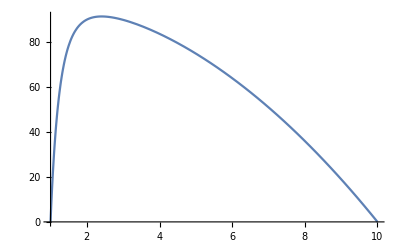

{{r==0.-2.40646 ⅈ},{r==0.+2.40646 ⅈ},{r==-2.09431+1.22091 ⅈ},{r==2.09431-1.22091 ⅈ},{r==-2.09431-1.22091 ⅈ},{r==2.09431+1.22091 ⅈ}}

{{r==0.-3.79134 ⅈ},{r==0.+3.79134 ⅈ},{r==-3.32472+1.96638 ⅈ},{r==3.32472-1.96638 ⅈ},{r==-3.32472-1.96638 ⅈ},{r==3.32472+1.96638 ⅈ}}

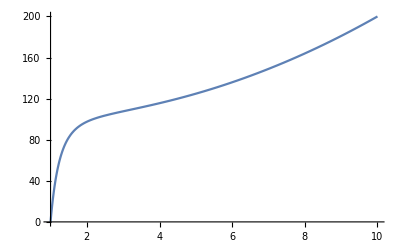

```mathematica
Clear[d,rs,L, rh, ϵ,AA]
d = 3;
Veff[r_,rs_,d_,ϵ_,lh_]:= (-ϵ+lh^2/r^2)*r^2*(1-(rs/r)^(d+1))
Solve[r^(d+3)+(1-d)/2*rh^(d+1)*r^2-(d+1)lh^2/(2*ϵ*L^2)*rh^(d+1)==0, r]/.L->1;
(* *)

rs[ϵ_,rh_,lh_]:= Solve[D[(-ϵ+lh^2/(L*r)^2)*(r/L)^2*(1-(rh/r)^(d+1)),r]==0,r]/.L->1/.Rule->Equal
N[rs[1,rh,10]]/.rh->1;
N[rs[1,rh,10]]/.rh->2;
Plot[Veff[r,1,3,1,10],{r, 1, 10}]

N[rs[-1,rh,10]]/.rh->1
N[rs[-1,rh,10]]/.rh->2
Plot[Veff[r,1,3,-1,10],{r, 1, 10}]
```

```mathematica
Veff[r_,rs_,d_,ϵ_,lh_]:= (-ϵ+lh^2/r^2)*r^2*(1-(rs/r)^(d+1))
```

Plot::plln: Limiting value rs in {r,rs,5} is not a machine-sized real number.

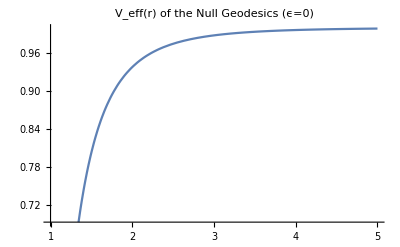

Plot::plln: Limiting value rs in {r,rs,5} is not a machine-sized real number.

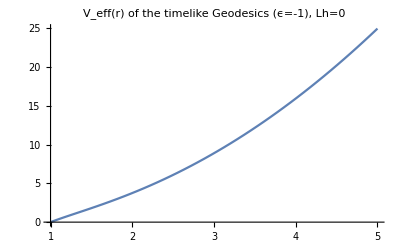

Plot::plln: Limiting value rs in {r,rs,5} is not a machine-sized real number.

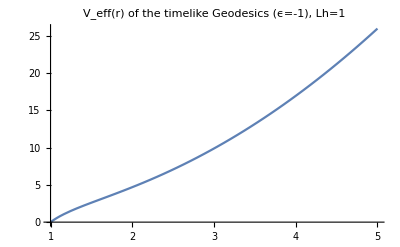

Plot::plln: Limiting value rs in {r,rs,5} is not a machine-sized real number.

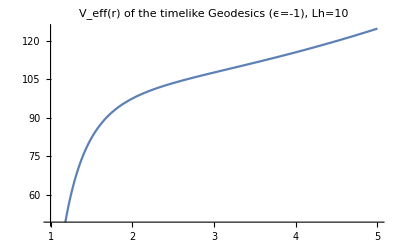

Plot::plln: Limiting value rs in {r,rs,5} is not a machine-sized real number.

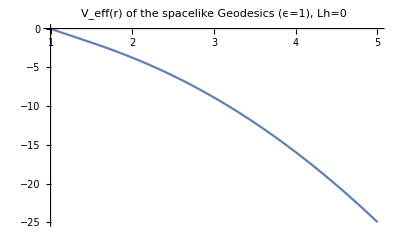

Plot::plln: Limiting value rs in {r,rs,5} is not a machine-sized real number.

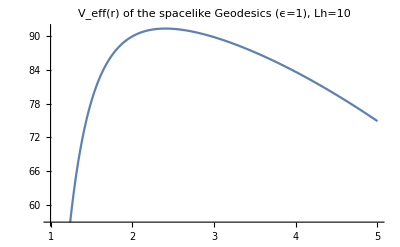

Plot::plln: Limiting value rs in {r,rs,5} is not a machine-sized real number.

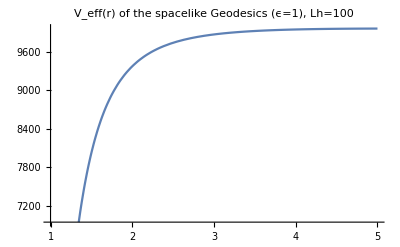

```mathematica
Plot[Veff[r, rs, 3,0,1], {r, rs,5},PlotLabel->"V_eff(r) of the Null Geodesics (ϵ=0)"] /.rs->1
Plot[Veff[r, rs, 3,-1,0], {r, rs,5},PlotLabel->"V_eff(r) of the timelike Geodesics (ϵ=-1), Lh=0"] /.rs->1
Plot[Veff[r, rs, 3,-1,1], {r, rs,5},PlotLabel->"V_eff(r) of the timelike Geodesics (ϵ=-1), Lh=1"] /.rs->1
Plot[Veff[r, rs, 3,-1,10], {r, rs,5},PlotLabel->"V_eff(r) of the timelike Geodesics (ϵ=-1), Lh=10"] /.rs->1
Plot[Veff[r, rs, 3,1,0], {r, rs,5},PlotLabel->"V_eff(r) of the spacelike Geodesics (ϵ=1), Lh=0"] /.rs->1
Plot[Veff[r, rs, 3,1,10], {r, rs,5},PlotLabel->"V_eff(r) of the spacelike Geodesics (ϵ=1), Lh=10"] /.rs->1
Plot[Veff[r, rs, 3,1,100], {r, rs,5},PlotLabel->"V_eff(r) of the spacelike Geodesics (ϵ=1), Lh=100"] /.rs->1
```

```mathematica
rs[1,rh,lh]
```

{{r==-√(-rh^4/(3^(1/3) (9 lh^2 rh^4+√3 √(27 lh^4 rh^8+rh^12))^(1/3))+((9 lh^2 rh^4+√3 √(27 lh^4 rh^8+rh^12))^(1/3))/3^(2/3))},{r==√(-rh^4/(3^(1/3) (9 lh^2 rh^4+√3 √(27 lh^4 rh^8+rh^12))^(1/3))+((9 lh^2 rh^4+√3 √(27 lh^4 rh^8+rh^12))^(1/3))/3^(2/3))},{r==-√(rh^4/(2 3^(1/3) (9 lh^2 rh^4+√3 √(27 lh^4 rh^8+rh^12))^(1/3))-(ⅈ 3^(1/6) rh^4)/(2 (9 lh^2 rh^4+√3 √(27 lh^4 rh^8+rh^12))^(1/3))-((9 lh^2 rh^4+√3 √(27 lh^4 rh^8+rh^12))^(1/3))/(2 3^(2/3))-(ⅈ (9 lh^2 rh^4+√3 √(27 lh^4 rh^8+rh^12))^(1/3))/(2 3^(1/6)))},{r==√(rh^4/(2 3^(1/3) (9 lh^2 rh^4+√3 √(27 lh^4 rh^8+rh^12))^(1/3))-(ⅈ 3^(1/6) rh^4)/(2 (9 lh^2 rh^4+√3 √(27 lh^4 rh^8+rh^12))^(1/3))-((9 lh^2 rh^4+√3 √(27 lh^4 rh^8+rh^12))^(1/3))/(2 3^(2/3))-(ⅈ (9 lh^2 rh^4+√3 √(27 lh^4 rh^8+rh^12))^(1/3))/(2 3^(1/6)))},{r==-√(rh^4/(2 3^(1/3) (9 lh^2 rh^4+√3 √(27 lh^4 rh^8+rh^12))^(1/3))+(ⅈ 3^(1/6) rh^4)/(2 (9 lh^2 rh^4+√3 √(27 lh^4 rh^8+rh^12))^(1/3))-((9 lh^2 rh^4+√3 √(27 lh^4 rh^8+rh^12))^(1/3))/(2 3^(2/3))+(ⅈ (9 lh^2 rh^4+√3 √(27 lh^4 rh^8+rh^12))^(1/3))/(2 3^(1/6)))},{r==√(rh^4/(2 3^(1/3) (9 lh^2 rh^4+√3 √(27 lh^4 rh^8+rh^12))^(1/3))+(ⅈ 3^(1/6) rh^4)/(2 (9 lh^2 rh^4+√3 √(27 lh^4 rh^8+rh^12))^(1/3))-((9 lh^2 rh^4+√3 √(27 lh^4 rh^8+rh^12))^(1/3))/(2 3^(2/3))+(ⅈ (9 lh^2 rh^4+√3 √(27 lh^4 rh^8+rh^12))^(1/3))/(2 3^(1/6)))}}

# Get c0h:

```mathematica
Clear[getc0h]
getc0h[μ_,rh_,d_,α_,Qh_,facD0h_]:= Module[{stepsize, c0hmin,c0hmax,delc0h,c0hholder, muholder,muholder2,muholder3,difmu,c0hindex,i,slnout,a,difmu3},
a=1;
c0hmin  =0;(* AdS *)
c0hmax =1; (* Lifshitz *)
delc0h = N[c0hmax - c0hmin];
c0hindex = c0hmin;
muholder2 =12*μ;
difmu = μ-muholder2;
muholder3=-1;
difmu3=μ-muholder3;
i=1;
While[Abs[difmu]>μ*10^(-1),
If[i<=30,
muholder = slngen[N[c0hindex+a*(0.500000)^(i)*delc0h,50], rh, d, α, Qh, facD0h][[5]];
If[Sign[muholder-μ]==-1 && If[muholder3<μ, muholder>=muholder3, True], Print[{"A",i=i,rh,c0hindex = N[c0hindex+a*(0.500000)^(i)*delc0h,50],muholder2=muholder, difmu = Abs[μ-muholder2], muholder3=N[muholder2,50], difmu3=μ-muholder}],Print[{"B",i=i,rh,c0hindex=c0hindex,difmu=difmu, muholder,difmu3=μ-muholder}]],If[Sign[difmu3]==-1,delc0h=Abs[c0hindex-0]; c0hindex=0;a=1/10; i=1,delc0h=Abs[5*c0hindex-c0hindex];c0hindex=c0hindex;a=1/10;i=1]];i=i+1];
slnout = slngen[c0hindex,rh,d,α,Qh,facD0h];
Flatten[{c0hindex, rh, d, α,slnout}]
]
```

```mathematica
datasetmu[μ_,d_,α_, Qh_,facD0h_]:= Module[{rhscan, rhindex, i, muout, Tout, sln, c0hout,emptyList, c0start},
rhscan = 0.4;
emptyList = {};
For[i=0, i<=10, i++,sln=getc0h[μ,rhscan*(10)^(i/10),d,α,Qh,facD0h]; AppendTo[emptyList,{rhscan*(10)^(i/10),μ, sln[[9]], sln[[10]], c0hout=sln[[1]],sln}]];
emptyList
]
```

```mathematica
slngen[0.00115,1.592428682213989,3,2,1,1]
slngen[0.99,1.592428682213989,3,2,1,1]
```

NDSolve::ndsz: At r == 611.102, step size is effectively zero; singularity or stiff system suspected.

{1.00051,1.,0.0196675,0.0506478,0.00442391,0.506626,611.102}

{4.79087,1.,1663.08,14387.6,41638.4,0.105803,1592.43}

```mathematica
Clear[dataset]
dataset[rh_, d_, α_, Qh_, facD0h_]:= Module[{stepsize,c0hscan,c0hindex, i, muout, Tout,c0out, sln, emptyList, imax},
c0hscan = 0.05;
stepsize = c0hscan;
imax = 50;
emptyList = {};
For[i=1,i<imax, i++, 
Print[Flatten[{{c0hscan*(1/stepsize)^(i/(imax-1))}, slngen[c0hscan*(1/stepsize)^(i/(imax-1)), rh, d,α, Qh,facD0h]}]];
AppendTo[emptyList, Flatten[{{c0hscan*(1/stepsize)^(i/(imax-1))}, slngen[c0hscan*(1/stepsize)^(i/(imax-1)), rh, d,α, Qh,facD0h]}]]];
emptyList
]
dataset[ 5.035701647176669,3,2,1,1]
```

{0.0531522,1.02461,1.,627.745,2511.51,30703.9,1.56442,5035.7}

{0.0565032,1.02621,1.,630.473,2682.28,31818.8,1.56198,5035.7}

NDSolve::ndsz: At r == 2122.23, step size is effectively zero; singularity or stiff system suspected.

{0.0600655,1.02792,1.,56.2188,2865.52,2927.69,1.55938,2122.23}

NDSolve::ndsz: At r == 2122.23, step size is effectively zero; singularity or stiff system suspected.

{0.0638523,1.02974,1.,642.164,3062.44,34510.5,1.55662,5035.7}

NDSolve::ndsz: At r == 2214.92, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

{0.0678779,1.03169,1.,64.2932,3273.94,3565.75,1.55368,2214.92}

{0.0721572,1.03377,1.,68.2145,3501.24,3904.47,1.55055,2096.87}

{0.0767064,1.036,1.,73.0427,3746.1,4315.27,1.54722,2008.13}

{0.0815423,1.03838,1.,644.988,4009.86,39333.4,1.54367,5035.7}

{0.0866832,1.04092,1.,83.4453,4293.96,5253.08,1.5399,2019.47}

{0.0921481,1.04364,1.,89.3644,4600.74,5808.01,1.53589,2028.41}

{0.0979576,1.04655,1.,631.579,4932.17,42382.4,1.53161,5035.7}

{0.104133,1.04967,1.,636.492,5290.48,44104.9,1.52706,5035.7}

{0.110698,1.05301,1.,110.236,5678.34,7888.57,1.52221,2212.91}

{0.117677,1.0566,1.,118.037,6098.74,8724.27,1.51705,2020.94}

{0.125096,1.06044,1.,671.136,6555.2,51240.9,1.51155,5035.7}

{0.132983,1.06457,1.,681.798,7051.39,53779.9,1.5057,5035.7}

{0.141367,1.069,1.,146.336,7591.53,11927.2,1.49945,2146.8}

{0.150279,1.07376,1.,690.559,8180.79,58168.8,1.4928,5035.7}

{0.159754,1.07889,1.,633.52,8824.53,55160.6,1.48571,5035.7}

{0.169825,1.08441,1.,653.213,9529.22,58801.6,1.47814,5035.7}

{0.180532,1.09037,1.,638.329,10302.9,59422.5,1.47007,5035.7}

{0.191914,1.09679,1.,620.969,11153.2,59792.7,1.46146,5035.7}

{0.204013,1.10373,1.,608.471,12091.4,60619.8,1.45227,5035.7}

{0.216875,1.11124,1.,593.759,13128.3,61221.7,1.44245,5035.7}

{0.230548,1.11939,1.,580.057,14278.8,61920.8,1.43196,5035.7}

{0.245083,1.12822,1.,577.673,15558.9,63867.,1.42074,5035.7}

{0.260534,1.13783,1.,569.456,16988.8,65232.5,1.40874,5035.7}

{0.276959,1.1483,1.,570.365,18592.4,67727.3,1.3959,5035.7}

{0.29442,1.15974,1.,571.016,20399.1,70322.5,1.38214,5035.7}

{0.312982,1.17226,1.,574.884,22444.9,73471.1,1.36737,5035.7}

{0.332714,1.186,1.,590.388,24773.9,78352.,1.35153,5035.7}

{0.35369,1.20114,1.,603.534,27440.5,83234.6,1.33449,5035.7}

{0.375988,1.21787,1.,636.113,30517.7,91244.9,1.31616,5035.7}

{0.399692,1.23645,1.,671.582,34096.6,100295.,1.29639,5035.7}

{0.424891,1.25717,1.,727.926,38294.,113308.,1.27502,5035.7}

{0.451678,1.2804,1.,810.299,43271.3,131644.,1.25189,5035.7}

{0.480154,1.30663,1.,890.768,49243.3,151282.,1.22676,5035.7}

{0.510425,1.33646,1.,1025.52,56514.,182417.,1.19937,5035.7}

{0.542605,1.37071,1.,1164.21,65509.8,217390.,1.16941,5035.7}

{0.576813,1.41046,1.,1355.93,76874.9,266544.,1.13644,5035.7}

{0.613179,1.45726,1.,1590.42,91591.8,330296.,1.09995,5035.7}

{0.651836,1.51331,1.,1896.36,111252.,417974.,1.05921,5035.7}

{0.692931,1.582,1.,2328.08,138616.,547897.,1.01322,5035.7}

{0.736617,1.66881,1.,2941.69,178819.,745415.,0.960515,5035.7}

{0.783057,1.78345,1.,3905.87,242657.,1.07883×10^6,0.898773,5035.7}

{0.832425,1.94538,1.,5567.47,356768.,1.70941×10^6,0.823959,5035.7}

{0.884905,2.20237,1.,9099.58,607340.,3.21993×10^6,0.727812,5035.7}

{0.940694,2.7291,1.,20650.,1.47978×10^6,9.20451×10^6,0.587342,5035.7}

{1.,59.5395,1.,1.71436×10^9,3.44374×10^11,1.6897×10^13,0.0269218,5035.7}

{{0.0531522,1.02461,1.,627.745,2511.51,30703.9,1.56442,5035.7},{0.0565032,1.02621,1.,630.473,2682.28,31818.8,1.56198,5035.7},{0.0600655,1.02792,1.,56.2188,2865.52,2927.69,1.55938,2122.23},{0.0638523,1.02974,1.,642.164,3062.44,34510.5,1.55662,5035.7},{0.0678779,1.03169,1.,64.2932,3273.94,3565.75,1.55368,2214.92},{0.0721572,1.03377,1.,68.2145,3501.24,3904.47,1.55055,2096.87},{0.0767064,1.036,1.,73.0427,3746.1,4315.27,1.54722,2008.13},{0.0815423,1.03838,1.,644.988,4009.86,39333.4,1.54367,5035.7},{0.0866832,1.04092,1.,83.4453,4293.96,5253.08,1.5399,2019.47},{0.0921481,1.04364,1.,89.3644,4600.74,5808.01,1.53589,2028.41},{0.0979576,1.04655,1.,631.579,4932.17,42382.4,1.53161,5035.7},{0.104133,1.04967,1.,636.492,5290.48,44104.9,1.52706,5035.7},{0.110698,1.05301,1.,110.236,5678.34,7888.57,1.52221,2212.91},{0.117677,1.0566,1.,118.037,6098.74,8724.27,1.51705,2020.94},{0.125096,1.06044,1.,671.136,6555.2,51240.9,1.51155,5035.7},{0.132983,1.06457,1.,681.798,7051.39,53779.9,1.5057,5035.7},{0.141367,1.069,1.,146.336,7591.53,11927.2,1.49945,2146.8},{0.150279,1.07376,1.,690.559,8180.79,58168.8,1.4928,5035.7},{0.159754,1.07889,1.,633.52,8824.53,55160.6,1.48571,5035.7},{0.169825,1.08441,1.,653.213,9529.22,58801.6,1.47814,5035.7},{0.180532,1.09037,1.,638.329,10302.9,59422.5,1.47007,5035.7},{0.191914,1.09679,1.,620.969,11153.2,59792.7,1.46146,5035.7},{0.204013,1.10373,1.,608.471,12091.4,60619.8,1.45227,5035.7},{0.216875,1.11124,1.,593.759,13128.3,61221.7,1.44245,5035.7},{0.230548,1.11939,1.,580.057,14278.8,61920.8,1.43196,5035.7},{0.245083,1.12822,1.,577.673,15558.9,63867.,1.42074,5035.7},{0.260534,1.13783,1.,569.456,16988.8,65232.5,1.40874,5035.7},{0.276959,1.1483,1.,570.365,18592.4,67727.3,1.3959,5035.7},{0.29442,1.15974,1.,571.016,20399.1,70322.5,1.38214,5035.7},{0.312982,1.17226,1.,574.884,22444.9,73471.1,1.36737,5035.7},{0.332714,1.186,1.,590.388,24773.9,78352.,1.35153,5035.7},{0.35369,1.20114,1.,603.534,27440.5,83234.6,1.33449,5035.7},{0.375988,1.21787,1.,636.113,30517.7,91244.9,1.31616,5035.7},{0.399692,1.23645,1.,671.582,34096.6,100295.,1.29639,5035.7},{0.424891,1.25717,1.,727.926,38294.,113308.,1.27502,5035.7},{0.451678,1.2804,1.,810.299,43271.3,131644.,1.25189,5035.7},{0.480154,1.30663,1.,890.768,49243.3,151282.,1.22676,5035.7},{0.510425,1.33646,1.,1025.52,56514.,182417.,1.19937,5035.7},{0.542605,1.37071,1.,1164.21,65509.8,217390.,1.16941,5035.7},{0.576813,1.41046,1.,1355.93,76874.9,266544.,1.13644,5035.7},{0.613179,1.45726,1.,1590.42,91591.8,330296.,1.09995,5035.7},{0.651836,1.51331,1.,1896.36,111252.,417974.,1.05921,5035.7},{0.692931,1.582,1.,2328.08,138616.,547897.,1.01322,5035.7},{0.736617,1.66881,1.,2941.69,178819.,745415.,0.960515,5035.7},{0.783057,1.78345,1.,3905.87,242657.,1.07883×10^6,0.898773,5035.7},{0.832425,1.94538,1.,5567.47,356768.,1.70941×10^6,0.823959,5035.7},{0.884905,2.20237,1.,9099.58,607340.,3.21993×10^6,0.727812,5035.7},{0.940694,2.7291,1.,20650.,1.47978×10^6,9.20451×10^6,0.587342,5035.7},{1.,59.5395,1.,1.71436×10^9,3.44374×10^11,1.6897×10^13,0.0269218,5035.7}}

```mathematica
Sqrt[27*3]
```

9

```mathematica
9^(2/3)
```

3 3^(1/3)

8/3

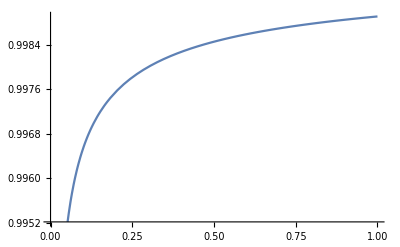

```mathematica
4*2/3
```

```mathematica
Expand[3^3]
```

27

```mathematica
rs[1,rh,0]
```

{{r==-(-1)^(1/4) rh},{r==(-1)^(1/4) rh},{r==-(-1)^(3/4) rh},{r==(-1)^(3/4) rh}}

```mathematica
(-1)
```

```mathematica
Clear[getc0h]
getc0h[μ_,rh_,d_,α_,Qh_,facD0h_]:= Module[{stepsize, c0hmin,c0hmax,delc0h,c0hholder, muholder,muholder2,muholder3,difmu,c0hindex,i,slnout,a,difmu3,sln,difmu2, rmax, mu25, mu50, mu75},
a=1;
(* c0h = 0 (AdS) c0h = 1 (Lifshitz) *)

mu25=  slngen[0.25, rh, d, α, Qh, facD0h][[5]];
If[mu25-μ>=0,c0hmin=0;c0hmax=mu25,mu50=  slngen[0.50, rh, d, α, Qh, facD0h][[5]]; If[mu50-μ>0, c0hmin=0.25;c0hmax = 0.50,mu75 =  slngen[0.75, rh, d, α, Qh, facD0h][[5]];If[mu75-μ>0, c0hmin=0.50; c0hmax=0.75,c0hmin=0.75; c0hmax=1]]];
(* Basically, I want to limit the range of μholder to 0.25. If μ25 = μ(c0h=0.25) > μ, then we need to lower the c0h (we need to go more towards AdS) and etc. *)
delc0h = N[c0hmax - c0hmin];
c0hindex = c0hmin;
muholder2 =10*μ;
difmu = μ-muholder2;
i=1;
While[Abs[difmu]>μ*10^(-4) && a<=2,
If[i<=40 && a<=2, sln = slngen[N[c0hindex+(0.500000)^(i)*delc0h,50], rh, d, α, Qh, facD0h]; muholder = sln[[5]];rmax = sln[[-1]]; difmu2 = μ-muholder; If[Abs[difmu2]<Abs[difmu],Print[{"A",i=i,rh,c0hindex = N[c0hindex+(0.500000)^(i)*delc0h,50],muholder2=muholder, difmu =difmu2}]; If[difmu<0,delc0h=delc0h*(-1), delc0h=delc0h] , Print[{"B",i=i,rh,c0hindex=c0hindex, muholder,difmu=difmu}]], If[c0hindex !=0,If[difmu<0 , delc0h = -(c0hindex-c0hindex/2); i=0;a=a+1,delc0h = (2*c0hindex-c0hindex); i=0;a=a+1],delc0h = c0hindex+(0.500000)^(40)*delc0h-c0hindex; a=a+1]];i=i+1];
slnout = slngen[c0hindex,rh,d,α,Qh,facD0h];
Flatten[{c0hindex, rh, d, α,slnout}]
]
```

```mathematica
getc0h[2,1,3,2,1,1]
```

$Aborted

```mathematica
Timing[getc0h[2,3,3,2,1,1]]
```

NDSolve::ndsz: At r == 3., step size is effectively zero; singularity or stiff system suspected.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification {}⟦1,1,2,0⟧[Domain]⟦1,2⟧ is longer than depth of object.

NDSolve::ndsz: At r == 3., step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve`ProcessSolutions::nodata: No solution data was computed between r == 3. and r == 3000..

Part::partd: Part specification {}⟦1,1,2,0⟧[Domain]⟦1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NDSolve`ProcessSolutions::nodata: No solution data was computed between r == 3. and r == 3000..

General::stop: Further output of NDSolve`ProcessSolutions::nodata will be suppressed during this calculation.

{B,5,3,0,514.578,-18}

{B,6,3,0,969.531,-18}

{B,7,3,0,1775.97,-18}

{B,8,3,0,3227.64,-18}

{B,9,3,0,6390.79,-18}

{B,10,3,0,20610.9,-18}

{B,11,3,0,41237.7,-18}

{B,12,3,0,2874.29,-18}

{B,13,3,0,619.011,-18}

{B,14,3,0,1159.,-18}

{B,15,3,0,798.132,-18}

{B,16,3,0,20.9241,-18}

{A,17,3,0.0128473,7.43465,-5.43465}

{A,18,3,0.00642365,2.66175,-0.66175}

{B,19,3,0.00642365,339.029,-0.66175}

{B,20,3,0.00642365,308.701,-0.66175}

{B,21,3,0.00642365,3.17081,-0.66175}

{B,22,3,0.00642365,2.90042,-0.66175}

{B,23,3,0.00642365,277.075,-0.66175}

{B,24,3,0.00642365,2.74147,-0.66175}

{B,25,3,0.00642365,274.005,-0.66175}

{B,26,3,0.00642365,2.68516,-0.66175}

{B,27,3,0.00642365,274.493,-0.66175}

{B,28,3,0.00642365,2.70654,-0.66175}

{B,29,3,0.00642365,2.68702,-0.66175}

{B,30,3,0.00642365,2.70072,-0.66175}

{B,31,3,0.00642365,2.6732,-0.66175}

{B,32,3,0.00642365,2.69259,-0.66175}

{B,33,3,0.00642365,2.66241,-0.66175}

{B,34,3,0.00642365,275.295,-0.66175}

{B,35,3,0.00642365,273.773,-0.66175}

{B,36,3,0.00642365,275.405,-0.66175}

{B,37,3,0.00642365,2.68433,-0.66175}

{A,38,3,0.00642365,2.65692,-0.65692}

{B,39,3,0.00642365,273.697,-0.65692}

{B,40,3,0.00642365,2.67051,-0.65692}

{A,1,3,0.00481774,1.78665,0.213354}

{B,2,3,0.00481774,1.37285,0.213354}

{B,3,3,0.00481774,226.478,0.213354}

{B,4,3,0.00481774,234.588,0.213354}

{B,5,3,0.00481774,1.70078,0.213354}

{B,6,3,0.00481774,1.73599,0.213354}

{B,7,3,0.00481774,1.7594,0.213354}

{B,8,3,0.00481774,1.77398,0.213354}

{B,9,3,0.00481774,239.832,0.213354}

{A,10,3,0.0048146,1.78837,0.211627}

{B,11,3,0.0048146,235.886,0.211627}

{B,12,3,0.0048146,239.634,0.211627}

{B,13,3,0.0048146,1.77974,0.211627}

{B,14,3,0.0048146,236.921,0.211627}

{B,15,3,0.0048146,239.763,0.211627}

{B,16,3,0.0048146,238.642,0.211627}

{B,17,3,0.0048146,236.94,0.211627}

{B,18,3,0.0048146,1.78618,0.211627}

{A,19,3,0.0048146,1.7939,0.206102}

{B,20,3,0.0048146,1.77931,0.206102}

{B,21,3,0.0048146,236.53,0.206102}

{B,22,3,0.0048146,1.78901,0.206102}

{B,23,3,0.0048146,237.015,0.206102}

{B,24,3,0.0048146,1.77926,0.206102}

{B,25,3,0.0048146,1.7679,0.206102}

{B,26,3,0.0048146,1.77816,0.206102}

{B,27,3,0.0048146,237.469,0.206102}

{B,28,3,0.0048146,1.754,0.206102}

{B,29,3,0.0048146,1.75634,0.206102}

{B,30,3,0.0048146,238.728,0.206102}

{A,31,3,0.0048146,1.79879,0.201212}

{B,32,3,0.0048146,238.168,0.201212}

{A,33,3,0.0048146,1.82065,0.179353}

{B,34,3,0.0048146,237.86,0.179353}

{B,35,3,0.0048146,235.661,0.179353}

{B,36,3,0.0048146,234.647,0.179353}

{B,37,3,0.0048146,1.7995,0.179353}

{B,38,3,0.0048146,1.78652,0.179353}

{B,39,3,0.0048146,1.81256,0.179353}

{B,40,3,0.0048146,1.7581,0.179353}

{250.965,{0.0048146,3,3,2,1.00217,1.,0.591178,9.52568,1.82065,0.952864,1.91071,1140.62}}

```mathematica
getc0h2[μ_,rh_,d_,α_,Qh_,facD0h_]:= Module[{stepsize, c0hmin,c0hmax,delc0h,c0hholder, muholder,muholder2,muholder3,difmu,c0hindex,i,slnout,a,difmu3,mu25,mu50,mu75},
a=1;
mu25=  slngen[0.25, rh, d, α, Qh, facD0h][[5]];
If[mu25-μ>=0,c0hmin=0;c0hmax=mu25,mu50=  slngen[0.50, rh, d, α, Qh, facD0h][[5]]; If[mu50-μ>0, c0hmin=0.25;c0hmax = 0.50,mu75 =  slngen[0.75, rh, d, α, Qh, facD0h][[5]];If[mu75-μ>0, c0hmin=0.50; c0hmax=0.75,c0hmin=0.75; c0hmax=1]]];

c0hmin=0.0016715167297430683;
delc0h = N[c0hmax - c0hmin];
c0hindex = c0hmin;
muholder2 =12*μ;
difmu = μ-muholder2;
muholder3=-1;
difmu3=μ-muholder3;
i=1;
While[Abs[difmu]>μ*10^(-4) && a<=2,
If[i<=40 && a<=2,
muholder = slngen[N[c0hindex+a*(0.500000)^(i)*delc0h,50], rh, d, α, Qh, facD0h][[5]];
If[Sign[muholder-μ]==-1 && If[muholder3<μ, muholder>=muholder3, True] (* make sure that the new diffmu is always smaller than the previous one *), Print[{"A"(* Change the value of μ *),i=i,rh,c0hindex = N[c0hindex+(0.500000)^(i)*delc0h,10],muholder2=muholder, difmu = Abs[μ-muholder2]}]; difmu3=μ-muholder;muholder3=N[muholder2,50],Print[{"B"(* Does not change the value of μ, but next iteration will give a smaller value of c0h *),i=i,rh,c0hindex=c0hindex, muholder,difmu=difmu}];difmu3=μ-muholder],(* If i > 100 ie no convergence --> *)If[c0hindex != 0  (* sometimes your operation always produce the B print for all i. If this is the case, quit the while loop *),If[Sign[difmu3]==-1  (* if diffmu3 < 0, so muholder that you have is LARGER than μ you need, then you need a SMALLER muholder, so you've got to go more towards AdS c0hindex = 0 *),delc0h=Abs[5*c0hindex-c0hindex]; c0hindex=c0hindex-c0hindex/5;a=a+1; i=1 ,(* if diffmu3 > 0, so muholder that you have is SMALLER than μ you need, then you need a LARGER muholder, so you've got to go more towards Lifshitz c0hindex = 1 *)delc0h=Abs[c0hmax-c0hindex];c0hindex=c0hindex;a=a+1;i=1],(* if c0hindex = 0... sometimes your operation always produce the B print for all i in this case quit the while loop*)delc0h = c0hindex+(0.500000)^(40)*delc0h-c0hindex; a=a+1]];i=i+1];
slnout = slngen[c0hindex,rh,d,α,Qh,facD0h];
Flatten[{c0hindex, rh, d, α,slnout}]
]


getc0hmuT[μT_,rh_,d_,α_,Qh_,facD0h_]:= Module[{stepsize, c0hmin,c0hmax,delc0h,c0hholder,difmuT,difmuT3,muTholder ,muTholder2,muTholder3,c0hindex,i,slnout,a},
a=1;
c0hmin  =0;(* AdS *)
c0hmax =1; (* Lifshitz *)
delc0h = N[c0hmax - c0hmin];
c0hindex = c0hmin;
muTholder2 =10*μT;
difmuT = μT-muTholder2;
muTholder3=-1;
difmuT3= μT-muTholder3;
i=9;
While[Abs[difmuT]>μT*10^(-4) && a<= 3 (* Restrict the maximum of re-iteration from i = 1 ... 50 to 2 *),
If[i<=40,
muTholder = slngen[N[c0hindex+(0.500000)^(i)*delc0h,50], rh, d, α, Qh, facD0h][[7]];
If[Sign[muTholder-μT]==-1 && If[Abs[muTholder-μT]<difmuT, True](* make sure that the new diffmu is always smaller than the previous one *), Print[{"A"(* Change the value of μ *),i=i,rh,c0hindex = N[c0hindex+a*(0.500000)^(i)*delc0h,50],muTholder2=muTholder, difmuT = Abs[μT-muTholder2]}];muTholder3=N[muTholder2,50]; difmuT3=μT-muTholder,Print[{"B" (* Does not change the value of μ, but next iteration will give a smaller value of c0h *),i=i,rh,c0hindex=c0hindex, muTholder,difmuT=difmuT}];difmuT3=μT-muTholder],(* If i > 100 ie no convergence --> *)If[c0hindex != 0  (* sometimes your operation always produce the B print for all i. If this is the case, quit the while loop *),If[Sign[difmuT3]==-1  (* if diffmuT3 < 0, so muholder that you have is LARGER than μT you need, then you need a SMALLER muTholder, so you've got to go more towards AdS c0hindex = 0 *),delc0h=-Abs[c0hindex-c0hindex/2]; c0hindex=c0hindex;a=a+1; i=0 ,(* if diffmuT3 > 0, so muholder that you have is SMALLER than μT you need, then you need a LARGER muTholder, so you've got to go more towards Lifshitz c0hindex = 1 *)delc0h=Abs[3*c0hindex-c0hindex];c0hindex=c0hindex;a=a+1;i=0],(* if c0hindex = 0... sometimes your operation always produce the B print for all i in this case quit the while loop*)Abs[difmuT] =1/100* μT*10^(-4)]];i=i+1];
slnout = slngen[c0hindex,rh,d,α,Qh,facD0h];
Flatten[{c0hindex, rh, d, α,slnout}]
]
```

```mathematica
Timing[getc0h2[2,3,3,2,1,1]]
```

NDSolve::ndsz: At r == 3., step size is effectively zero; singularity or stiff system suspected.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification {}⟦1,1,2,0⟧[Domain]⟦1,2⟧ is longer than depth of object.

NDSolve::ndsz: At r == 3., step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve`ProcessSolutions::nodata: No solution data was computed between r == 3. and r == 3000..

Part::partd: Part specification {}⟦1,1,2,0⟧[Domain]⟦1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NDSolve`ProcessSolutions::nodata: No solution data was computed between r == 3. and r == 3000..

General::stop: Further output of NDSolve`ProcessSolutions::nodata will be suppressed during this calculation.

{B,5,3,0.00167152,514.561,-22}

{B,6,3,0.00167152,969.477,-22}

{B,7,3,0.00167152,1775.78,-22}

{B,8,3,0.00167152,3226.92,-22}

{B,9,3,0.00167152,6387.05,-22}

{B,10,3,0.00167152,20554.2,-22}

{B,11,3,0.00167152,41856.4,-22}

{B,12,3,0.00167152,2886.62,-22}

{B,13,3,0.00167152,1576.89,-22}

{B,14,3,0.00167152,1173.58,-22}

{B,15,3,0.00167152,819.531,-22}

{B,16,3,0.00167152,581.596,-22}

{B,17,3,0.00167152,416.141,-22}

{B,18,3,0.00167152,312.192,-22}

{B,19,3,0.00167152,238.498,-22}

{B,20,3,0.00167152,195.274,-22}

{B,21,3,0.00167152,171.396,-22}

{B,22,3,0.00167152,157.611,-22}

{A,23,3,0.00187226,0.495819,1.50418}

{B,24,3,0.00187226,150.478,1.50418}

{B,25,3,0.00187226,149.366,1.50418}

{B,26,3,0.00187226,148.849,1.50418}

{B,27,3,0.00187226,147.251,1.50418}

{A,28,3,0.00187853,0.497682,1.50232}

$Aborted

```mathematica
Clear[slngenAsypm,slnhold2]
slnhold2[c0h_, rh_, d_,α_]:= Module[{E1,E2,E3,E4,E41,eAseed,eCseed,eGseed,IePhseed,ePhiseed,c0,D0h, a0, a1, c1,g0, g1,rIni,eOm,bc,eq,rmax,a,sol,e2aPhi, Qhlocal,Bc1 ,facD0h, sln1, BCval},
Bc1 = slngen[c0h, rh, d, α, 1,1];
facD0h = 1/Bc1 [[1]];
Qhlocal = Sqrt[Bc1 [[4]]];
BCval = slngen[c0h, rh, d, α, Qhlocal ,facD0h];
sln1=slnhold[c0h, rh, d, α, Qhlocal ,facD0h];
{BCval,sln1, facD0h, Qhlocal}]

HEE[data_,d_,α_]:= Module[{datasize,slnlist,sln,BCval, sln1, facD0h1, Qhlocal,L,SolList ,HEEList,i,j, rH,AsolNear,CsolNear,Bsol,Aads,Cads,Bads,z,aL,Llif,Alif,Clif,Blif,r,k,Lslab,Sa, SaAds,SaLif,rmax,LslabLif,LslabAdS},
L = 1;
datasize = Length[data];
slnlist = {};
For[i=1, i<= Length[data], i++, sln =  slnhold2[data[[i]][[1]],data[[i]][[2]] ,data[[i]][[3]],data[[i]][[4]]];AppendTo[slnlist, sln]];
slnlist
(* 
SolList = {};
For[j = 1, j<= Length[slnlist], j++, rH=data[[j]][[1]];rmax=slnlist[[j]][[1]][[-1]];facD0h1=slnlist[[j]][[3]]; AsolNear[r_]:=slnlist[[j]][[2]][[1]][r]^2*(L*r)^2; CsolNear[r_]:=slnlist[[j]][[2]][[2]][r]^2*(L*r)^2;Aads[r_, rh_]:= (L*r*Sqrt[1-(rh/r)^(d+1)])^2;
Cads[r_, rh_]:= (L/(r*Sqrt[1-(rh/r)^(d+1)]))^2;
Bads[r_]:= (L*r)^2;
z=2*d/(α^2)+1;
Llif = L*Sqrt[((z[d]+d)*(z[d]+d-1))/(d*(d+1))];
aL[rh_,facD0h_]:=Sqrt[2]*(1/2*rh^(d+1)*(d+1)*d*α*facD0h)/(rh^(d+z)*α*d*(d+z));
Alif[r_, rh_,facD0h_]:= (Llif*aL[rh,facD0h]*r^(z[d])*Sqrt[1-(rh/r)^(d+z)])^2;
Clif[r_,rh_]:=(Llif/(r*Sqrt[1-(rh/r)^(d+z)]))^2;
Blif[r_]:= (L*r)^2;
AppendTo[SolList,{
Lslab[rs_]:=Re[-2*NIntegrate[Sqrt[CsolNear[r]/Bsol[r]]*1/(Sqrt[(Bsol[r]/Bsol[rs])^d-1]), {r,1000, rs}]],
Sa[rs_]:= Re[-NIntegrate[Bsol[r]^((d+2)/2)*Sqrt[CsolNear[r]]/(Sqrt[Bsol[r]^d-Bsol[rs]^d]), {r, 1000, rs}]],
SaAds[rs_,rh_]:=Re[-NIntegrate[Bads[r]^((d+2)/2)*Sqrt[Cads[r,rh]]/(Sqrt[Bads[r]^d-Bads[rs]^d]), {r, 1000, rs}]],SaLif[rs_,rh_]:=Re[-NIntegrate[Blif[r]^((d+2)/2)*Sqrt[Clif[r,rh]]/(Sqrt[Blif[r]^d-Blif[rs]^d]), {r, 1000, rs}]],
LslabAdS[rs_,rh_]:=Re[-2*NIntegrate[Sqrt[Cads[r,rh]/Bads[r]]*1/(Sqrt[(Bads[r]/Bads[rs])^d-1]), {r,1000, rs}]],
LslabLif[rs_,rh_]:=Re[-2*NIntegrate[Sqrt[Clif[r,rh]/Blif[r]]*1/(Sqrt[(Blif[r]/Blif[rs])^d-1]), {r,1000, rs}]]}]
]
SolList
*)
]
```

# r’’(x) and r(x) analysis at rt = 5.1 rH

## Solving for r(x) directly given the EoM

```mathematica
Clear[x,d, B,c]
Needs["VariationalMethods`"]
EulerEquations[E^(d*B[r[x]])*Sqrt[1+E^(2*c[r[x]]-2*B[r[x]])*r'[x]^2], r[x], x]
```

(ⅇ^(d B[r[x]]) (B'[r[x]] (d ⅇ^(2 B[r[x]])+(1+d) ⅇ^(2 c[r[x]]) r'[x]^2)-ⅇ^(2 c[r[x]]) (c'[r[x]] r'[x]^2+r''[x])))/((ⅇ^(2 B[r[x]])+ⅇ^(2 c[r[x]]) r'[x]^2) √(1+ⅇ^(-2 B[r[x]]+2 c[r[x]]) r'[x]^2))==0

```mathematica
Clear[d]
Expand[ⅇ^(d B[r[x]]) (B'[r[x]] (d ⅇ^(2 B[r[x]])+(1+d) ⅇ^(2 c[r[x]]) r'[x]^2)-ⅇ^(2 c[r[x]]) (c'[r[x]] r'[x]^2+r''[x]))]
```

d ⅇ^(2 B[r[x]]+d B[r[x]]) B'[r[x]]+ⅇ^(d B[r[x]]+2 c[r[x]]) B'[r[x]] r'[x]^2+d ⅇ^(d B[r[x]]+2 c[r[x]]) B'[r[x]] r'[x]^2-ⅇ^(d B[r[x]]+2 c[r[x]]) c'[r[x]] r'[x]^2-ⅇ^(d B[r[x]]+2 c[r[x]]) r''[x]

```mathematica
Solve[d ⅇ^(2 B[r[x]]+d B[r[x]]) B'[r[x]]+ⅇ^(d B[r[x]]+2 c[r[x]]) B'[r[x]] r'[x]^2+d ⅇ^(d B[r[x]]+2 c[r[x]]) B'[r[x]] r'[x]^2-ⅇ^(d B[r[x]]+2 c[r[x]]) c'[r[x]] r'[x]^2-ⅇ^(d B[r[x]]+2 c[r[x]]) r''[x]==0, r''[x]]
```

{{r''[x]→ⅇ^(-2 c[r[x]]) (d ⅇ^(2 B[r[x]]) B'[r[x]]+ⅇ^(2 c[r[x]]) B'[r[x]] r'[x]^2+d ⅇ^(2 c[r[x]]) B'[r[x]] r'[x]^2-ⅇ^(2 c[r[x]]) c'[r[x]] r'[x]^2)}}

```mathematica
r''[x]==ⅇ^(-2 c[r[x]]) (d ⅇ^(2 B[r[x]]) B'[r[x]]+ⅇ^(2 c[r[x]]) B'[r[x]] r'[x]^2+d ⅇ^(2 c[r[x]]) B'[r[x]] r'[x]^2-ⅇ^(2 c[r[x]]) c'[r[x]] r'[x]^2)
```

r''[x]==ⅇ^(-2 c[r[x]]) (d ⅇ^(2 B[r[x]]) B'[r[x]]+ⅇ^(2 c[r[x]]) B'[r[x]] r'[x]^2+d ⅇ^(2 c[r[x]]) B'[r[x]] r'[x]^2-ⅇ^(2 c[r[x]]) c'[r[x]] r'[x]^2)

```mathematica
Clear[r,x,d]
d=3;
c[r_]:= 1/2*Log[(sln[[2]][r])^2*(L/r)^2]
B[r_]:=Log[L*r]
r''[x]== (d ⅇ^(2 B[r[x]])ⅇ^(-2 c[r[x]])  B'[r[x]]+ⅇ^(2 c[r[x]]) B'[r[x]] r'[x]^2+d  B'[r[x]] r'[x]^2- 1/(2*E^(2*c[r[x]]))D[E^(2*c[r[x]]),r] r'[x]^2)
xmin =-0.5;
xmax = 0.5;
NDSolve[{r''[x]== (d ⅇ^(2 B[r[x]])ⅇ^(-2 c[r[x]])  B'[r[x]]+ⅇ^(2 c[r[x]]) B'[r[x]] r'[x]^2+d  B'[r[x]] r'[x]^2- 1/(2*E^(2*c[r[x]]))D[E^(2*c[r[x]]),r] r'[x]^2),r[xmin]==1000, r'[0]==0}, r[x],{x, xmin, xmax}]
```

r''[x]==(3 r[x]^3)/(InterpolatingFunction[{{1., 1000.}}, <>][r[x]])^2+(3 r'[x]^2)/r[x]+((InterpolatingFunction[{{1., 1000.}}, <>][r[x]])^2 r'[x]^2)/r[x]^3

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

Power::infy: Infinite expression 1/0.^3 encountered.

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.^2 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at x == -0.5.

NDSolve[{r''[x]==(3 r[x]^3)/(InterpolatingFunction[{{1., 1000.}}, <>][r[x]])^2+(3 r'[x]^2)/r[x]+((InterpolatingFunction[{{1., 1000.}}, <>][r[x]])^2 r'[x]^2)/r[x]^3,r[-0.5]==1000,r'[0]==0},r[x],{x,-0.5,0.5}]

## Cross-section of the surface and r = r0 - ϵ ξ analysis (approaching the discontinuity)

```mathematica
(* According to a paper *)
x[z_,n_]:=z^(n+1)/((n+1)*zmax^n)*Hypergeometric2F1[1/2, (n+1)/(2*n), (3*n+1)/(2*n),(z/zmax)^(2*n)]-zmax*Sqrt[Pi]*Gamma[(3*n+1)/(2*n)]/((n+1)*Gamma[(2*n+1)/(2*n)])

(* r=r0-ϵ ξ *)

Clear[zmax]
Normal[Series[-ϵ*(zmax^(n+1)*(1-ϵ*ξ)^(2*n)/Sqrt[1-(1-ϵ*ξ)^(2*n)]),{ϵ,0,2}]]; (* second order in ϵ -> xApp *)
Integrate[-(zmax^(1+n) √ϵ)/(√2 √(n ξ))+((1+6 n) zmax^(1+n) ϵ^(3/2) ξ)/(4 √2 √(n ξ)),{ξ, 0, (1-z/zmax)/ϵ}]; (* --> gves xApp *)

xApp[z_,n_]=-(zmax^n (z+6 n z+(11-6 n) zmax) √((n (-z+zmax))/zmax))/(6 √2 n)
Clear[zmax]
Normal[Series[-ϵ*(zmax^(n+1)*(1-ϵ*ξ)^(2*n)/Sqrt[1-(1-ϵ*ξ)^(2*n)]),{ϵ,0,3}]]; (* third order in ϵ -> xApp2 *)
Integrate[-(zmax^(1+n) √ϵ)/(√2 √(n ξ))+((1+6 n) zmax^(1+n) ϵ^(3/2) ξ)/(4 √2 √(n ξ))-((-7-36 n+100 n^2) zmax^(1+n) ϵ^(5/2) ξ^2)/(96 √2 √(n ξ)),{ξ, 0, (1-z/zmax)/ϵ}]; (* --> gves xApp2 *)
xApp2[z_,n_]:=-1/(240 √2 n)zmax^(-1+n) ((-1+2 n) (7+50 n) z^2+2 (27+4 (39-25 n) n) z zmax+(433+4 n (-69+25 n)) zmax^2) √((n (-z+zmax))/zmax)
```

```mathematica
zmax= 3;
```

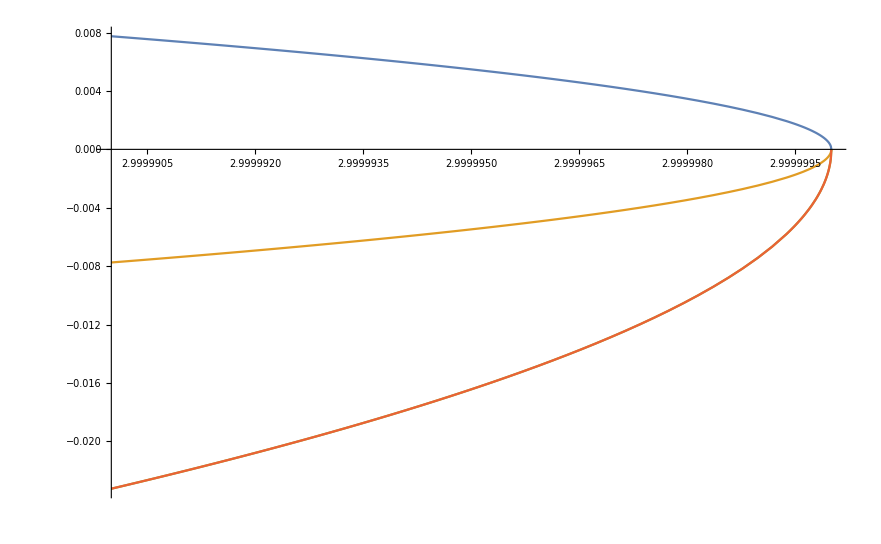

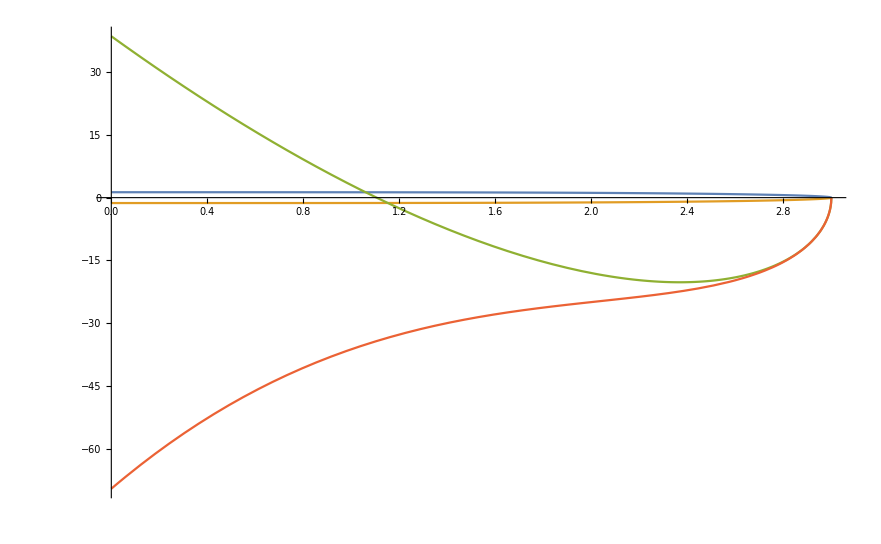

```mathematica
Plot[{-x[z,1],x[z,1], xApp[z,1],xApp2[z,1]},{z,zmax-0.00001,zmax}]
Plot[{-x[z,3],x[z,3],xApp[z,3],xApp2[z,3]},{z,0,zmax}]
```

## Computation of the cross-section for our particular solution

```mathematica
Clear[x,r, rmax]
c[r_]:= 1/2*Log[(sln[[2]][r])^2*(L/r)^2]
B[r_]:=Log[L*r]
rmax = 5.5*1;
d = 3;
x[u_]:= NIntegrate[E^(c[r]-B[r])/Sqrt[E^(2*d*(B[r]-B[rmax]))-1],{r, rmax, u}]
```

NIntegrate::zeroregion: Integration region {{5.5,5.5000000000000000000024174180637002060661213516612770283963753057}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::inumri: The integrand Divide[Power[Divide[Power[InterpolatingFunction[{{1., 1000.}}, <>][r], 2], Power[r, 2]], <<1>>], Power[-1 + Power[E, 6 <<1>>], <<1>>] r] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{5.5000000000000000000024174180637002060661213516612770283963753057,5.5000000000000001037113378536572954789256723010425136218302116938}}.

NIntegrate::zeroregion: Integration region {{5.5,5.5000000000000000000024174180637002060661213516612770283963753057}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::inumri: The integrand Divide[Power[Divide[Power[InterpolatingFunction[{{1., 1000.}}, <>][r], 2], Power[r, 2]], 0.5], Power[-1. + Power[<<6>>8, <<1>>], <<1>>] <<1>>] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{5.5000000000000000000024174180637002060661213516612770283963753057,5.5000000000000001037113378536572954789256723010425136218302116938}}.

NIntegrate::zeroregion: Integration region {{5.5,5.5000000000000000000024174180637002060661213516612770283963753057}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

General::stop: Further output of NIntegrate::zeroregion will be suppressed during this calculation.

NIntegrate::inumri: The integrand Divide[Power[Divide[Power[InterpolatingFunction[{{1., 1000.}}, <>][r], 2], Power[r, 2]], 0.5], Power[-1. + Power[<<6>>8, <<1>>], <<1>>] <<1>>] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{5.5000000000000000000024174180637002060661213516612770283963753057,5.5000000000000001037113378536572954789256723010425136218302116938}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

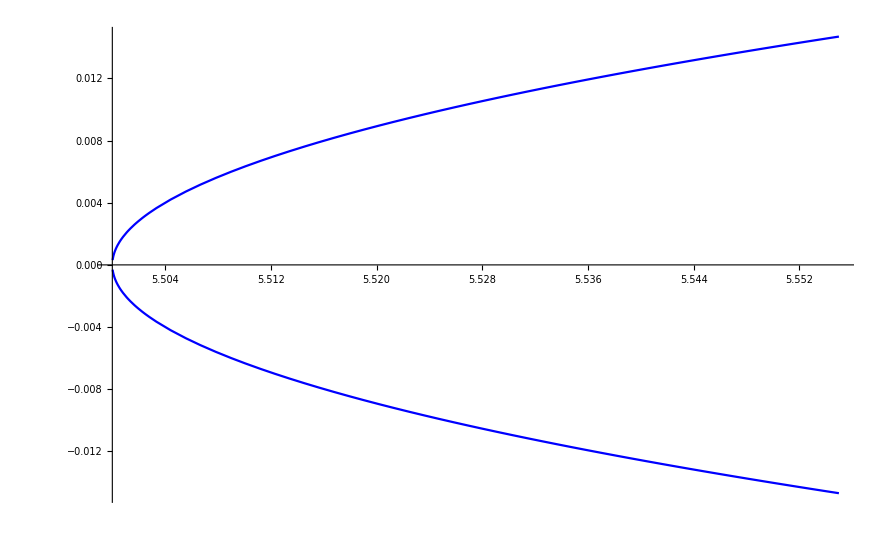

```mathematica
Plot[{-x[u],x[u]},{u,rmax, rmax*1.01}, PlotStyle->{Blue, Blue}]
```

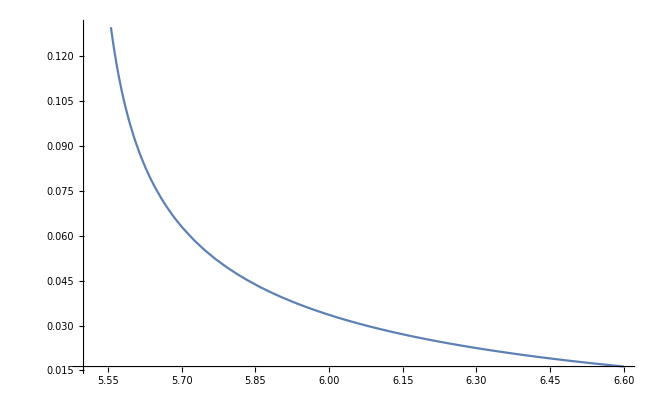

```mathematica
Plot[E^(c[r]-B[r])/Sqrt[E^(2*d*(B[r]-B[rmax]))-1], {r,rmax, rmax*1.2}]
```

## Trying to analyze the cutoff limit...

```mathematica
(* u = 1 -> Horizon, u = 0 -> BC *)

zh = 1;(* zh = 1/rh *)
α = 2;
facD0h = 1/1.131992381219958;
c0h = 0.2511886431509580111085032067799327394149;
Clear[c0,c1,Cnew,CAdS,z,Llif,CLif,pCAds,pCLif,LslabNew,LslabNewU,Sanew,SanewAdS,SanewLif,pSAdsnew]
c0[d_]:=(c0h*((Sqrt[α^2+2]-α)/(α))*Sqrt[(1/zh)]+Sqrt[(1/zh)])/(Sqrt[d+1]);
c1[d_]:=c0[d]*(3*α^2*d*(d+1)^2*c0[d]^4-2*d*(1/zh)*(3*α^2+2)*(d+1)*c0[d]^2+3*(1/zh)^2*α^2*d+4*(1/zh)^2+6*d*(1/zh)^2)/(8*(1/zh)^3)

Cnew[u_,d_]:=(c0[d]*zh^(1/2)*u^(1/2)/(1-u)^(1/2)+c1[d]/(zh*u)^(1/2)*(1-u)^(1/2))^2
CAdS[u_,zhAdS_,d_]:= 1/(1-(u*zh/zhAdS)^(d+1))

z[d_]:=2*d/(α^2)+1;
Llif[d_]:= L*Sqrt[((z[d]+d)*(z[d]+d-1))/(d*(d+1))]
CLif[u_,zhLif_,d_]:= (Llif[d]/L)^2/(1-(u*zh/zhLif)^(d+z[d]))

pCAds[u_,d_]:= (u*zh)^2*L^2
pCLif[u_,d_]:= (u*zh)^2*L^2

Clear[rs, Lslab, Sa, r,u,u]
$Assumptions =rs >0;
$Assumptions =rs ∈ Reals;

LslabNew[us_,d_]:=NIntegrate[Sqrt[Cnew[u,d]]*u^2*(zh^3/L^2)/(Sqrt[(us/u)^(2*d)-1]),{u,us,0}]
LslabNewU[us_,d_, u_]:=NIntegrate[Sqrt[Cnew[u,d]]*u^2*(zh^3/L^2)/(Sqrt[(us/u)^(2*d)-1]),{u,us,u}]


Sanew[us_, d_]:= NIntegrate[L^2/zh*Sqrt[Cnew[u,d]]*1/u^2*1/Sqrt[1-(u/us)^(2*d)],{u, 0, us}]
SanewAdS[us_,zhAdS_, d_]:= NIntegrate[L^2/zh*Sqrt[CAdS[u,zhAdS,d]]*1/(u*zh/zhAdS)^2*1/Sqrt[1-((u*zh/zhAdS)/us)^(2*d)],{u, 0, us}]
SanewLif[us_,zhLif_, d_]:= NIntegrate[L^2/zh*Sqrt[CLif[u,zhLif,d]]*1/(u*zh/zhLif)^2*1/Sqrt[1-((u*zh/zhLif)/us)^(2*d)],{u, 0, us}]

pSAdsnew[us_,d_]:= NIntegrate[L^2/zh*Sqrt[pCAds[u,d]]*1/(u*zh)^2*1/Sqrt[1-((u*zh)/us)^(2*d)],{u, 0, us}]
(*

Lslab[rs_,d_]:=Re[-2*NIntegrate[Sqrt[CsolNear[1/r]/Bsol[1/r]]*1/(Sqrt[(Bsol[1/r]/Bsol[1/rs])^d-1]), {r,1/10000, rs}]]
Sa[rs_,d_]:= Re[-NIntegrate[Bsol[1/r]^((d+2)/2)*Sqrt[CsolNear[1/r]]/(Sqrt[Bsol[1/r]^d-Bsol[1/rs]^d]), {r, 1/10000, rs}]]
$Assumptions=True;
SaAds[rs_,rh_,d_]:=Re[-NIntegrate[Bads[1/r]^((d+2)/2)*Sqrt[Cads[1/r,rh,d]]/(Sqrt[Bads[1/r]^d-Bads[1/rs]^d]), {r, 1/10000, rs}]]
LslabAdS[rs_,rh_,d_]:=Re[-2*NIntegrate[Sqrt[Cads[1/r,rh,d]/Bads[1/r]]*1/(Sqrt[(Bads[1/r]/Bads[1/rs])^d-1]), {r,1/10000, rs}]]

SaLif[rs_,rh_,d_]:=Re[-NIntegrate[Blif[1/r]^((d+2)/2)*Sqrt[Clif[1/r,rh,d]]/(Sqrt[Blif[1/r]^d-Blif[1/rs]^d]), {r,1/ 10000,rs}]]
LslabLif[rs_,rh_,d_]:=Re[-2*NIntegrate[Sqrt[Clif[1/r,1/rh,d]/Blif[1/r]]*1/(Sqrt[(Blif[1/r]/Blif[1/rs])^d-1]), {r,1/10000, rs}]]


pSaAds[rs_,d_]:=Re[-NIntegrate[pBads[1/r]^((d+2)/2)*Sqrt[pCads[1/r]]/(Sqrt[pBads[1/r]^d-pBads[1/rs]^d]), {r, 1/10000, rs}]]

pSalif[rs_,d_]:=Re[-NIntegrate[pBlif[1/r,d]^((d+2)/2)*Sqrt[pClif[1/r,d]]/(Sqrt[pBlif[1/r,d]^d-pBlif[1/rs,d]^d]), {r,1/10000, rs}]]
*)
```

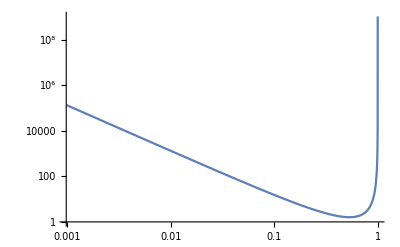

```mathematica
LogLogPlot[Cnew[u,3]^2,{u, 1,0}]
```

```mathematica
(* Solution for the AdS and Lifshitz Black Brane *)

L = 1;
rMax = BCval[[-1]];
Asolbc = N[BCval[[1]], 50];
Csolbc = N[BCval[[2]], 50];
Clear[Asol, Csol,Bsol,AsolAsymp,CsolAsymp,AsolNear,CsolNear]

AsolAsymp[r_]:=Asolbc*(L*r)^2 (* r > 1000 *)
CsolAsymp[r_]:=Csolbc*(L/r)^2 (* r > 1000 *)
AsolNear[r_]:=sln[[1]][r]^2*(L*r)^2
CsolNear[r_]:= sln[[2]][r]^2*(L/r)^2
Bsol[r_]:= (L*r)^2

Clear[Aads,Cads,Bads,z]

Aads[r_, rh_, d_]:= (L*r*Sqrt[1-(rh/r)^(d+1)])^2
Cads[r_, rh_, d_]:= (L/(r*Sqrt[1-(rh/r)^(d+1)]))^2
Bads[r_]:= (L*r)^2



(* PURE ADS *)
Clear[pAads, pCads,pBads]
(* We make a transformation L -> 1/L in the 2.128 of Ammon Erdminger *)
pAads[r_]:= (L*r)^2
pBads[r_]:= (L*r)^2
pCads[r_]:= L/(r)^2


Clear[Alif, Clif, Blif,z,aL,Llif, α,z,facD0h]
α = 2;
facD0h = 1/1.131992381219958;
z[d_]:=2*d/(α^2)+1;

aL[rh_,d_]:= 
Sqrt[2]*(1/2*rh^(d+1)*(d+1)*d*α*facD0h)/(rh^(d+z[d])*α*d*(d+z[d]))
Llif[d_]:= L*Sqrt[((z[d]+d)*(z[d]+d-1))/(d*(d+1))]
Alif[r_, rh_, d_]:= (Llif[d]*aL[rh,d]*r^(z[d])*Sqrt[1-(rh/r)^(d+z[d])])^2
Clif[r_,rh_,d_]:=(Llif[d]/(r*Sqrt[1-(rh/r)^(d+z[d])]))^2
Blif[r_]:= (L*r)^2

(* Pure Lifshitz *)
pBlif[r_,d_]:= (L*r)^2
pAlif[r_,d_]:= (Llif[d])^2(r)^z[d]
pClif[r_, d_]:= (Llif[d]/r)^2
```

Part::partd: Part specification BCval⟦-1⟧ is longer than depth of object.

Part::partd: Part specification BCval⟦1⟧ is longer than depth of object.

Part::partd: Part specification BCval⟦2⟧ is longer than depth of object.

```mathematica
Clear[B,c, d,r, L,z, Llif]
$Assumptions=True;
$Assumptions = d >0; $Assumptions = z >=1;

Simplify[B[r]^((d+2)/2)*Sqrt[c[r]]/Sqrt[B[r]^d-B[rs]^d]/.c[r]->(Llif/(r*Sqrt[1-(rh/r)^(d+z)]))^2/.B[r]->(L*r)^2/.B[rs]->(L*rs)^2]
```

((L^2 r^2)^((2+d)/2) √(-Llif^2/(r^2 (-1+(rh/r)^(d+z)))))/(√((L^2 r^2)^d-(L^2 rs^2)^d))

```mathematica
Integrate[(u α)^(d+z)/(2 u √(1-u^(2 d))), {u,ϵ,1}]
```

ConditionalExpression[0, Re[d]≥0&&Im[d]==0&&Re[ϵ]>0&&Im[ϵ]==0&&ϵ^(2 d)>1&&Abs[ϵ]≤1]

```mathematica
1/2 (-(2 ArcTanh[√(1-u^(2 d))])/d+((u α)^(d+z) Hypergeometric2F1[1/2,(d+z)/(2 d),(3 d+z)/(2 d),u^(2 d)])/(d+z))/.u->1
-1/2 (-(2 ArcTanh[√(1-u^(2 d))])/d+((u α)^(d+z) Hypergeometric2F1[1/2,(d+z)/(2 d),(3 d+z)/(2 d),u^(2 d)])/(d+z))/.u->ϵ
```

(√π α^(d+z) Gamma[3/2+z/(2 d)])/(2 (d+z) Gamma[1+z/(2 d)])

1/2 ((2 ArcTanh[√(1-ϵ^(2 d))])/d-((α ϵ)^(d+z) Hypergeometric2F1[1/2,(d+z)/(2 d),(3 d+z)/(2 d),ϵ^(2 d)])/(d+z))

```mathematica
$Assumptions = x >0;
Series[ArcTanh[√(1-ϵ^(2 d))]/.ϵ^(2*d)->x,{x,0,0}]
Series[Hypergeometric2F1[1/2,(d+z)/(2 d),(3 d+z)/(2 d),ϵ^(2 d)]/.ϵ^(2*d)->x,{x,0,0}]
```

1/2 (2 Log[2]-Log[x])+O[x]^1

1+O[x]^1

```mathematica
Integrate[(z^(2-2*d)/z^(1-d))/Sqrt[1-zt^(2-2*d)/z^(2-2*d)]/.d->4, {z,ϵ,zt}]
Integrate[(z^(2-2*d)/z^(1-d))/Sqrt[1-zt^(2-2*d)/z^(2-2*d)]/.d->3, {z,ϵ,zt}]
$Assumptions = d >0;
Integrate[(z^(2-2*d)/z^(1-d))/Sqrt[1-zt^(2-2*d)/z^(2-2*d)], z]
```

ConditionalExpression[1/6 ((√π Gamma[-1/3])/(zt^2 Gamma[1/6])+(3 Hypergeometric2F1[-1/3,1/2,2/3,ϵ^6/zt^6])/ϵ^2), ϵ>0&&Re[zt]>ϵ&&zt==Re[zt]]

ConditionalExpression[-(√π Gamma[3/4])/(zt Gamma[1/4])+Hypergeometric2F1[-1/4,1/2,3/4,ϵ^4/zt^4]/ϵ, ϵ>0&&Re[zt]>ϵ&&zt==Re[zt]]

```mathematica
z[3]+3
```

11/2

1

{{rh1→-0.883973},{rh1→0.883973}}

{{rh1→-1.41421},{rh1→1.41421}}

1

{{rh1→-0.883973},{rh1→0.883973}}

{{rh1→-1.41421},{rh1→1.41421}}

{1.,1.,0.419161,0.999962,0.419169,0.281377,1.4897,1000.}

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

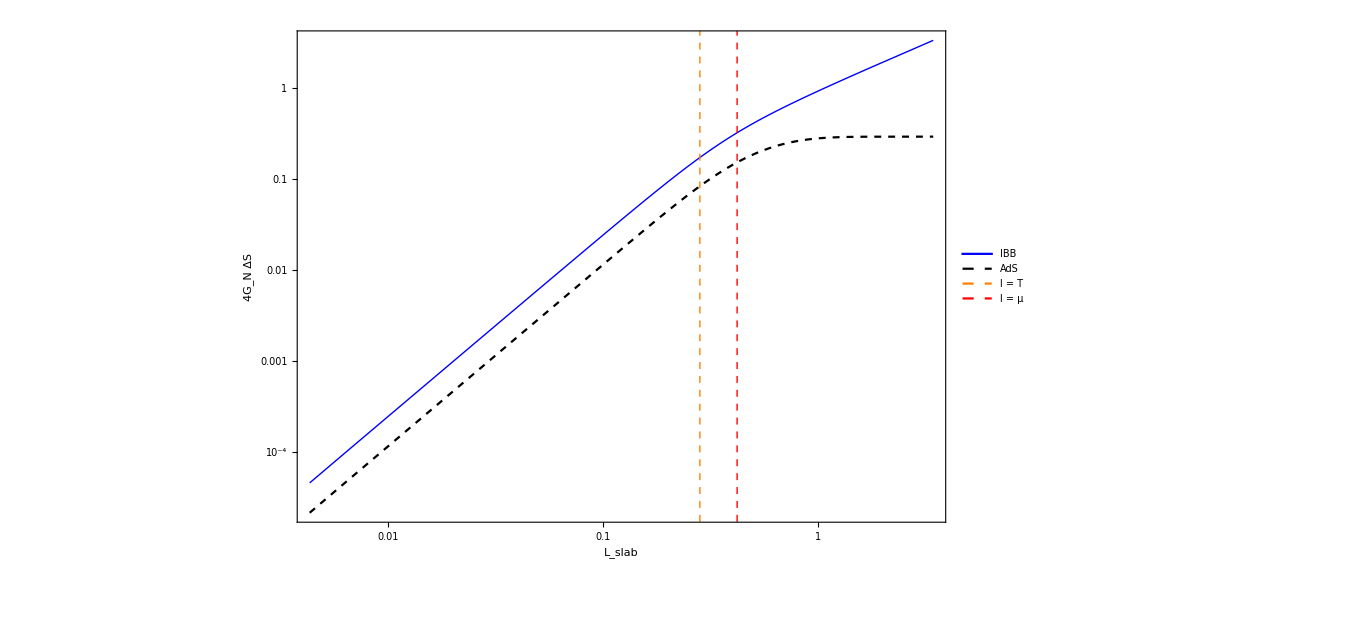

```mathematica
(* d = 3; α = 3; rh = 1; c0 = 0.25; L=1; *)
{{0.041725520394487,0.18066444386627242},{0.041876459925855494,0.18125510539005316},{0.0420273999043141,0.18200419941235024},{0.04217834024433337,0.18261227333821425},{0.04232928103169636,0.18326419802913838},{0.04248022211915169,0.18391444706451526},{0.04263116341492103,0.18456643004752404},{0.04278210525464406,0.18521699232271374},{0.04293304764562711,0.18587056732704155},{0.04308399034135228,0.18652184669735333},{0.043234933263172674,0.18717221766153985},{0.04338587658184628,0.1878212114509987},{0.043536820310269564,0.18847473056086003},{0.043687764441910845,0.18912011227296563},{0.04383870906419546,0.1897745925794636},{0.0439896541786355,0.1904249133990618},{0.044140599712162734,0.19107865730965667},{0.044291545512779515,0.19173248785957783},{0.0444424919031368,0.19237922211399136},{0.04459343863828147,0.19302495842202283},{0.04474438581030881,0.19367992713552779},{0.044895333500907145,0.19432968664562944},{0.04504628155992415,0.19498300987400388},{0.04519722998774266,0.19563291751334883},{0.045348178860229446,0.1962802691884192},{0.04549912828007363,0.19693958176939708},{0.04565007808059238,0.19758484872766247},{0.04580102860114568,0.19823962462049932},{0.045951979505454814,0.19889254269000425},{0.04610293071483409,0.19954196410688227},{0.04625388249456547,0.20019158122022412},{0.04640483485054424,0.2008441615519078},{0.04655578760968551,0.20149250049300726},{0.04670674077467681,0.2021391487371339},{0.04685769462128247,0.202789589738721},{0.04700864888293618,0.20344467433040173},{0.04715960356257044,0.20410498902374666},{0.047310558850751604,0.2047467049061067},{0.04746151457491428,0.2052648465459034},{0.04761247090390278,0.20602721767478013},{0.04776342785170656,0.20667867295189168},{0.047914385257371184,0.20751464113119614},{0.048065343195249605,0.20799748573396515},{0.048216301678791346,0.2086447986364842},{0.04836726062988771,0.20930128271313975},{0.04851822021877189,0.20994721839925462},{0.04866918045884766,0.21059262010950422},{0.04882014117966178,0.21124231540187666},{0.048971102472081265,0.2118996314031126},{0.0491220643393454,0.2125497206060136},{0.04927302678889209,0.21319700886673762},{0.049423989828313954,0.21384754798857014},{0.04957495355915049,0.21449588644616846},{0.049725917789750634,0.21514544093081617},{0.04987688252761807,0.21578884696529838},{0.05002784807017258,0.216437705458517},{0.050178814225622544,0.21709005678726312},{0.05032978090475724,0.21773715496182322},{0.05048074810998811,0.2183906943100857},{0.05063171594702308,0.2190373529644277},{0.05078268462175389,0.21967897103591355},{0.05093365383882319,0.22033269450452211},{0.05108462351385695,0.22098088692145493},{0.05123559404173829,0.2216350385884627},{0.05138656531833909,0.22227845525697873},{0.051537537063659,0.22293037436976687},{0.05168850968218751,0.22357827429462399},{0.05183948307951582,0.22423663691541043},{0.0519904568620229,0.22487879029013563},{0.05214143143811045,0.22552859145476586},{0.052292406707573444,0.22617786486574323},{0.052443382575618855,0.2268259133762482},{0.05259435925564246,0.22747740958344131},{0.05274533664788362,0.22812401775331737},{0.05289631476296885,0.22877124208903454},{0.05304729350878445,0.22942339831081657},{0.053198273091083687,0.23007421258791746},{0.05334925350441137,0.2307228423491859},{0.05350023455751372,0.2312588001219782},{0.05365121647598164,0.2321123388216153},{0.0538021990464642,0.23265867252137415},{0.053953182179213105,0.2333140049122322},{0.05410416639287979,0.23386214107139805},{0.0542551515928351,0.2347202829411884},{0.05440613715608425,0.23526390403756556},{0.05455712339754975,0.23581176980739213},{0.05470811065418306,0.2365625361734609},{0.05485909882340869,0.23720704997742448},{0.05501008759914473,0.23785767668710917},{0.055161077080694426,0.23850375892902811},{0.05531206780081359,0.2391509363717367},{0.05546305914625252,0.23979947714440966},{0.0556140512174718,0.24045094964819647},{0.05576504434415169,0.24109907863142507},{0.05591603822326603,0.24174572373403133},{0.05606703285085654,0.24239501399243243},{0.05621802856222611,0.24303554946819203},{0.056369025141037345,0.24369511764053592},{0.05652002238045027,0.24434357838140644},{0.05667102062035945,0.24499312805670298},{0.05682201975091121,0.24563728321429573},{0.056973019781541366,0.24628311663781322},{0.057124020719971,0.24693199927499987},{0.057275022474714735,0.24758052764596095},{0.05742602525636139,0.24823184879922722},{0.0575770290649906,0.24888126306845698},{0.05772803371011728,0.24953473951274363},{0.05787903930724769,0.25018492257099423},{0.058030045966482105,0.25082879852058315},{0.0581810535785208,0.25148157011218636},{0.058332061928730285,0.2521249423181171},{0.0584830714928361,0.25277242525826},{0.05863408192025487,0.25342342819520586},{0.0587850930967652,0.2540680490127935},{0.058936105624172515,0.25471571677818927},{0.05908711904710295,0.2553636513353336},{0.059238133247632344,0.25600930601210736},{0.059389148692935746,0.2567213552682748},{0.05954016528907413,0.25731788803842526},{0.059691182799657266,0.2579487356106509},{0.059842201348073595,0.2585994040035618},{0.05999322095668999,0.25925195195842915},{0.060144241516672955,0.259901016568875},{0.060295263144104605,0.2605460270452111},{0.060446286066622966,0.2611963141557455},{0.06059731019116021,0.261842816597112},{0.06074833529800189,0.2624893672577377},{0.06089936126304714,0.26313182912582905},{0.06105038833867946,0.2637855317441288},{0.061201416659446464,0.2644316798657103},{0.061352446214564704,0.2649860197576508},{0.06150347666554527,0.2657210985400439},{0.06165450825240723,0.26635717875003057},{0.06180554121706386,0.2670038859854163},{0.06195657535400855,0.2676507825304644},{0.062107610312282596,0.26829450201878047},{0.0622586465550659,0.26894098475490535},{0.06240968421035113,0.2695899480425605},{0.06256072293761758,0.27033998630983425},{0.06271176310877571,0.27089680148592366},{0.06286280425441867,0.2715315437539553},{0.06301384638529012,0.2721916231547827},{0.06316489010611495,0.27284904069603216},{0.06331593493745549,0.2735004707278277},{0.06346698077642235,0.2741287806928983},{0.06361802834375338,0.2747806180703954},{0.0637690770484822,0.2754348606468995},{0.06392012678820302,0.27607133952188884},{0.06407117794330167,0.27672136042281487},{0.06422223026606895,0.2772882171413756},{0.0643732838811154,0.27808198746496143},{0.06452433903589691,0.2786590200162824},{0.06467539539324786,0.2792976125316279},{0.0648264532085569,0.2798564376135824},{0.06497751234564586,0.2805866781416404},{0.06512857270927824,0.28122529528774404},{0.06527963431227352,0.2819644765403572},{0.06543069727885494,0.2825235424726628},{0.06558176186511197,0.2831106372559115},{0.06573282757827267,0.2838102354208664},{0.0658838948067291,0.28446204779054496},{0.06603496344963888,0.285187081706328},{0.06618603350084672,0.28576965604821125},{0.06633710509234873,0.2864033753093342},{0.06648817799600304,0.2870553268573979},{0.06663925234153155,0.28768871973149485},{0.06679032826665386,0.28834310669536006},{0.06694140552159614,0.2889850622018405},{0.06709248411179822,0.289618497136128},{0.06724356419694591,0.290278247291906},{0.06739464589900407,0.2909227797415859},{0.06754572935189665,0.2915776994772066},{0.0676968143356638,0.292226151787937},{0.06784790057119686,0.2928650162498529},{0.0679989880667943,0.2935265813610557},{0.06815007738108844,0.2941610000788572},{0.06830116837755204,0.29480660325065916},{0.06845226066890592,0.2954436249534428},{0.06860335439417373,0.29601338219999923},{0.06875445009888627,0.2967440285137786},{0.0689055472678125,0.29738056681117764},{0.06905664577980256,0.29802113851182255},{0.06920774617123655,0.2986595330325181},{0.06935884830163291,0.2993111949973088},{0.06950995194472195,0.29995617018485055},{0.06966105723523913,0.3005854096881166},{0.06981216430715632,0.3012347352897328},{0.06996327292223287,0.3018757855866759},{0.07011438320967787,0.3026008256536014},{0.07026549518468451,0.30318552212960637},{0.07041660899808838,0.3038045595712364},{0.07056772424667528,0.3044593392302945},{0.07071884121488418,0.3051012231857528},{0.070869960188639,0.3057067894214541},{0.0710210806438064,0.30639266113524516},{0.0711722028551463,0.30698660057983607},{0.07132332708711826,0.30767123850484546},{0.07147445295847407,0.30831953518859784},{0.07162558062496294,0.3090027402351203},{0.07177671022845955,0.3096395277479115},{0.07192784137353882,0.31024904566786715},{0.07207897461984902,0.3108857554632625},{0.07223010969956173,0.31153435253156564},{0.07238124633389365,0.3121269907293205},{0.07253238483612068,0.3128162796519887},{0.07268352548719093,0.3133945052168642},{0.07283466786120427,0.3141017246948373},{0.07298581214099731,0.314740670013391},{0.07313695846181303,0.31538189050243925},{0.07328810641326779,0.3160243128005784},{0.07343925657634572,0.3167241202292841},{0.07359040854417152,0.3173061323714712},{0.07374156231829868,0.3179531311650737},{0.07389271819040412,0.3185951802962308},{0.07404387590174782,0.3192350968247852},{0.0741950356023944,0.31987843188104775},{0.07434619758993742,0.3205254300516772},{0.07449736145160218,0.3211997419011048},{0.07464852733026436,0.3218024157536658},{0.07479969536902122,0.32244627576212004},{0.07495086517493059,0.32305662318276235},{0.07510203720717162,0.3237323397115074},{0.07525321144683454,0.3243729078833286},{0.07540438762168118,0.32500570381513827},{0.07555556604699475,0.3256541142568043},{0.07570674643242112,0.32623848220715723},{0.07585792880386903,0.3269435050228716},{0.0760091134671225,0.3275803120439561},{0.07616030041342065,0.3282251608815699},{0.07631148936893663,0.32885868484553227},{0.07646268021494723,0.329503738612166},{0.07661387340531584,0.3301464405312766},{0.07676506938829558,0.33078438805689353},{0.07691626741494681,0.3314258396101629},{0.07706746707363146,0.33207054195056707},{0.07721866899476136,0.33270927406429146},{0.07736987345364185,0.33335847564099597},{0.07752108018290442,0.3339968130885462},{0.07767228934850061,0.33462964176062693},{0.07782350078585192,0.33527729093570396},{0.07797471424449269,0.335981823902394},{0.07812593032744676,0.33659130389775},{0.07827714843635572,0.3371686311768865},{0.07842836889169721,0.33782764764609075},{0.07857959185932023,0.3384902456871833},{0.07873081705282028,0.3391244741247946},{0.07888204478369149,0.33967310710511295},{0.07903327477768421,0.3404062378943452},{0.07918450747603581,0.3410512482033031},{0.07933574274504165,0.34168394044534567},{0.07948698016955913,0.3423315316942139},{0.07963821990595017,0.34297330530306475},{0.07978946240584832,0.3436054478555079},{0.0799407073813265,0.34424699754538685},{0.08009195471776151,0.34488727785613404},{0.0802432045628461,0.34552543102028804},{0.080394456776048,0.34616760589750706},{0.08054571168995814,0.34680280959517334},{0.0806969693198881,0.3474437374236073},{0.08084822935771158,0.34807874822369295},{0.08099949182327416,0.348725521657007},{0.0811507570508865,0.3493706659596773},{0.08130202505155473,0.3500055540680135},{0.08145329536539013,0.350728898440316},{0.08160456831853179,0.3512884266093282},{0.08175584410341091,0.3519217334451453},{0.08190712240032758,0.3525742205744932},{0.0820584036882457,0.35321699678130647},{0.08220968754476775,0.35384985733378943},{0.08236097410686685,0.3544904627398024},{0.08251226371067533,0.35512860748173336},{0.08266355591939581,0.3557755892194424},{0.08281485073405714,0.35642226501112545},{0.0829661480136053,0.3570683258416616},{0.08311744839065596,0.3576913996061704},{0.08326875172345402,0.3583375869364049},{0.08342005757422766,0.3589727170455624},{0.08357136659708521,0.3596007293194239},{0.08372267830125928,0.3602593218286645},{0.08387399270562931,0.36088572133070357},{0.08402531032541419,0.36152304101481436},{0.08417663067579848,0.362163032670818},{0.0843279537822864,0.36279243770786557},{0.08447927998997098,0.36349320694921},{0.08463060932239896,0.36409323806127103},{0.08478194145834733,0.36470013972718063},{0.0849332762494796,0.36536757197671815},{0.08508461435746609,0.36600939894763973},{0.0852359554704182,0.36665076331835145},{0.08538729963609044,0.3673010735168113},{0.08553864684530349,0.36791883868470027},{0.08568999726055401,0.3685652218807587},{0.08584135058970463,0.36920578001127363},{0.08599270669363006,0.3698597962483255},{0.0861440663914326,0.37049122623183484},{0.08629542906554383,0.37113405616848055},{0.08644679487886542,0.3717573892346025},{0.0865981641672029,0.37239255890451456},{0.086749536141062,0.3730381400690185},{0.08690091113796093,0.37367273495967107},{0.08705228968612776,0.3742989625868356},{0.08720367146337019,0.3749681349782585},{0.08735505680632258,0.3755831800567074},{0.08750644521816198,0.37621001066451215},{0.08765783674516826,0.37686386470008704},{0.08780923141633291,0.3774847013806266},{0.08796062921159448,0.3781287788839253},{0.08811203066902418,0.37878039136504305},{0.08826343563035019,0.3794070894750914},{0.08841484410996475,0.38001641553132853},{0.08856625564443299,0.3806762017935883},{0.08871767039814857,0.38129795950891743},{0.08886908889364908,0.38192186106261683},{0.08902051081873524,0.3825555570806254},{0.08917193566451216,0.3831754647509016},{0.08932336395222962,0.383807900648697},{0.08947479640071396,0.38443665155836065},{0.08962623218833166,0.38509819851319793},{0.08977767116506055,0.38574840660611687},{0.08992911368636848,0.3863745358598675},{0.09008055957336253,0.3869774669195094},{0.09023200951991131,0.38763895870673803},{0.0903834634130865,0.3882631162344302},{0.09053492059388484,0.38894351342151107},{0.09068638087911599,0.3895531570913912},{0.09083784495582073,0.39017579836861793},{0.09098931302470464,0.390792968218068},{0.09114078461212291,0.3914459385120661},{0.09129225991055497,0.3920899045174091},{0.09144373876511436,0.39271113396399127},{0.09159522151145422,0.3933522361702002},{0.0917467083569441,0.39398593838503587},{0.09189819862129038,0.3946263060825153},{0.09204969247478446,0.39522817052599674},{0.09220119033225521,0.395886611548638},{0.0923526918523781,0.3965538730492859},{0.09250419722642474,0.3971561477202343},{0.0926557068079228,0.39778219478126337},{0.09280722025408071,0.3983834687544161},{0.09295873744040714,0.39905826882767936},{0.09311025853646746,0.39965523056276403},{0.09326178374668327,0.4003043852112489},{0.09341331276117348,0.4009615483214046},{0.09356484556611627,0.40159208009322567},{0.09371638254024292,0.40221570896592634},{0.09386792337763458,0.40285131911287914},{0.09401946841384926,0.4034795953517147},{0.09417101766769953,0.4041216977953099},{0.09432257083657183,0.404752743873097},{0.09447412810254947,0.405385880130699},{0.09462568948288264,0.40600354928691595},{0.09477725499717901,0.40664317728485017},{0.09492882449683326,0.4072788912411863},{0.0950803981701614,0.407903691261992},{0.09523197637410105,0.4085288383365587},{0.095383558613202,0.40916360399051016},{0.09553514510183081,0.40980698509560526},{0.09568673621705152,0.41044270301467384},{0.09583833123187327,0.411076406028632},{0.09598993035317527,0.4117072728641766},{0.09614153381392165,0.41235115186515503},{0.09629314177992862,0.4129739439716169},{0.09644475446135262,0.41360256553495034},{0.09659637098256846,0.4142331736593354},{0.09674799169878709,0.41486682068293457},{0.09689961738671327,0.41549106569476446},{0.09705124733773604,0.41614691010806437},{0.09720288157544517,0.41677418010862793},{0.09735452065462298,0.4173829194475403},{0.09750616421393879,0.4180961103357405},{0.09765781195092423,0.41869799344545167},{0.0978094644160036,0.4192528044826806},{0.0979611214361917,0.4199075032187903},{0.09811278323391837,0.42054862222014544},{0.0982644498199548,0.42118363747013093},{0.09841612047152568,0.42179448872887426},{0.09856779559569398,0.42243518038483857},{0.09871947575874299,0.4229954503884988},{0.09887116079260044,0.42370136841434436},{0.09902285055948816,0.42432581854578144},{0.09917454505871327,0.42496364745969195},{0.09932624374062203,0.42558357399724855},{0.09947794737866202,0.4262929371797553},{0.09962965619979322,0.42684331241878337},{0.09978136966652676,0.4274715073479772},{0.09993308779958801,0.42814393933208733},{0.10008481079416459,0.4287766042509131},{0.10023653923747441,0.42928979377113347},{0.10038827240083423,0.43000291376001754},{0.10054001011847943,0.43062708196604},{0.10069175298674951,0.4312482606844031},{0.10084350083141325,0.4319463845364331},{0.10099525368068243,0.43250208016665775},{0.1011470115425224,0.43313590775909844},{0.1012987744557355,0.4337690291466745},{0.10145054243225063,0.4343907702167242},{0.10160231529585025,0.4350132353565505},{0.10175409348200498,0.43565784297448773},{0.10190587700103218,0.43618552731026855},{0.1020576652984023,0.43703028230471214},{0.10220945896105867,0.4374752706707949},{0.10236125801707216,0.43818183091221957},{0.1025130621108883,0.4388004088513666},{0.10266487145445702,0.43938749328334825},{0.10281668589836486,0.4400651504936565},{0.10296850563583534,0.4406856724658413},{0.10312033126451683,0.4413550749692578},{0.10327216183878345,0.44191258871532746},{0.1034239975897835,0.4425610470500631},{0.10357583913030793,0.4431914623658754},{0.10372768568824055,0.4438849075211561},{0.10387953788662509,0.44436342619650215},{0.10403139575260477,0.44508776810369927},{0.1041832589115827,0.44577177717847916},{0.10433512739171988,0.4463298273405173},{0.10448700179741463,0.4468837955964247},{0.10463888174285009,0.4475836911079586},{0.10479076708991256,0.44820610293545265},{0.10494265803683095,0.4488286787199483},{0.1050945544113907,0.4494617963539485},{0.10524645664795203,0.4500727178763775},{0.10539836455129574,0.45068533986702025},{0.10555027797035761,0.4513376435458501},{0.10570219732664463,0.45196171259106505},{0.10585412244001534,0.45258272945310357},{0.10600605332096386,0.45320628032264226},{0.10615799019850716,0.4538482049185187},{0.1063099327241078,0.45446752341965246},{0.10646188109966427,0.45508135857389875},{0.10661383555351253,0.45570175639072574},{0.10676579591889662,0.4563103865737744},{0.10691776200946662,0.4569895026058744},{0.10706973383934701,0.45759337912927905},{0.10722171164506797,0.458203303653296},{0.10737369566206077,0.4588223443886131},{0.10752568570393793,0.45947103642526244},{0.10767768181132481,0.46009458084143345},{0.10782968400099441,0.46070994509718155},{0.10798169250594022,0.4613452645003441},{0.1081337067320037,0.4619825159655092},{0.10828572711297721,0.4625843032658496},{0.10843775430925562,0.46322511811407946},{0.10858978710051978,0.46384944045851006},{0.10874182610905586,0.464466227300254},{0.10889387178297363,0.46509335020259085},{0.10904592334843784,0.46570924406789926},{0.10919798144382045,0.4663356607912064},{0.10935004629670944,0.4669572859931565},{0.10950211689346656,0.46757243070276194},{0.10965419386050572,0.4681827642394755},{0.10980627765709602,0.46881167549444763},{0.10995836771845294,0.46942535624963067},{0.11011046446229061,0.4700628508193426},{0.1102625672860133,0.4707047755359396},{0.11041467684621692,0.47131598309683276},{0.11056679315442983,0.4719436756325857},{0.11071891543492521,0.47255900973637077},{0.11087104454618918,0.4731854845798284},{0.11102318090545926,0.4738091454257999},{0.11117532370929162,0.4744206096831346},{0.1113274730036499,0.4750463596431101},{0.11147962901210044,0.47567437817200653},{0.1116317917748934,0.47629546581876225},{0.11178396130770928,0.4769111970162302},{0.11193613721477982,0.47752680267468695},{0.11208832036196477,0.4781317288777354},{0.11224051056245789,0.47875724643041145},{0.11239270745734042,0.47939199749550465},{0.11254491106008117,0.48000375330112394},{0.11269712180268435,0.48063149939323796},{0.11284933972030993,0.4812608482728349},{0.11300156422409664,0.48188343403896905},{0.11315379576075826,0.48249544358465446},{0.1133060345581435,0.48311395262296397},{0.11345828042319935,0.48374270948390435},{0.11361053382908579,0.48435315348523184},{0.11376279415025234,0.4849890828933353},{0.113915061428171,0.4856106343664447},{0.1140673356966416,0.4862320688218837},{0.11421961739906356,0.4868435179747511},{0.11437190634055752,0.48737585788437876},{0.11452420233642985,0.488067324587838},{0.11467650609132377,0.4886987747626955},{0.11482881697499317,0.4893123336551112},{0.11498113545245922,0.48993421250668084},{0.1151334608890049,0.49055955634369913},{0.11528579373558767,0.4911746898373939},{0.11543813448197557,0.4917914516989956},{0.1155904825102229,0.4924082520862309},{0.11574283826970772,0.493027012314543},{0.11589520133782419,0.493647075812826},{0.1160475719893469,0.49425424072798524},{0.11619995046431514,0.49487839902901876},{0.11635233590659544,0.4954987136720972},{0.11650472901277277,0.49608875384267603},{0.11665713045812603,0.49672828571396715},{0.1168095394131917,0.4973561260468244},{0.11696195636320916,0.4979673836920869},{0.11711438108892548,0.49859481128670496},{0.11726681341481449,0.4992176325504315},{0.11741925358213946,0.49983136400682154},{0.11757170139746127,0.5004605834872564},{0.11772415734792246,0.5010722382095231},{0.1178766212396519,0.5016871148521139},{0.11802909310318344,0.5023032308984954},{0.11818157295522835,0.5029223428855071},{0.11833406085272724,0.5035302399509567},{0.1184865567987927,0.5041464270137133},{0.11863906082170529,0.5048205194741332},{0.118791572772391,0.5053724256575237},{0.11894409287862642,0.5059945965871536},{0.11909662137591173,0.5065971302370615},{0.11924915808753486,0.507198891258206},{0.1194017030455653,0.5078382061704463},{0.11955425674916198,0.5084502504554365},{0.11970681852842818,0.5090602298166532},{0.11985938818613001,0.5096770372818469},{0.12001196625144171,0.510306846999534},{0.12016455294012848,0.5109059289828726},{0.12031714806704091,0.5115234393526488},{0.12046975166534345,0.5121434839356576},{0.12062236376736243,0.5127575695389899},{0.12077498439741621,0.5133561729853284},{0.1209276135936954,0.5140054917646091},{0.12108025139330064,0.5145894553074672},{0.12123289782944521,0.5152083568614583},{0.12138555317266364,0.5158009725442578},{0.12153821718145924,0.5164309217142478},{0.12169088945987518,0.5170523826851231},{0.1218435707514475,0.5176687046363139},{0.12199626085068417,0.518268959515989},{0.12214895955697458,0.51890255709987},{0.12230166733531678,0.5195002795641789},{0.12245438400661632,0.5201161175275247},{0.12260710961412101,0.5207377131181278},{0.12275984440318181,0.5213506377222313},{0.1229125877330561,0.5219620975927918},{0.12306534031937263,0.5225631567315285},{0.12321810220925491,0.5231862154583068},{0.12337087252038215,0.5238021788702009},{0.12352365239706395,0.5244069891778567},{0.12367644188278223,0.5250240258578617},{0.12382924012232178,0.5256297121796973},{0.12398204736661389,0.5262184224200703},{0.12413486410798766,0.5268455012397919},{0.12428769012894988,0.5274665334042773},{0.12444052548635928,0.5280724059397346},{0.12459337022655645,0.5286913346235211},{0.12474622414909001,0.5293031397682398},{0.12489908774323569,0.5299120223424788},{0.12505196101927163,0.5305138132733788},{0.12520484404145987,0.5311203877847468},{0.1253577361320598,0.5317300801841494},{0.12551063755803238,0.5323487303981289},{0.12566354862105833,0.5329499310007993},{0.125816469328464,0.533562768972699},{0.12596940040978588,0.5341738851576887},{0.12612234120744079,0.5347819637922827},{0.1262752910402593,0.5353905710032008},{0.1264282504273021,0.5359892444866663},{0.12658121988172413,0.536592476191274},{0.12673419964553234,0.5372099258846488},{0.1268871893095683,0.5378200887216845},{0.12704018893013935,0.5384415735191674},{0.1271931985053868,0.5390422444641149},{0.12734621758215717,0.5396594150495906},{0.12749924646885763,0.5402723527002116},{0.12765228591905664,0.5408737002805479},{0.12780533571098157,0.541480915980546},{0.12795839518461477,0.5420783185700212},{0.12811146507068175,0.5427029179431647},{0.12826454539801058,0.5433045309892593},{0.128417635751312,0.5439105137981495},{0.1285707361739087,0.5445190941728124},{0.12872384715479807,0.5451159685532997},{0.12887696897634657,0.5457045401341448},{0.1290301007186053,0.5463352137334139},{0.12918324241185972,0.5469409896336017},{0.12933639507090675,0.547551185804438},{0.12948955874008145,0.5481605149202651},{0.12964273247382274,0.5487634887849171},{0.12979591630710385,0.5493750579494985},{0.12994911100755702,0.5499736608798474},{0.1301023166035029,0.5505841812192347},{0.13025553341774349,0.551187797862381},{0.13040876072946844,0.5518036308488351},{0.1305619980727811,0.5523936133029462},{0.13071524670263043,0.5530255889147982},{0.13086850618579848,0.5536142783392203},{0.1310217768335953,0.5542052592667254},{0.131175058152112,0.5548139372130536},{0.13132835043210653,0.5554169216396098},{0.13148165371271514,0.5560306683881557},{0.13163496753830967,0.5566232791714937},{0.1317882931752306,0.5572307971703463},{0.13194162993502825,0.5578452851731864},{0.13209497788287253,0.5584380897617666},{0.1322483367605346,0.5590109635307261},{0.13240170661200779,0.5596552624389847},{0.13255508776345015,0.5602512532596955},{0.13270848048382639,0.5608489417858802},{0.13286188480668326,0.561470128795547},{0.13301530029076525,0.5620632200753113},{0.133168727232905,0.5626514772769589},{0.13332216541268377,0.5632685165724746},{0.1334756150796579,0.5638805133383383},{0.13362907707016697,0.5645445915738153},{0.1337825501816987,0.5650858808658453},{0.13393603462787254,0.5656758553414947},{0.13408953100601356,0.566277744694985},{0.13424303911872898,0.5668753728700514},{0.13439655920780977,0.5674832282602661},{0.13455009110721614,0.5680720117732556},{0.1347036348397374,0.5686773706204897},{0.13485718989404769,0.5692794778084226},{0.1350107566343257,0.5698838160159273},{0.1351643355765674,0.5704570865810845},{0.1353179270096741,0.5710530541494276},{0.13547153048955246,0.5716874221125801},{0.13562514554390157,0.5722836031093078},{0.13577877273873676,0.5728803760262944},{0.1359324125699574,0.5734877311213646},{0.13608606459192685,0.5740778573745102},{0.13623972862197625,0.5746841847350729},{0.13639340520777435,0.5752721415219535},{0.13654709359198977,0.5758787349814383},{0.13670079407864966,0.5764803342501924},{0.13685450748990918,0.5770948615141769},{0.13700823309567506,0.5776823213855383},{0.13716197142585987,0.5782670072833737},{0.1373157228025215,0.5788782064714075},{0.13746948680960464,0.5794713325770606},{0.13762326289795856,0.5800756499670633},{0.13777705137604968,0.5806739219867315},{0.13793085258773496,0.5812657976882336},{0.13808466677114106,0.5818564620563653},{0.13823849398779475,0.5824604108197503},{0.13839233381146349,0.5830897344307736},{0.1385461865076527,0.5836541973922562},{0.13870005210503983,0.5842426856321706},{0.13885393065928148,0.584845375896022},{0.1390078222232125,0.5854424439522444},{0.13916172712477218,0.5860320924863075},{0.13931564483474806,0.5866183896831525},{0.13946957512483443,0.587235478009611},{0.13962351941323053,0.5878235150140606},{0.1397774766623615,0.5884261377200678},{0.13993144716093,0.5889988999708897},{0.14008543121764688,0.5896175460875189},{0.14023942809640172,0.5902113097882705},{0.14039343864837955,0.5907973891011447},{0.14054746238752092,0.5914009720005969},{0.14070149960913542,0.5919927777358921},{0.1408555511444835,0.5925769243331193},{0.14100961597484887,0.5931880648159095},{0.1411636941739044,0.5937753490105442},{0.14131778603951073,0.5943742243033495},{0.14147189107278424,0.5949516661078214},{0.14162601066200614,0.5955462979093876},{0.14178014376840145,0.5961584851626929},{0.14193429044193476,0.5967564597242724},{0.14208845155588132,0.5973380000404305},{0.14224262608058144,0.597929009493603},{0.1423968148152844,0.5985187560497214},{0.142551017841543,0.5991182205030676},{0.14270523468626195,0.5997040767189492},{0.14285946563739055,0.6002413049041113},{0.143013710745156,0.6008558606182618},{0.14316797006828358,0.6014845706205464},{0.14332224364348303,0.6020799626026493},{0.14347653151511564,0.602677440347344},{0.1436308337381603,0.6032661846097049},{0.14378515035213024,0.6038470477870349},{0.14393948139947926,0.6044298775039115},{0.14409382693019057,0.6050351074124207},{0.14424818673435433,0.6056381001601825},{0.14440256138307883,0.606212030057304},{0.14455695065278568,0.6067910859187262},{0.14471135457139978,0.6073774570011087},{0.14486577322071742,0.6079725897357917},{0.14502020664947485,0.6085698740246495},{0.14517465513323044,0.6091574690235433},{0.14532911822467837,0.6097424249700716},{0.14548359597362698,0.610328803231037},{0.145638089219374,0.6109125708759884},{0.14579259743388082,0.6115158258189195},{0.1459471198892758,0.6121350153923059},{0.14610165799669378,0.6126953592967406},{0.1462562115127878,0.6132662553698831},{0.14641077967839683,0.6138478886184416},{0.1465653633620272,0.614439338623305},{0.14671996236537907,0.6150376683366418},{0.1468745766901867,0.6156155517127945},{0.14702920640474676,0.6162142284835428},{0.14718385129195063,0.6167860075823128},{0.1473385121798579,0.617372942200525},{0.1474931886121317,0.6179779165667304},{0.1476478803621302,0.6185630288578956},{0.1478025877490261,0.6191454758345784},{0.14795731082210756,0.6197177589464077},{0.1481120496207525,0.6203141209829856},{0.14826680419441077,0.6209015959188875},{0.1484215746067409,0.6214864910554676},{0.14857636091959953,0.6220641514255009},{0.14873116342995024,0.6226522363488322},{0.1488859816033838,0.6232358536859224},{0.14904081553324655,0.6238180335836888},{0.14919566584585037,0.6244032063422185},{0.14935053202485282,0.624988560137929},{0.1495054149448049,0.6255711635676507},{0.14966031377891034,0.6261500859282646},{0.14981522834869077,0.6267266342328358},{0.14997016009675013,0.6273020292778054},{0.15012510821148997,0.6278944138470716},{0.1502800727866523,0.6284829876065958},{0.15043505328915371,0.6290805834305222},{0.15059005003323073,0.6296536551550818},{0.1507450639032465,0.6302308654930934},{0.15090009442793623,0.6308186392911145},{0.15105514195706057,0.6313928143967026},{0.15121020649527261,0.6319815519412646},{0.15136528693890539,0.6325629705829386},{0.1515203839411187,0.6331008544787349},{0.15167549902386196,0.6337027982635658},{0.15183063047457818,0.6343040246564454},{0.15198577862674273,0.6348745356871658},{0.15214094472477052,0.6354653005591777},{0.1522961273461522,0.6360551048581478},{0.15245132681586868,0.6366426673928146},{0.15260654409371344,0.6371302906251193},{0.15276177836437727,0.6378089396983139},{0.15291702963449186,0.6383777842150803},{0.1530722985536323,0.6389549938980936},{0.15322758520758706,0.6395367458392405},{0.15338288934665842,0.6401269252901192},{0.15353821014575206,0.6407122985954466},{0.1536935485073016,0.6412793560802361},{0.15384890537377427,0.6418521262689024},{0.15400427994464194,0.6424304920739285},{0.15415967169399739,0.6430154525386719},{0.15431508151684548,0.6435920247414028},{0.15447050946401542,0.6441744187043199},{0.15462595535362564,0.6447452462463507},{0.15478141890711258,0.6453156717022963},{0.15493690015780914,0.6458919566958783},{0.1550923995078058,0.6464767558414478},{0.15524791727065468,0.647051361535687},{0.15540345349474494,0.64763556122621},{0.15555900736950404,0.6482091503926382},{0.15571458013945982,0.648772953896963},{0.15587017067373693,0.6493591095715364},{0.15602577956541858,0.6499271345968937},{0.15618140779738343,0.650471917770268},{0.15633705396962322,0.6510777674868452},{0.1564927190117606,0.6516520657033392},{0.15664840235989663,0.6522235949352584},{0.15680410377835394,0.6527934435940345},{0.1569598245475447,0.6533715697099197},{0.15711556441040908,0.6539525325800578},{0.15727132281747064,0.6545230502164028},{0.1574271001256762,0.6550940288753495},{0.15758289639104672,0.6556703411346755},{0.1577387116781161,0.6562363557032275},{0.15789454635792757,0.6568119608435603},{0.15805039984628247,0.6573893397146238},{0.15820627220667102,0.6579260999704929},{0.1583621638246161,0.6585266354126124},{0.15851807504371404,0.6590949881015866},{0.15867400562539022,0.6596666014556587},{0.15882995561720534,0.6602321707672306},{0.15898592509416826,0.6608131334307286},{0.1591419137799025,0.661376404383462},{0.15929792235075402,0.6619399799414005},{0.1594539508748613,0.6625208647306606},{0.1596099987827395,0.6630955305468138},{0.15976606679501276,0.6636684247786078},{0.15992215493733525,0.6642407631870684},{0.16007826201415085,0.6648031356377353},{0.1602343890291047,0.6653680459078607},{0.16039053605121387,0.6659700740347374},{0.16054670311845104,0.6664867663905247},{0.16070289092270693,0.6670791570370359},{0.16085909892540465,0.6676657761422494},{0.1610153268452748,0.6682245650212075},{0.16117157504467555,0.6687823244343473},{0.16132784360531588,0.6693610746898953},{0.16148413258279376,0.6699320361176125},{0.16164044202120514,0.670499611726689},{0.16179677199419196,0.6710594300395087},{0.16195312289116995,0.6716172727298976},{0.16210949410102019,0.6721939353230093},{0.1622658854118523,0.6727590684795823},{0.16242229811362185,0.6733257876234156},{0.16257873163231767,0.6739009319946938},{0.16273518575502238,0.6744558726487853},{0.16289166111606093,0.6750249791853843},{0.1630481577967407,0.6755824685711942},{0.16320467589438675,0.6761433907873359},{0.16336121418430768,0.6767291841277355},{0.16351777365505854,0.677283963840769},{0.1636743553640228,0.6778414476031579},{0.16383095808124903,0.6784081871866157},{0.16398758151728596,0.6789686749888452},{0.16414422611230953,0.6795348681338577},{0.16430089284187985,0.6800927083180709},{0.16445758114443532,0.6806664126472334},{0.16461429078098738,0.6812397447929021},{0.16477102269740584,0.6817980607031248},{0.16492777637273565,0.6823598177271808},{0.16508455157476482,0.6829190472190689},{0.1652413483515368,0.6834810068660089},{0.16539816736617166,0.6840386646205019},{0.1655550087023045,0.6846106620158618},{0.16571187180730912,0.6851697482746139},{0.16586875704297147,0.6857369721049013},{0.16602566447278788,0.686295248693446},{0.16618259385848888,0.6868457724690227},{0.1663395461990102,0.6873982164661423},{0.1664965212340649,0.6879709568825799},{0.16665351746788454,0.68853703580611},{0.16681053650086164,0.6890898695164845},{0.16696757843291665,0.689657210945687},{0.16712464274409683,0.6902113806817816},{0.16728173037229022,0.6907717409730615},{0.16743884075357102,0.6913295345433055},{0.16759597402031207,0.6918881759368476},{0.16775313019209856,0.6924477136961105},{0.16791030836349252,0.6930130593477208},{0.16806750987510513,0.6935748567101565},{0.16822473482345005,0.6941288977117557},{0.1683819826104437,0.6946770472557177},{0.16853925425349403,0.6952400437310426},{0.16869654921282362,0.6957986861063943},{0.16885386754760426,0.6963344730866171},{0.16901120931328797,0.6968964148886956},{0.16916857358126727,0.6974704658983957},{0.16932596174178638,0.6980246148421398},{0.1694833741862194,0.698584795717054},{0.16964080999624367,0.699136232973167},{0.16979826989177677,0.6996915374224729},{0.16995575328414353,0.7002394830281481},{0.17011326024667314,0.7008025946978},{0.17027079150435886,0.7013566501208607},{0.17042834679315666,0.7019059002624113},{0.17058592618052323,0.7024652762862286},{0.1707435294054334,0.703021242540457},{0.17090115686449947,0.7035762455049729},{0.1710588092763502,0.7041253974329476},{0.1712164857515202,0.7046701007551613},{0.17137418665634097,0.7052201846991372},{0.1715319120393381,0.7057882329910286},{0.1716896620178454,0.7062735093026602},{0.17184743667001887,0.7068857974273752},{0.17200523600841794,0.7074331587118369},{0.17216306042774604,0.707992120475902},{0.1723209090697158,0.7085449738994758},{0.1724787826540392,0.7090954401909816},{0.17263668220175057,0.7096192787857666},{0.17279460679077763,0.7101855393811933},{0.1729525555078313,0.7107456511503972},{0.17311052942396604,0.7112932083785487},{0.17326852864117256,0.7118360742185458},{0.17342655316964042,0.7123843675290671},{0.17358460375865425,0.7129271365372616},{0.1737426795300374,0.7134938084376315},{0.1739007808200325,0.7140335780141059},{0.174058908043413,0.7145830252393987},{0.17421706099609516,0.7151351646404193},{0.17437523971721297,0.715679076947025},{0.17453344357304243,0.7162231438153911},{0.1746916733356187,0.716778271579819},{0.17484992977521185,0.7173271653039268},{0.1750082115979885,0.7178908628854574},{0.1751665195011734,0.7184198823449849},{0.17532485425722993,0.7189569447959544},{0.175483214963979,0.7195010592161798},{0.17564160199915294,0.7200616146430211},{0.17580001544818266,0.7206093352777547},{0.17595845506199184,0.7211553085980704},{0.17611692154583017,0.72169504478574},{0.17627541497929972,0.722242139597476},{0.17643393444671315,0.7227840889204593},{0.17659248069858113,0.7233211465127595},{0.17675105413509157,0.7238641733703784},{0.17690965514731077,0.7244142684155859},{0.1770682831531183,0.724962523031293},{0.17722693719949834,0.7255078651964281},{0.17738561910286632,0.7260349856334797},{0.17754432785463786,0.726596835595636},{0.17770306285821613,0.7271356194771794},{0.17786182592008662,0.727663326362331},{0.17802061676037592,0.7282046844801355},{0.1781794354554792,0.7287542410611867},{0.17833828137246976,0.7293095327280916},{0.1784971549697231,0.7298353293273665},{0.17865605632428685,0.7303723473881352},{0.17881498546657942,0.7309077555934579},{0.17897394217502877,0.7314647622901206},{0.17913292718551665,0.7319977840753024},{0.17929194087906863,0.7325388440780681},{0.17945098171271895,0.733073863893349},{0.1796100507378118,0.7336179900735392},{0.17976914835484392,0.7341492411674205},{0.17992827498727398,0.7346830683829157},{0.18008743003959304,0.7352153575345254},{0.18024661255313856,0.7357628176456523},{0.18040582364080532,0.7363057924082704},{0.18056506308730347,0.737074433970831},{0.1807243326512329,0.737394132740441},{0.18088363028839308,0.7379522664142827},{0.18104295607757068,0.7384464659075292},{0.18120231220728433,0.7390053077250615},{0.18136169672269525,0.7395428021219886},{0.18152111037632962,0.740092669362539},{0.18168055322642465,0.7406215447742106},{0.1818400253313809,0.7411607640813339},{0.1819995271606254,0.7416932985015665},{0.18215905774050606,0.742228024542586},{0.1823186177815797,0.7427484354092965},{0.18247820810194187,0.7432926981408373},{0.18263782742745943,0.7438361982397883},{0.1827974768301131,0.7443670265025314},{0.18295715606874635,0.7449029712323822},{0.18311686521350778,0.7454166568660715},{0.18327660466278828,0.7459488726180233},{0.1834363735283278,0.7464924611037124},{0.18359617324867633,0.7470185908543605},{0.18375600351702653,0.7475613432172988},{0.1839158633900223,0.7480837125877415},{0.1840757536509528,0.7486103111507817},{0.18423567367228616,0.7491540871809651},{0.18439562496935283,0.7496495868294689},{0.18455560691074718,0.750197156472186},{0.1847156191670361,0.7507277367256326},{0.18487566328210076,0.7512538738908948},{0.1850357375787785,0.7517941029161039},{0.18519584247996512,0.7523167834131494},{0.18535597916628105,0.7528435494670357},{0.1855161465976071,0.7533871099977514},{0.18567634523788532,0.7539065825758177},{0.1858365751577459,0.754437193481877},{0.18599683607559708,0.7549556461460767},{0.186157128827698,0.7554911357712024},{0.1863174527858295,0.7560237405259495},{0.18647780803397349,0.756549799830714},{0.18663819564132939,0.7570702551965303},{0.18679861538848527,0.7576012117175188},{0.1869590666821807,0.7581188553530406},{0.1871195502549796,0.7586452144406213},{0.1872800658703654,0.7591732850891963},{0.1874406132631843,0.7597017132945789},{0.1876011932378155,0.7602210533409804},{0.1877618048104266,0.7607598878705759},{0.1879224483887921,0.7612757984969664},{0.18808312511031006,0.7618094961898257},{0.18824383511895845,0.7623054937350772},{0.18840457777546682,0.7628573227450105},{0.18856535169472338,0.763391032962243},{0.188726158401141,0.7639002749942612},{0.18888699873982412,0.7644118521363548},{0.189047872800639,0.7649156992658624},{0.18920877952337672,0.7654656992078968},{0.18936971867863267,0.7659880874704715},{0.18953069108633452,0.7665213407794444},{0.18969169684340875,0.7670384311987888},{0.18985273671826594,0.7675580653738835},{0.19001381005763562,0.7680741775136352},{0.1901749163012696,0.7685804918230557},{0.19033605695145434,0.769106859153638},{0.19049723095488352,0.7696421596604485},{0.1906584388267453,0.7697874832161709},{0.1908196810106197,0.7706597251436289},{0.19098095647049543,0.7711815895141382},{0.1911422664446502,0.7716992595025756},{0.19130361060641052,0.7722159219816565},{0.19146498835413556,0.7727339931808181},{0.19162640050813293,0.7732518485677008},{0.19178784850384847,0.7737461154828288},{0.1919493314380039,0.7742533468604095},{0.19211084794628303,0.7747873926598638},{0.19227239848243477,0.7753224554775711},{0.19243398423334307,0.775831245896481},{0.19259560596402597,0.7763411710039393},{0.19275726232832133,0.7768747606650216},{0.19291895306909027,0.7773914112589805},{0.1930806793737089,0.7779082647562641},{0.19324244096370896,0.7784186590260147},{0.19340423756415664,0.7789399120915289},{0.19356607000285805,0.7794431910818577},{0.19372793801579513,0.7799757374474718},{0.19388984131372167,0.7804852891070698},{0.19405178106332835,0.781001105159014},{0.19421375663278678,0.7815177312317294},{0.19437576778800908,0.7820313155193629},{0.19453781535818243,0.7825330614911051},{0.19469989863121043,0.7830468549277027},{0.1948620177218361,0.7835595061609216},{0.19502417390296822,0.7840738198560052},{0.19518636607846884,0.7845838469448818},{0.19534859434165353,0.7850968882094269},{0.19551085997921797,0.7856099589944185},{0.19567316150966377,0.786113416391592},{0.1958354997820548,0.7866144541274528},{0.19599787608405214,0.7871144203732559},{0.19616028895269888,0.7876321147041431},{0.19632273808088252,0.7881564237159554},{0.19648522475641936,0.7886568850838946},{0.19664774830034168,0.7891699195062142},{0.19681030915525818,0.7896723935111705},{0.19697290820759958,0.7901720171145525},{0.19713554441539624,0.790678822988037},{0.1972982182555175,0.7911913501462225},{0.19746092980396068,0.7916996590097113},{0.19762367915688228,0.792210978226352},{0.19778646682772016,0.7927087654434255},{0.19794929210875267,0.7932192459708389},{0.19811215472330157,0.7937232311287723},{0.19827505631232895,0.7942126252941535},{0.19843799657435926,0.7947281008210315},{0.19860097485850367,0.7952312785814514},{0.19876399202840322,0.7957159958227015},{0.19892704739948502,0.7962511046361903},{0.19909014070376724,0.7967508046968427},{0.19925327317135788,0.7972508810804549},{0.1994164449198228,0.797739523275722},{0.19957965603142647,0.7982419652222659},{0.19974290621889002,0.7987596049783385},{0.19990619520617442,0.7992623485888403},{0.20006952345946089,0.7997584239645169},{0.2002328915257084,0.800255252412884},{0.20039629866486258,0.8007619992632298},{0.2005597449939534,0.8012544460411893},{0.20072323142037107,0.8017590140065451},{0.20088675725944677,0.8022657995411817},{0.20105032334583417,0.8027580623041255},{0.2012139297688625,0.8032619434156146},{0.20137757556560143,0.8037590449898409},{0.20154126191384455,0.8042530997721858},{0.2017049885408413,0.804756146404287},{0.20186875558142256,0.8052717969341868},{0.20203256346774565,0.8057454743302758},{0.20219641198793809,0.8062349597282096},{0.20236030080583411,0.8067496255268873},{0.20252422965581576,0.8072493499582521},{0.20268820017994227,0.8077325087279281},{0.20285221207638074,0.8082400352941067},{0.20301626436653103,0.8087352419444879},{0.203180358214389,0.8092190111301594},{0.20334449375243305,0.8097125608526217},{0.20350866997834594,0.8102074030359079},{0.2036728881089811,0.8107033597113773},{0.20383714788493934,0.8112024388404375},{0.20400144898373343,0.8116906847104126},{0.20416579309590127,0.8121745667266079},{0.2043301783826481,0.8126620711520492},{0.20449460531477154,0.8131423454573927},{0.20465907483056184,0.8136576674987661},{0.2048235865815713,0.8141552041681165},{0.20498814069847188,0.8146497584127382},{0.20515273729530684,0.8151330764569107},{0.20531737684475604,0.8156319800124487},{0.20548205870275177,0.8161226275128378},{0.2056467833578272,0.8166152678885121},{0.20581155052182726,0.8171069795996238},{0.20597636150099263,0.8175801914112736},{0.20614121557955215,0.8180795986435129},{0.20630611205972066,0.8185616303328359},{0.20647105191570675,0.8190634899802107},{0.2066360355827343,0.8195419616577789},{0.20680106317487298,0.8200281258685876},{0.20696613406569775,0.8205177481968533},{0.20713124834026975,0.8210092780592307},{0.20729640726903129,0.8214843071283702},{0.20746160975525207,0.8219834780303757},{0.20762685554506427,0.8224691738075415},{0.20779214635112225,0.8229495781764633},{0.2079574818612332,0.8234289115999432},{0.20812286220732262,0.8239078613102884},{0.20828828630438845,0.8244034454187736},{0.20845375462299282,0.8248916134242281},{0.20861926810724213,0.8253575190036874},{0.20878482688371303,0.8258531559753978},{0.2089504302080195,0.8263533343953954},{0.20911607864880238,0.8268243251203264},{0.20928177228839695,0.827322844978774},{0.2094475104351069,0.8278041034626443},{0.20961329483186347,0.8282717718744704},{0.20977912554565056,0.8287448052987822},{0.20994500071458042,0.8292401446574089},{0.21011092165674733,0.8296996219616464},{0.2102768889078162,0.8301987867141767},{0.21044290212349853,0.8306799342916257},{0.2106089614556153,0.831168368007303},{0.2107750670063076,0.8316355558633685},{0.21094121928675508,0.8321149747983612},{0.21110741762964305,0.8325894024947713},{0.21127366253173227,0.8330730356172411},{0.21143995414873384,0.8335505712219987},{0.21160629255425567,0.8340301920584229},{0.2117726778563685,0.8345109654756374},{0.211939109825166,0.8349933547132427},{0.21210558893825848,0.8354650662156824},{0.21227211568177137,0.8359264718035414},{0.21243868981031916,0.8364046724723708},{0.212605312246512,0.8368744004819726},{0.21277198187563812,0.837359081885571},{0.21293869842664132,0.8378391194686043},{0.2131054628306356,0.8383195598059219},{0.21327227562507833,0.8387295927239113},{0.21343913691820743,0.8392507801459079},{0.21360604599475508,0.8397367012014572},{0.2137730030166084,0.8401991741307503},{0.213940009283675,0.8406652591703125},{0.21410706407235663,0.8411561469716154},{0.21427416674000554,0.8416095473109714},{0.21444131905954347,0.8420849094391039},{0.2146085194793401,0.8425649219614665},{0.2147757688874213,0.8430213234922006},{0.21494306828312443,0.8435039762619417},{0.21511041658157476,0.8439727948069264},{0.21527781426941073,0.8444428231630007},{0.21544526110387577,0.8449107672130198},{0.21561275797919305,0.845379424846128},{0.21578030421490263,0.845848590244606},{0.21594790034537464,0.8463001228880899},{0.21611554766218305,0.8467594313557595},{0.21628324431874169,0.8472393237989744},{0.2164509912630906,0.8477239744864281},{0.2166187886087336,0.8481957388207509},{0.21678663604562548,0.8486554437785289},{0.2169545349191002,0.8491104200829774},{0.21712248452419067,0.8495741803144692},{0.217290484568,0.8500507707838509},{0.21745853564028617,0.850515973237042},{0.21762663745938124,0.850991221328158},{0.21779479093265391,0.8514327167693955},{0.217962995781304,0.8519143524840816},{0.21813125253670432,0.8523664893533051},{0.2182995604743159,0.8528528330690449},{0.21846791977158242,0.8532906071000468},{0.2186363317824216,0.8537458089407738},{0.21880479539976194,0.854221116467056},{0.21897331115244045,0.8546800689387947},{0.21914187915455424,0.8551509248595861},{0.21931049955958923,0.8556159172920066},{0.2194791724625762,0.8560729625418855},{0.219647898001831,0.8565280971367831},{0.21981667635294513,0.8569834435614095},{0.21998550760976432,0.8574424355113776},{0.22015439189159916,0.857894360066327},{0.22032332931819112,0.8583746992755085},{0.22049232003117566,0.8588251670657289},{0.22066136417970456,0.8592880842100463},{0.22083046146799806,0.8597472404140154},{0.2209996128530484,0.8601908784327246},{0.22116881935326707,0.8606384046343561},{0.22133807893326407,0.8611078921507336},{0.22150739123472202,0.8615682922484952},{0.22167675819232915,0.862017734581313},{0.22184617911837817,0.862485611302488},{0.2220156549446513,0.8629254324733108},{0.2221851865977408,0.8633796920109338},{0.22235477215637786,0.8638415302426022},{0.22252441258621497,0.8642881237909101},{0.22269410842662254,0.8647397823066658},{0.2228638585911054,0.8651905698788116},{0.22303366487648596,0.8656402009926164},{0.22320352697974402,0.8661049499196705},{0.22337344287672434,0.8663948147856747},{0.22354341487318757,0.867000965762641},{0.22371344273323088,0.8674587934448461},{0.2238835273837786,0.8678756396446311},{0.22405366849435826,0.8683583979129025},{0.2242238641229154,0.8688177223901452},{0.22439411743456034,0.8692481561812844},{0.22456442765237533,0.8697081107215023},{0.22473479362210314,0.8701522834941052},{0.22490521549505987,0.8706080136164104},{0.22507569466955338,0.8710402702661985},{0.225246231304288,0.8714977745056459},{0.22541682433531807,0.8719542008571693},{0.22558747549575603,0.8723890319569491},{0.22575818492240546,0.8728361051643413},{0.22592895201881166,0.8732825035538667},{0.22609977595838698,0.8737361833592918},{0.22627065731688614,0.874176743413768},{0.22644159714177975,0.8746184175595988},{0.22661259511518325,0.875054029895425},{0.2267836513670296,0.8755039218386792},{0.2269547656271617,0.8759515720413755},{0.22712593937599856,0.876385003242499},{0.22729717180684528,0.8768396515621394},{0.2274684617531924,0.8772814704130055},{0.22763981205835693,0.8777089170052886},{0.2278112219441844,0.8781574419104569},{0.22798268934433563,0.87860611203428},{0.22815421619262244,0.8790448325363993},{0.22832580389827145,0.8794785757426028},{0.22849745129281251,0.8799170185494293},{0.22866915814815997,0.8803594096330862},{0.22884092461401118,0.8808043557087909},{0.22901275120851605,0.8812352189395846},{0.2291846385062702,0.8816779176980941},{0.22935658714018606,0.8821073343618108},{0.2295285954565478,0.8825538910473206},{0.22970066361439853,0.8829835901884735},{0.22987279358993212,0.8834195968159331},{0.23004498460548695,0.8838678381813126},{0.2302172371662239,0.8842973802317773},{0.23038955105533443,0.8847490009593391},{0.2305619260108898,0.885193260257117},{0.23073436257739743,0.8856260725172321},{0.2309068613673395,0.8860466567709111},{0.23107942160188755,0.8864915626453386},{0.2312520430401896,0.8869149691696876},{0.23142472755634766,0.8873365810372851},{0.2315974748249631,0.8877820769064642},{0.2317702846971626,0.8882207587915338},{0.23194315724399278,0.8886506592211957},{0.23211609161941366,0.8890819802165292},{0.2322890885104807,0.8895156162780463},{0.23246214995401182,0.8899345563942419},{0.23263527463259404,0.8903702658901121},{0.23280846177134265,0.8907909508848426},{0.2329817125225665,0.8912179914160548},{0.2331550270292277,0.8916563263033274},{0.23332840542081434,0.8920822406840994},{0.2335018491503883,0.8925015453019862},{0.23367535706068404,0.8929448791337106},{0.23384892846386673,0.8933657584523691},{0.2340225647858345,0.8937898423284081},{0.234196265276217,0.8942098449939968},{0.23437003013967186,0.8949283556196469},{0.23454385998102822,0.895059339841043},{0.23471775536343692,0.895488400696093},{0.23489171516032162,0.8959225881702033},{0.2350657408725908,0.8963367021009294},{0.23523983344183458,0.8967644721221436},{0.23541399081963774,0.8971978906951351},{0.2355882141920691,0.8976140181513131},{0.23576250457198283,0.8980390229930001},{0.23593686111907178,0.8984469936927274},{0.2361112821805203,0.8988938739723299},{0.23628576932339337,0.8993145050034174},{0.23646032549734797,0.8997279563490905},{0.23663494716757005,0.900159476398829},{0.23680963536495983,0.9005634495531768},{0.23698439169486948,0.900989539258808},{0.23715921578122426,0.9014017261796341},{0.2373341077719493,0.9018219503227936},{0.23750906613853526,0.9022517673834886},{0.23768409234445367,0.902666668591446},{0.23785918741237327,0.9030746485509833},{0.23803435018621705,0.9034380919427443},{0.23820958176686774,0.9038544348329536},{0.23838488179153577,0.9042996875986508},{0.2385602495188925,0.9047525949931634},{0.2387356860782435,0.9051710892791146},{0.23891119165814065,0.9055814890282027},{0.2390867672652388,0.9059874923685132},{0.23926241167282453,0.9064184886665914},{0.23943812514854745,0.9068225033763894},{0.23961390869963356,0.9072397147766781},{0.23978976206393804,0.9076577904261396},{0.23996568586422626,0.9080543787181939},{0.24014167978957196,0.9084710200975872},{0.24031774355413144,0.9088795333315497},{0.2404938777795064,0.9093040730255254},{0.24067008267682322,0.9097203362849968},{0.24084635796438575,0.9101319775803285},{0.24102270421871397,0.9105253354321594},{0.24119912200440216,0.9109352188173865},{0.2413756116177183,0.9113556889189994},{0.24155217277926666,0.9117643175535161},{0.24172880466440422,0.9121747625882535},{0.24190550836757857,0.912578486062565},{0.24208228499636117,0.9129805930433438},{0.24225913337016736,0.9134005745625728},{0.24243605408559113,0.9137918069978491},{0.24261304824586988,0.9142007076262327},{0.2427901141946598,0.9146208563983265},{0.2429672520969791,0.915025242969406},{0.24314446306960386,0.915420689800012},{0.2433217485947744,0.9158200673546538},{0.24349910754779655,0.9162362563297245},{0.2436765391866955,0.916640373840006},{0.24385404500964197,0.9170373420793387},{0.24403162519790475,0.9174383288335684},{0.24420927860071723,0.9178605821863473},{0.24438700679271488,0.9182410741816152},{0.24456481031104063,0.9186474576572726},{0.24474268753735023,0.9190511983685448},{0.24492063912908763,0.9194599329089681},{0.2450986666824572,0.919842492428349},{0.24527676988256839,0.9202488277432377},{0.24545494651063549,0.9206639343318079},{0.24563319911209938,0.9210471909616401},{0.24581152840616213,0.9214603806111251},{0.2459899331776444,0.921843507320267},{0.24616841357139674,0.9222510129013021},{0.24634697063710564,0.9226487683314433},{0.2465256041500652,0.9230591069740035},{0.2467043138749796,0.9234580999752573},{0.24688310041061787,0.9238438984674634},{0.2470619643523419,0.9242296466117774},{0.24724090688095685,0.9246232894982113},{0.24741992585232403,0.9250335648410917},{0.24759902192796562,0.9254167865176867},{0.2477781962010402,0.9258181042953447},{0.247957447384472,0.9262147246350387},{0.2481367767215545,0.9265979389393317},{0.24831618487012286,0.9269871838000078},{0.2484956719380949,0.9273822151467345},{0.24867523667045793,0.9277916537810644},{0.24885487985862165,0.9281720494876333},{0.24903460305092362,0.9285497868742689},{0.24921440639005743,0.9289383727277172},{0.2493942886717993,0.9293458648336475},{0.24957424960666658,0.9297335865391526},{0.24975428992095303,0.9301218517348434},{0.2499344111594814,0.9304999673669143},{0.250114613526886,0.9308916198577881},{0.2502948953344195,0.9312812925456911},{0.25047525723450587,0.9316714757495592},{0.25065570040195395,0.9320519042575138},{0.2508362255043222,0.9324435300832169},{0.2510168307420577,0.9328351504432888},{0.25119751633991866,0.9332123746530766},{0.25137828449696564,0.9335990070855803},{0.2515591349230224,0.9339826810790072},{0.2517400667393693,0.9343741273641879},{0.25192108063905594,0.9347545074740531},{0.2521021769258004,0.935152244337555},{0.25228335625583237,0.9355248120474342},{0.2524646172970005,0.935912557036603},{0.2526459616797996,0.9362776760011108},{0.25282738967024876,0.9366708552464542},{0.25300890005332377,0.9370445543434434},{0.2531904944541849,0.9374207630388295},{0.2533721725079002,0.9378034711235923},{0.2535539349891611,0.9381880942599408},{0.2537357806571566,0.9385843112871122},{0.2539177101407435,0.9389494483784052},{0.2540997255505511,0.9393166321277439},{0.2542818251924951,0.9397026510424572},{0.25446400976035,0.9400737010581295},{0.25464628043429705,0.940443897678741},{0.2548286349790693,0.9408335988255269},{0.2550110749775242,0.9412058746460709},{0.25519360167326843,0.9415837223014594},{0.2553762138648513,0.9419475177592805},{0.2555589117432693,0.9423410169912013},{0.2557416969452747,0.9426889189669199},{0.25592456819064824,0.9430839177259901},{0.25610752523325364,0.943448673211766},{0.25629057072841344,0.9438174490949676},{0.25647370390110774,0.9441877291475183},{0.25665692296832376,0.9445703701509091},{0.2568402296761298,0.9449307580268043},{0.2570236252256544,0.9453107135316838},{0.2572071082738895,0.9456904385848394},{0.2573906795397328,0.946045338769469},{0.2575743387514491,0.9464262957367164},{0.25775808713137105,0.9467861651952627},{0.2579419248793021,0.9471630608404575},{0.2581258517279286,0.9475304566868833},{0.2583098673548029,0.9479055115991081},{0.2584939715272573,0.9482783775938589},{0.2586781669655874,0.9486165490072487},{0.2588624522994596,0.9490082858512195},{0.2590468267908991,0.949372445185619},{0.25923129172668935,0.9497585904716246},{0.25941584773440995,0.9501047333105134},{0.25960049556398895,0.9504696062188377},{0.2597852329767425,0.9508371548412307},{0.2599700610916214,0.9511892967654016},{0.2601549821393804,0.9515564123671827},{0.2603399948873413,0.9519295078532999},{0.2605250995975481,0.9522940193940258},{0.26071029539535734,0.9526621201168272},{0.26089558401953256,0.9530046938681761},{0.26108096574617623,0.9533667155910195},{0.26126643880551986,0.953726996525248},{0.2614520063930288,0.954081011293008},{0.26163766769110847,0.9544610341104539},{0.26182342043579987,0.954826736065078},{0.2620092673836156,0.9551658266444092},{0.26219520983246536,0.955520805150718},{0.26238124592314915,0.9558740647552365},{0.26256737531815044,0.9562499301726599},{0.262753599327633,0.9566020475103345},{0.2629399192418323,0.9569531915477606},{0.2631263336725657,0.9573197370555835},{0.2633128423719644,0.957660956525539},{0.2634994471407023,0.9580146973104577},{0.263686148115644,0.9583772145670612},{0.2638729460872752,0.9587179316400188},{0.26405984027516755,0.9590863264415406},{0.2642468288230555,0.9594559235114334},{0.26443391453926296,0.9597930045620858},{0.26462109721102445,0.9601522967099129},{0.26480837750626074,0.9604799337386176},{0.26499575566653594,0.9608494105266138},{0.2651832304665369,0.9611977940964989},{0.26537080466762264,0.9615317394689097},{0.2655584769485818,0.9618983873099852},{0.2657462454365289,0.962260128580198},{0.26593411299532743,0.9625986379145739},{0.26612208093395173,0.9629470462354941},{0.266310145875133,0.963316785891434},{0.26649830956704124,0.9636510372665794},{0.266686574779019,0.9639848583372502},{0.2668749407655946,0.9643158143097762},{0.2670634052384171,0.9646828103959821},{0.2672519699641398,0.9650228308546176},{0.267440635163031,0.9653872504816566},{0.2676294000167543,0.9657274998241786},{0.26781826733079384,0.9660613744225186},{0.2680072353816662,0.9664113368180792},{0.26819630491678564,0.9667302573007044},{0.2683854765918503,0.9670776811078169},{0.268574749694406,0.9674368417210765},{0.2687641245552509,0.9677878431465086},{0.2689536023419129,0.9681072488298168},{0.26914318328790154,0.968460806474426},{0.26933286722327243,0.9687819743327535},{0.26952265330059677,0.9691513880524412},{0.26971254277399875,0.9694535826699118},{0.269902536978216,0.9698158016909459},{0.2700926351587473,0.9701428745216493},{0.2702828364976281,0.9704971311586347},{0.27047314222171215,0.970818397132398},{0.2706635532055459,0.9711692488470923},{0.27085406864623945,0.9714961450771995},{0.27104468969899065,0.9718375834712231},{0.27123541673253754,0.972168210647857},{0.271426249539366,0.9725152604652504},{0.2716171872845891,0.9728571975619758},{0.2718082317801568,0.9731761340455637},{0.27199938327401463,0.9734893217390868},{0.2721906409696004,0.9738344797842935},{0.27238200518369965,0.974178511069723},{0.27257347719618974,0.9745057690986391},{0.27276505777062326,0.9748464817544167},{0.2729567450570874,0.9751857739451976},{0.2731485398295498,0.9755177006667877},{0.2733404434893376,0.9758315645366978},{0.27353245521187786,0.9761628483919543},{0.27372457626515745,0.9764785144156033},{0.2739168074938722,0.9768120735759017},{0.2741091476020525,0.9771429425138487},{0.2743015962491513,0.9774841637582147},{0.27449415478317396,0.9777989705714049},{0.27468682402695954,0.9781263313109086},{0.2748796031927493,0.9784518251522539},{0.27507249362094255,0.9787722936139458},{0.2752654960970624,0.979097054701998},{0.27545860871424677,0.9794315243629997},{0.27565183230153345,0.9797468375241877},{0.2758451682454147,0.980078129021408},{0.2760386162793661,0.9803858041990581},{0.27623217664046457,0.9807023207210542},{0.2764258490762608,0.9810498007642262},{0.27661963444036874,0.9813726790779904},{0.27681353400073216,0.9817048304699529},{0.27700754645921055,0.9820266202563416},{0.2772016726461995,0.9823460748276079},{0.2773959128391885,0.9826622700835659},{0.27759026731441216,0.982985444857977},{0.2777847363408871,0.9833033928650486},{0.2779793201903092,0.9836087680196464},{0.2781740191430279,0.9839305731687923},{0.278368833519398,0.984241991258775},{0.2785637641130475,0.9845576591096974},{0.2787588101416155,0.9848957910838984},{0.2789539724667509,0.985211024308732},{0.2791492513350128,0.9855314268625498},{0.2793446469375396,0.9858386169876462},{0.2795401596435284,0.9861559412144273},{0.2797357898054536,0.986457666685504},{0.2799315376480694,0.9867632457708505},{0.2801274034471018,0.9870663941522928},{0.28032338747593394,0.9873938770307776},{0.28051948955329703,0.9877176664475384},{0.2807157104911906,0.9880353750222742},{0.28091205108393436,0.9883405434794719},{0.28110851162266404,0.988643624876661},{0.2813050918860702,0.9889595995236234},{0.2815017911237721,0.9892749058662953},{0.28169861120300776,0.9895528371777078},{0.28189555187590365,0.9898759669270538},{0.2820926129060349,0.9901779816718473},{0.28228979628816725,0.9904862068636962},{0.28248710063307986,0.990787664157825},{0.2826845273118252,0.9910866317561858},{0.2828820760506589,0.9914403230077506},{0.2830797460735162,0.9917322970064589},{0.2832775394017835,0.992049601823123},{0.2834754557373631,0.992362584176985},{0.28367349595809327,0.9926437128173031},{0.28387165870226566,0.9929518293870124},{0.28406994477708625,0.9932380559143038},{0.2842683566976273,0.9935476715040008},{0.2844668931752036,0.9938450346706268},{0.28466555401818455,0.9941521499338067},{0.28486433997148786,0.9944723505844015},{0.2850632519194035,0.9947638761772151},{0.2852622891063352,0.9950735891535594},{0.28546145180763677,0.9953649361946192},{0.2856607414854635,0.9956657866736118},{0.2858601578745523,0.9959566111235517},{0.286059700737026,0.9962533723127152},{0.2862593714937367,0.996536582271571},{0.2864591698850425,0.996850408316693},{0.28665909683752844,0.9971269949845937},{0.2868591520509874,0.9974405076760079},{0.28705933419834406,0.9977542055149291},{0.2872596464059303,0.9980317635398787},{0.28746008839387516,0.998334157089852},{0.28766065942351554,0.9986317464255063},{0.28786135980325267,0.9989101349246587},{0.2880621909326712,0.9991890925867666},{0.28826315315669837,0.9994929979428819},{0.2884642451657803,0.9997783039783302},{0.28866546889594413,1.0000617116765869},{0.28886682411970016,1.0003688689746109},{0.2890683106664311,1.0006555818365246},{0.28926993111933186,1.000937954941444},{0.28947168238470883,1.0012393012348868},{0.28967356638118946,1.001498490833364},{0.2898755858159703,1.001798987666462},{0.29007773770112355,1.002088804076904},{0.29028002222420357,1.0023958759075564},{0.2904824414732532,1.0026607503691487},{0.29068499583113416,1.002962928541774},{0.29088768384692437,1.0032529066372164},{0.29109050705123146,1.0035103217722823},{0.2912934663812215,1.0038079585098016},{0.29149656154411846,1.004085301978342},{0.291699793504664,1.0043738269838856},{0.29190316199008276,1.004662186375985},{0.2921066661630103,1.0049449828348482},{0.2923103075675286,1.0052127484049047},{0.2925140871413949,1.0055046309890976},{0.2927180052245302,1.0057686233617733},{0.2929220615543333,1.0060611057649684},{0.29312625529197334,1.006346559081612},{0.2933305885741506,1.0066194353499838},{0.293535060577879,1.00690823194514},{0.2937396721959112,1.007170825042043},{0.293944424418187,1.0074637823070032},{0.29414931649410303,1.0077305907396332},{0.29435435102076246,1.0079934154307217},{0.2945595265394383,1.008285598060257},{0.29476484115841395,1.0085766446058777},{0.2949702981325881,1.0088354765212408},{0.29517589902390157,1.009116003502434},{0.29538164127716215,1.0093864172069222},{0.2955875257446232,1.0096585555232964},{0.29579355341714725,1.009936137515138},{0.29599972584643996,1.0102027780326581},{0.29620604282465857,1.0104623611811667},{0.29641250232424643,1.0107149946414076},{0.2966191064396868,1.0109759665283027},{0.2968258561947683,1.0112351576214518},{0.29703275085935255,1.0115727620333057},{0.29723979247926613,1.0118323433466048},{0.2974469795508283,1.012121068601972},{0.2976543131377216,1.0123598114812826},{0.2978617948134691,1.0126374819736872},{0.2980694214223422,1.0129255340630128},{0.2982771956740248,1.013179332728471},{0.2984851202522695,1.0134308712811064},{0.2986931931568447,1.0137044370475083},{0.29890141247382646,1.013989537828812},{0.2991097815539748,1.0142358254711414},{0.2993183013205188,1.0145036304263755},{0.2995269703933783,1.0147595460539753},{0.2997357897086492,1.0150365673337105},{0.2999447597017153,1.0152882952478597},{0.3001538801935161,1.0155476715124714},{0.30036315269344416,1.0157950009891712},{0.30057257702900564,1.0160827079384196},{0.30078215351381804,1.016328717449196},{0.30099188315982817,1.0166060785015416},{0.3012017652673977,1.0168608064498215},{0.3014118013866577,1.017112364248844},{0.30162199006278667,1.0173955008178273},{0.3018323334260309,1.0176286758172883},{0.3020428325271073,1.017901821465244},{0.3022534848144672,1.0181616979488533},{0.30246429247463735,1.0184151998597877},{0.30267525649653354,1.0186666578724175},{0.3028863760075411,1.0189237061325398},{0.3030976526566585,1.0191823232580821},{0.3033090869179462,1.0194293446156204},{0.3035206779392667,1.019689739130746},{0.3037324273277924,1.0199394624225642},{0.3039443342236643,1.0202004910307956},{0.30415639968448727,1.0204350327663265},{0.30436862360348754,1.020717361659658},{0.30458100749506795,1.0209478383340675},{0.3047935517210422,1.0212065870497817},{0.30500625495199474,1.0214499704978308},{0.3052191194317839,1.0216996117583854},{0.30543214499719806,1.0219572782701327},{0.3056453314676256,1.0222065504178592},{0.3058586797698731,1.0224549570400998},{0.30607219148928255,1.022694098086204},{0.30628586533498126,1.0229494775313097},{0.3064997023316772,1.023190858877544},{0.3067137029199671,1.0234447503702353},{0.30692786811474815,1.023671592747322},{0.30714219760940464,1.0239378022104273},{0.3073566913565169,1.0241741706132814},{0.3075713498205095,1.0244266077912523},{0.3077861745707428,1.0246554828557126},{0.30800116664669297,1.024917431270423},{0.3082163233939385,1.0251520702457988},{0.30843164653716965,1.0253952506921498},{0.30864713833423485,1.0256254947860688},{0.308862798570131,1.02588102487041},{0.30907862653402596,1.0261182661094628},{0.3092946226112192,1.0263628978256956},{0.3095107884338737,1.0265847552473857},{0.3097271244989271,1.0268345990948187},{0.3099436300477256,1.0270773160490951},{0.3101603060894421,1.0273130799476198},{0.3103771536661116,1.0275389053071091},{0.31059417135806977,1.0277928926455535},{0.3108113608991581,1.0280219132928181},{0.31102872403895154,1.0282589047811659},{0.31124625930370703,1.0284856060055827},{0.3114639677058433,1.028727059266903},{0.3116818491658775,1.0289634320944208},{0.31189990601048057,1.0291912955982245},{0.312118138017963,1.0294257252738288},{0.3123365437929506,1.029762347596071},{0.31255512501647537,1.029786943074619},{0.31277388092880254,1.0302579096990545},{0.312992813872826,1.0303545625437496},{0.31321192494374195,1.0305985516460396},{0.3134312127339575,1.0308296693262706},{0.3136506776739565,1.0310555814029871},{0.31387032094085554,1.0312808777564362},{0.31409014479738856,1.0314994396139625},{0.31431014721450456,1.0317395852882527},{0.3145303281192036,1.0319691443709351},{0.3147506897989548,1.0321953311827914},{0.31497123210338906,1.0324271656659108},{0.31519195493589525,1.0326506120313046},{0.3154128593497363,1.0328751037991695},{0.31563394707926595,1.0331035352952787},{0.3158552168097571,1.0333258486941874},{0.3160766695297924,1.0335487747527736},{0.3162983063885588,1.0337628628294688},{0.31652012670510105,1.0339862016490842},{0.31674213153368197,1.0342101405200288},{0.3169643213483098,1.0344337149199545},{0.3171866960060393,1.0346620786889293},{0.3174092572828785,1.0348759720679066},{0.3176320056786178,1.0350983171099084},{0.3178549404392201,1.0353265847369002},{0.31807806212745177,1.0355324461080722},{0.3183013723791865,1.035736517634673},{0.31852487167453225,1.0359656850510064},{0.3187485587765324,1.0361948706072743},{0.3189724353292428,1.0364047113066908},{0.319196502494976,1.0366195231660478},{0.319420760867544,1.0368249304295187},{0.3196452102351197,1.0370540787310238},{0.3198698505016748,1.037263665589803},{0.3200946822412818,1.037464145220798},{0.3203197071496042,1.0376870375261424},{0.3205449257115618,1.0379023061732546},{0.320770336602066,1.0381192544347246},{0.32099594162969425,1.0383219013345617},{0.32122174259223635,1.0385342302880465},{0.3214477387222455,1.038746114867831},{0.32167392992208943,1.0389568906361288},{0.3219003173342405,1.0391605897655416},{0.3221269008818445,1.0393737223327444},{0.32235368300431816,1.0395748321482892},{0.3225806628875587,1.0398071208278585},{0.3228078405115584,1.0400039916173118},{0.32303521769706117,1.0402020205977855},{0.32326279297221144,1.0404305183699152},{0.3234905682173418,1.0406083608198033},{0.323718545337666,1.040818043040214},{0.32394672285512965,1.041041995428781},{0.32417510129884,1.0412411210147785},{0.32440368255360974,1.0414468126985232},{0.3246324664817699,1.0416462964625268},{0.32486145304242503,1.041850147452684},{0.3250906447609606,1.0420326065433012},{0.32532004014961935,1.0422648221853676},{0.32554963912047086,1.0424430884365932},{0.3257794455780781,1.0426468939852256},{0.3260094574616046,1.0428624115903138},{0.3262396765660848,1.0430443043575814},{0.3264701022063924,1.0432714987169753},{0.3267007348901476,1.0434408686123675},{0.32693157646701393,1.0436528999632708},{0.32716262698310666,1.04382387558034},{0.32739388760958676,1.044051313940132},{0.3276253582977249,1.044234557516143},{0.3278570389790213,1.0444531696833712},{0.3280889294361282,1.0446431858491312},{0.32832103296302323,1.0448286043105912},{0.32855334891720533,1.045029676306374},{0.328785877162012,1.0452182545545485},{0.32901861954812783,1.0454058178160752},{0.329251576618651,1.0455952486111622},{0.3294847484162783,1.0457920263866594},{0.32971813421447965,1.0459939693232723},{0.32995173724605054,1.0461614479800365},{0.3301855567726664,1.0463669364990615},{0.3304195920327437,1.0465430679708887},{0.33065384564428557,1.0467449626137493},{0.33088831686673004,1.0469362312507542},{0.33112300697754776,1.0471250450759253},{0.33135791724273844,1.0473056556606557},{0.33159304828826586,1.0474877570050258},{0.33182840007673264,1.0476857913830822},{0.3320639713147324,1.047867853365007},{0.33229976513403636,1.048029411297197},{0.33253578344931406,1.0482199115999558},{0.3327720250244834,1.0484135932207883},{0.33300848903801344,1.0486000157575683},{0.3332451767774222,1.048784056325067},{0.3334820903138995,1.0489728332314048},{0.333719229604167,1.049141517076816},{0.3339565952262572,1.0493355687470463},{0.33419418780907706,1.0495008581894674},{0.33443200801054496,1.0496910106348047},{0.3346700564995615,1.0498633693210335},{0.3349083332432435,1.0500522205324043},{0.33514684008470785,1.050214507945032},{0.3353855777548689,1.0503934330131561},{0.3356245449347827,1.0505797911078132},{0.33586374355149184,1.0507603520349844},{0.33610317576702586,1.0509197366187437},{0.3363428407632014,1.0511112568980532},{0.33658273849985443,1.0512902373029338},{0.3368228710855291,1.0514526804881055},{0.33706323840881836,1.0516470706230194},{0.33730383974627154,1.051809700390541},{0.3375446771723964,1.0519831921916265},{0.33778575138232086,1.0521545392194376},{0.3380270637188135,1.0523236425858908},{0.3382686148757684,1.0524961263642902},{0.33851040488423023,1.0526613123925173},{0.338752433669153,1.052843147732026},{0.33899470061707637,1.053020550531217},{0.3392372103849122,1.0531732516179335},{0.33947996365369004,1.0533353885196348},{0.339722956485682,1.0535326549602215},{0.33996619289009117,1.0536660472089148},{0.34020967354111875,1.0538564621423576},{0.34045339649788203,1.054019278350346},{0.3406973665336519,1.0541712945247212},{0.3409415821826366,1.0543541960896852},{0.341186042895135,1.0545016763366892},{0.3414307521646732,1.0546688588553825},{0.3416757092598931,1.0548411399534405},{0.3419209134393354,1.0550084806411544},{0.3421663662194726,1.0551716756344},{0.3424120703393958,1.0551463258336096},{0.34265802512530985,1.055496538218507},{0.34290423137916015,1.0556469543896074},{0.3431506904677769,1.0558080002836363},{0.34339740172216926,1.0559745966295524},{0.34364436588590286,1.0561338808522507},{0.34389158582355117,1.0562730129921418},{0.3441390601106982,1.0564620913352816},{0.3443867895039532,1.0566002489246402},{0.34463477686020505,1.0567628332752756},{0.3448830208247372,1.0569250510496082},{0.34513152149978765,1.0570928658103438},{0.34538028167022883,1.0572146837404555},{0.3456293034007704,1.0573862888740009},{0.34587858406252836,1.0575356019775715},{0.34612812519439673,1.0576983156046713},{0.34637792952310165,1.057844762701981},{0.34662799576847525,1.0580126808673211},{0.34687832472104446,1.058161714850619},{0.3471289191282456,1.0582932148855406},{0.3473797784796983,1.0584485642749353},{0.34763090359130655,1.0586030181346435},{0.34788229442327456,1.058761521488197},{0.34813395178603224,1.0589075339795697},{0.34838587726116893,1.0590623948336992},{0.3486380715207155,1.0592054232494612},{0.34889053681127313,1.0593418720572725},{0.3491432719338297,1.059501496994475},{0.34939627754137637,1.0596562034343637},{0.34964955648826157,1.059772657766195},{0.34990310760853327,1.059941829377998},{0.3501569316539622,1.0600804867182532},{0.3504110308186289,1.060227582175031},{0.3506654060143922,1.0603645467720795},{0.3509200566127394,1.0605128837214814},{0.3511749847873394,1.0606513914502167},{0.3514301906367503,1.0607937122864768},{0.35168567363790093,1.0609379106372347},{0.35194143676554646,1.061071149089768},{0.35219748011091445,1.0612243757494162},{0.3524538044800222,1.0613553353378098},{0.35271041148070054,1.061498432572145},{0.35296730123290515,1.0616380074072629},{0.35322447385847955,1.061774708526881},{0.35348193017076135,1.0619203076494885},{0.3537396710258784,1.0620489153796648},{0.3539976988016438,1.0621914556619503},{0.3542560149819885,1.0623157891477428},{0.35451461832212056,1.0624549180603575},{0.3547735103945271,1.062589930209564},{0.3550326927583971,1.062724013510708},{0.35529216491527366,1.0628476058368677},{0.3555519277362409,1.0629787258069248},{0.35581198279209936,1.063120086373614},{0.3560723316564314,1.0632502368285675},{0.35633297455271584,1.0633820384776957},{0.3565939137858317,1.0635033352397043},{0.3568551473092022,1.0636639304281963},{0.35711667612861203,1.0637863693696161},{0.35737850398979704,1.0639121591769074},{0.3576406310456376,1.0640439411199225},{0.357903056836977,1.0641685113444255},{0.35816578295135526,1.0642991568309932},{0.3584288118056232,1.0644168124280142},{0.35869214064827004,1.0645526215360603},{0.3589557725083423,1.0646804606468065},{0.35921970913419926,1.064801330026992},{0.3594839499778447,1.0649257845019668},{0.3597484974485441,1.065054822732077},{0.36001335246815824,1.065173324217314},{0.3602785152407053,1.065299218708539},{0.36054398603686966,1.0654201942333454},{0.3608097664712091,1.0655480105577635},{0.36107585683076715,1.0656687051730107},{0.3613422602097627,1.065769471813612},{0.3616089760738135,1.0659156521171222},{0.3618760040037003,1.0660205676347867},{0.3621433471463076,1.0661485539840683},{0.36241100575547547,1.0662582795889113},{0.3626789808101199,1.0663883741886864},{0.36294727330256626,1.066502035031672},{0.36321588352756135,1.0666155438413236},{0.36348481311966374,1.0667441995110734},{0.3637540637818657,1.0668519766160462},{0.3640236365057261,1.0669572849953928},{0.3642935316472351,1.0670821577002354},{0.3645637487974719,1.067210759258719},{0.3648342926363062,1.0673030445177656},{0.36510516102868285,1.0674301782109825},{0.36537635436750654,1.067538392144693},{0.3656478767946737,1.0676426770891452},{0.3659197254731624,1.067779747507512},{0.3661919036841173,1.0678710164768128},{0.36646441463734736,1.0679805971988978},{0.36673725718619843,1.0680906382480864},{0.3670104302721878,1.068220444398827},{0.36728393848961227,1.0683108137612671},{0.3675577814868921,1.068431983135488},{0.3678319603500868,1.0685254904172952},{0.368106477517339,1.068633254847104},{0.36838133046300314,1.0687449006055274},{0.36865652246597,1.0688405105385568},{0.36893205539390567,1.0688484062536168},{0.3692079302242932,1.0690517238157526},{0.36948414724836076,1.0692783354724358},{0.3697607062249507,1.0692724009139667},{0.3700376103965143,1.0692608610003649},{0.37031486013196574,1.0694748150724862},{0.3705924558630995,1.069572334504757},{0.37087040081864253,1.0696776643744803},{0.37114869470560685,1.069776451015476},{0.37142733721021326,1.069892373500634},{0.37170633157085586,1.0699672077085849},{0.3719856789242655,1.0700837141164998},{0.3722653781892938,1.0701847752730926},{0.37254543273607643,1.070266380296859},{0.3728258445452925,1.0703612051501856},{0.3731066116742321,1.0704759235676164},{0.37338773604007114,1.0705611188467348},{0.3736692203910985,1.0706629292968377},{0.37395106433161546,1.0707565695157393},{0.3742332705603424,1.0708369321032238},{0.3745158394511677,1.0709618774070861},{0.3747987714796593,1.0710345226008626},{0.37508207003709515,1.0711373520880956},{0.37536573402464735,1.0712272086278976},{0.37564976468554245,1.071308324537554},{0.375934166242635,1.071397941689569},{0.3762189368634426,1.0714962765411327},{0.3765040770509658,1.0715857079597624},{0.3767895895464544,1.0716846613116036},{0.3770754763298159,1.0717635908804903},{0.3773617386319802,1.0718496980160972},{0.3776483761049515,1.0719473831338446},{0.37793539158516254,1.0720262959033084},{0.3782227855017468,1.0721209733724095},{0.3785105574664608,1.072204884882207},{0.378798711158411,1.072282239887974},{0.3790872470749413,1.0723788179561657},{0.37937616565146154,1.0724576409178},{0.379665469078292,1.0725573021494463},{0.3799551593235456,1.0726265251263456},{0.38024523764794255,1.072706464687318},{0.3805357031364258,1.0727960577136686},{0.38082655844857527,1.0728748095738831},{0.3811178064608921,1.0729541422142623},{0.3814094463062088,1.0730354663163415},{0.38170147843338703,1.0731280701252224},{0.3819939079203629,1.073188777113396},{0.38228673386925743,1.0732850950550246},{0.3825799561424015,1.0733534504408504},{0.38287357832019986,1.0734296525902933},{0.3831676026285995,1.0734989520054732},{0.38346202799943646,1.0735888033983043},{0.3837568557976273,1.0736590390703271},{0.3840520889748464,1.0737295651769247},{0.38434772725752786,1.0738126021919776},{0.3846437720077238,1.07389444159653},{0.3849402254397979,1.073962594415424},{0.3852370897922667,1.0740377090689945},{0.38553436558646936,1.0741087856600027},{0.3858320534967257,1.0741694219656783},{0.3861301564672084,1.0742462117002587},{0.3864286759431469,1.0743310277457636},{0.3867276118559271,1.0743950225560783},{0.3870269663064677,1.0744593389227168},{0.38732674073483375,1.0745293192356868},{0.3876269358492877,1.074608882931957},{0.38792755458150774,1.0746724864189103},{0.38822859756654393,1.0747392814534087},{0.3885300663945196,1.0748022462992972},{0.3888319641113479,1.0748641060170885},{0.38913428891227947,1.0749433171092668},{0.3894370423076428,1.0750040000320944},{0.38974022830216637,1.0750673089795966},{0.39004384832429784,1.0751454710575354},{0.3903479031132565,1.0751941509505847},{0.3906523949301577,1.0752474113178812},{0.39095732442030234,1.0753304825029064},{0.3912626924374843,1.0753816395511109},{0.39156850124426423,1.0754463578989195},{0.3918747515494392,1.075512354515124},{0.39218144578948644,1.0755666356181928},{0.3924885862337189,1.0756204658974053},{0.3927961744663496,1.0756842236666244},{0.3931042105852294,1.0757406223173993},{0.39341269683479374,1.0757929867088765},{0.3937216364805486,1.0758551930141782},{0.3940310287532451,1.075917296872426},{0.3943408742626516,1.0759829732011377},{0.3946511755069007,1.076053096368684},{0.394961936562264,1.0760806761651818},{0.39527315823796977,1.076138790963597},{0.39558484046483267,1.0761984524207142},{0.3958969849039844,1.0762511786024707},{0.39620959419167057,1.0763124642667272},{0.39652267058009316,1.076347747472373},{0.39683621576386574,1.0764045565368987},{0.3971502307691746,1.076463162143278},{0.39746471556714846,1.0765122892045427},{0.39777967350996585,1.076572479497731},{0.3980951078596914,1.0766050163322791},{0.39841101784272215,1.0766567152031528},{0.398727406094053,1.076699338464574},{0.39904427595270314,1.076750745726858},{0.39936162659933405,1.076804541987248},{0.39967945892147094,1.0768525919158585},{0.39999777558491,1.0769032651560464},{0.4003165800355599,1.0769482634411898},{0.4006358739714,1.0769872583071636},{0.4009556583433902,1.0770324799987268},{0.4012759358296612,1.0770746115880465},{0.4015967082699956,1.0771202972363136},{0.4019179749014702,1.0771706059578467},{0.40223973833170934,1.077209829701662},{0.4025620020755897,1.0772492364412416},{0.40288476631624726,1.0773018205725284},{0.4032080337023276,1.0773361339926217},{0.4035318076634722,1.077371643642188},{0.4038560876666476,1.077416599596871},{0.4041808763987296,1.0774502518382194},{0.4045061757102539,1.0774882407459465},{0.4048319875359491,1.0775194274530253},{0.40515831382952827,1.077577244070538},{0.40548515651092765,1.0776024667007449},{0.4058125182331146,1.0776427964579},{0.40614039850115824,1.0776717671093103},{0.4064688016614828,1.0777055239223872},{0.4067977296219702,1.0777531444585247},{0.40712718273703163,1.0777721015006405},{0.40745716468211235,1.0778145034300415},{0.40778767484369305,1.0778533221652455},{0.40811871682435524,1.077879755121169}}
```

```mathematica
N[(Llif[d]/L)]
```

1.43614

```mathematica
z[d]
```

z[3]

```mathematica
ΔSAdS[us_, d_ ]:= Re[NIntegrate[1/u^3*(C1AdS[1/u,d]-1)/(Sqrt[1-(u/us)^(2*d)]), {u, 1/BCval2[[-1]], us}]]
```

```mathematica
ΔSAdS[0.04, d ]
```

0.000560623

```mathematica
l
```

l

```mathematica
ScientificForm[0.0005606233938487812]
```

5.60623×10^-4

3.48046×10^-5

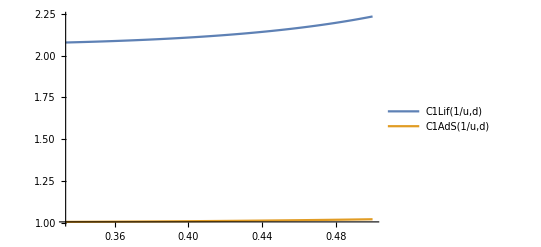

```mathematica
Plot[{C1Lif[1/u,d],C1AdS[1/u,d]},{u, 1/2, 1/3}, PlotLegends->"Expressions"]
```